# Mechanisms package and sub-packages

version 1.51
Christian Santangelo
Copyright 2020

#### Package organization

mechanisms: The mechanisms main package contains functions for manipulating and using mechanisms.

rigidity: This subpackage contains functions for basic rigidity of mechanisms and some functions for linkages

origami: this sub package contains functions for handling origami specifically.

These packages also use the Mathematica Developer package to take advantage of packed arrays when possible. A C compiler is recommended but not necessary.

#### To do list and known bug list

plotTension can look wonky and should be reworked to look nicer.

Is there a better way to do minimization with compiled functions and constraints. The algorithms are slow and that means fixed joints are poorly handled

isometricTrajectory[] is just too darn hard to use right now.

?origami and ?framework return an error (though they work otherwise).

## mechanisms main package

```mathematica
BeginPackage["mechanisms`",{"Developer`"}];
$mechanismsVersion=1.52;
$mechanismsVersionText="mechanisms version 1.52";
```

#### code snippet to check for C compiler and Mathematica version

```mathematica
(* 
	We need MeshRegion to work for this package to work so make sure we are using at least version 10 of Mathematica
*)
If[ $VersionNumber<10, Print["Mathematica version may be too low."]];

(* 
	A snippet of code to test or a working C compiler, modified from
	https://mathematica.stackexchange.com/questions/39837/check-whether-a-working-ccompiler-is-installed
*)
If[Quiet[Check[TrueQ[Compile[{}, 0, CompilationTarget -> "C"][] == 0], False]],
  $compilationTarget = "C",
  Print["C compilation failed. Using MVM code instead."];
  $compilationTarget = "MVM"
];
```

## usage

### components for mechanisms

```mathematica
$mechanismComponents::usage=
"$mechanismComponents lists all valid components. $mechanismCompositeComponents lists composite mechanism components.";

$mechanismCompositeComponents::usage=
"$mechanismComponents lists all valid components. $mechanismCompositeComponents lists composite mechanism components.";

rigidBar::usage=
"rigidBar[{StyleBox[\"vertex\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"1\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"vertex\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"2\",FontSlant->\"Italic\"]}] represents a rigid bar. Use Options[rigidBar] to see valid properties.";
SetAttributes[rigidBar,NHoldFirst];

spring::usage="spring[{StyleBox[\"vertex\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"1\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"vertex\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"2\",FontSlant->\"Italic\"]}] represents a spring. Use Options[spring] to see valid properties.";
SetAttributes[spring,NHoldFirst];

joint::usage="joint[StyleBox[\"v\",FontSlant->\"Italic\"]] represents a freely rotating joint that is fixed in place. Use Options[joint] to see valid properties.";
SetAttributes[joint,NHoldFirst];

angleJoint::usage="angleJoint[{StyleBox[\"v1\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\"v2\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\"v3\",FontSlant->\"Italic\"]}] represents a torsional spring associated with the turning angle from vertex StyleBox[\"v1\",FontSlant->\"Italic\"] to StyleBox[\"v2\",FontSlant->\"Italic\"] to StyleBox[\"v3\",FontSlant->\"Italic\"]. Use Options[angleJoint] to see valid properties.";
SetAttributes[angleJoint,NHoldFirst];

fold::usage="fold[StyleBox[\"{\",FontSlant->\"Italic\"]StyleBox[\"v1\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\"v2\",FontSlant->\"Italic\"]StyleBox[\"}\",FontSlant->\"Italic\"]] represents a fold with a torsional spring controlling its fold angle. Use Options[fold] to see valid properties.";
SetAttributes[fold,NHoldFirst];

face::usage="face[{StyleBox[\"v1\",FontSlant->\"Italic\"],...}] represents a face. Use Options[face] to see valid properties.";
SetAttributes[face,NHoldAll];

block::usage="block[{StyleBox[\"v1\",FontSlant->\"Italic\"],...}] is a mechanism component that creates a \"block\" face made rigid by extra rigidBar elements.";

triangulatedFace::usage="triangulatedFace[{StyleBox[\"v1\",FontSlant->\"Italic\"],...}] is a mechanism component that creates a triangulated face, with shortest diagonal triangulated first.";

flexibleBar::usage="flexibleBar[{StyleBox[\"v1\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\"v2\",FontSlant->\"Italic\"]},StyleBox[\"n\",FontSlant->\"Italic\"]] is a mechanism component that creates a bar with StyleBox[\"n\",FontSlant->\"Italic\"] points between.";

modEuclidean::usage="modEuclidean[{v1,v2}], is a component to orient a line between vertices v1 and v2 with the x axis
modEuclidean[{v1, v2, v3}] is a component that orients the specified vertices to the xy plane.";
```

### mechanism creation and manipulation

```mathematica
framework::usage=
"framework[ { {x1, y1}, ...}, {cell1[ {i1, i2, ..} ], ... } ] returns a linkage in 2D with vertices at {{x1, y1}, ..} and made from the specified cells.
framework[ { {x1, y1, z1}, ...}, {cell1[ {i1, i2, ..} ], ... } ] returns a linkage in 3D with vertices at {{x1, y1}, ..} and made from the specified cells.

framework[] takes the same options as MeshRegion[] as well as an option \"overlapPrecision\" which determines how close vertices need to be in order to be mapped onto each other.
Use $mechanismComponents or $mechanismCompositeComponents to get a list of cells that are recognized.";

origami::usage=
"origami[ { {x1, y1}, ...}, {cell1[ {i1, i2, ..} ], ... } ] returns an origami in 3D (displayed in 2D) with vertices at {{x1, y1}, ..} and made from the specified cells.
origami[ { {x1, y1, z1}, ...}, {cell1[ {i1, i2, ..} ], ... } ] returns an origami in 3D with vertices at {{x1, y1}, ..} and made from the specified cells.

origami[] takes the same options as MeshRegion[] as well as an option \"overlapPrecision\" which determines how close vertices need to be in order to be mapped onto each other.
Use $mechanismComponents or $mechanismCompositeComponents to get a list of cells that are recognized.";

mechanismQ::usage="mechanismQ[ m ] returns True if and only if m is a mechanism.";

boundaryVertices::usage="boundaryVertices[ mechanism ] returns a list of oriented boundary vertices { component 1, ...} where each boundary component is a list of vertex indices. A boundary is defined as the boundary of a set of 2D faces.";
boundaryEdges::usage="boundaryEdges[ mechanism ] returns a list of oriented boundary edges {{v11, v12},{v21,v22},...}. A boundary is defined as the boundary of a set of 2D faces.";
boundaryFaces::usage="boundaryFaces[ mechanism ] returns a list of oriented boundary components {face 1, face 2, ...}, ...}. A boundary is defined as the boundary of a set of 2D faces.";
interiorVertices::usage="interiorVertices[ mechanism ] returns a list of interior vertices.";
interiorEdges::usage="interiorEdges[ mechanism ] returns a list of interior edges.";

listVertices::usage=
"listVertices[StyleBox[\"mechanism\",FontSlant->\"Italic\"], {StyleBox[\"cell1\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"cell2\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\"...\",FontSlant->\"Italic\"]StyleBox[\"}\",FontSlant->\"Italic\"]] lists the vertices associated with a list of cells.";

listEdges::usage=
"listEdges[StyleBox[\"mechanism\",FontSlant->\"Italic\"], StyleBox[\"{\",FontSlant->\"Italic\"]StyleBox[\"cell1\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"cell2\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\"...\",FontSlant->\"Italic\"]StyleBox[\"}\",FontSlant->\"Italic\"]] lists the edges (oriented if possible) associated with a list of cells.";

listFaces::usage=
"listFaces[StyleBox[\"mechanism\",FontSlant->\"Italic\"], StyleBox[\"{\",FontSlant->\"Italic\"]StyleBox[\"cell1\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"cell2\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\"...\",FontSlant->\"Italic\"]StyleBox[\"}\",FontSlant->\"Italic\"]] lists of the faces (oriented if possible) associated with a list of cells.";
joinMechanism::usage=
"joinMechanism[StyleBox[\"m1\",FontSlant->\"Italic\"], StyleBox[\"m2\",FontSlant->\"Italic\"], ...] creates a new mechanism by joining several individual ones. Overlapping vertices are identified if they fall within a specified precision.";
mechanismPositions::usage=
"mechanismPositions[ StyleBox[\"mechanism\",FontSlant->\"Italic\"] ] returns the coordinates of the vertices of StyleBox[\"mechanism\",FontSlant->\"Italic\"].
mechanismPositions[ StyleBox[\"mechanism\",FontSlant->\"Italic\"] -> StyleBox[\"positions\",FontSlant->\"Italic\"] ] returns a new mechanism with coordinates given by StyleBox[\"positions\",FontSlant->\"Italic\"].";
displayDimension::usage=
"displayDimension[ StyleBox[\"mechanism\",FontSlant->\"Italic\"] ] returns the display dimension.
displayDimension[ StyleBox[\"mechanism\",FontSlant->\"Italic\"] -> StyleBox[\"dim\",FontSlant->\"Italic\"] ] returns a mechanism with display dimension StyleBox[\"dim\",FontSlant->\"Italic\"].";

embeddingDimension::usage=
"embeddingDimension[ StyleBox[\"mechanism\",FontSlant->\"Italic\"] ] returns the embedding dimension.
embeddingDimension[ StyleBox[\"mechanism\",FontSlant->\"Italic\"] -> StyleBox[\"dim\",FontSlant->\"Italic\"] ] returns a mechanism with embedding dimension StyleBox[\"dim\",FontSlant->\"Italic\"].";

deleteDanglingVertices::usage="deleteDanglingVertices[StyleBox[\"m\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\"type\",FontSlant->\"Italic\"]] deletes all vertices of StyleBox[\"m\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]not adjacent to a cell of a specific type, either \"faces\" or \"edges\".
If omitted, the argument StyleBox[\"type\",FontSlant->\"Italic\"] defaults to \"faces\" for origami or \"edges\" for frameworks. See: deleteVertices[]";

saveToFOLD::usage="saveToFOLD[StyleBox[\"mechanism\",FontSlant->\"Italic\"], StyleBox[\"filename\",FontSlant->\"Italic\"]] saves a FOLD file from a mechanism.";
loadFromFOLD::usage=
"loadFromFOLD[StyleBox[\"filename\",FontSlant->\"Italic\"]] loads a mechanism from a FOLD. Use option \"face\" to choose how to treat a polygon.";
```

```mathematica
applyMechanism::usage="applyMechanism[ mech, things to do ] applies a list of functions to a mechanism.";

deleteVertices::usage="deleteVertices[vertices] represents an operation that deletes a list of vertices from a mechanism.
deleteVertices[ mechanism, vertices ] deletes a list of vertices.";
subdivideEdge::usage="subdivideEdge[ label -> edge(, fraction) ] represents an operation that subdivides an edge with a new vertex with a label. Fraction is a number between 0 and 1 specifying how far along the edge it should be subdivided. It defaults to 1/2.
subdivideEdge[mechanism, label -> edge (,fraction)] subdivides the edge.";
placeVertex::usage="placeVertex[ vertex -> posSpec] represents an operation that moves a vertex to posSpec. Offset[ dispSpec] displaces a vertex by dispSpec.
placeVertex[ mechanism, vertex -> posSpec] places a vertex according to posSpec.";
applyToCells::usage="applyToCells";
Henneberg::usage="Henneberg[1][label -> vertices, pos] is an Henneberg operation of type 1 that creates a new vertex at a position and attaches it to vertices.
Henneberg[2][label -> edge, pos] is a Henneberg operation of type 2 that subdivides an edge and places the new vertex.";
labelVertex::usage="labelVertex[ v1 -> label ] applies a label to vertex v1.";
subdivideFace::usage="subdivideFace[ edgeSpec ] represents a function to subdivide a face and add edgeSpec as a new edge.";
```

```mathematica
mechanismComponents::usage=
"mechanismComponents[ mechanism, pattern ] returns the components matching pattern.
mechanismComponents[ mechanism, pattern1-> {property1->data1,...}, ...] changes components matching pattern by adding, if possible the property specified.";

mechanismStyles::usage="mechanismStyles[mechanism] returns a list of cells and their styles.
mechanismStyles[mechanism, {cell1, cell2,...} -> {style1, style2, ...}] changes the styles of the list of cells to the corresponding element of styles.";

mechanismLabels::usage="mechanismLabels[mechanism] returns a list of cells and their labels.
mechanismLabels[mechanism, {cell1, cell2,...} -> {label1, label2, ...}] changes the labels of the list of cells to the corresponding element of labels.";
```

```mathematica
deleteCells::usage=
"deleteCells[mech, pattern] deletes cells that match a pattern.
deleteCells[pattern] is a form of deleteCells[] that can act on a mechanism.";

deleteData::usage=
"deleteData[mech, pattern] deletes the data associated with a pattern.
deleteData[pattern] represents an operation that can delete data from a mechanism.";

addCells::usage="addCells[ {cell1[{i1, ..}],..} ] represents an operation that adds cells to a mechanism.
addCells[m, {cell1[{i1, i2, ...}], ...}] adds cells to a mechanism.";
```

### periodic functions

```mathematica
tesselateMechanism::usage=
"tesselateMechanism[mechanism, primitive vector, n1 ], tesselateMechanism[mechanism, {vector 1, vector 2}, {n1, n2}],  tesselateMechanism[mechanism, {vector 1, vector 2, vector 3}, {n1, n2, n3}] tesselates a mechanism using a set of 2D or 3D primitive vectors as an n1, n1 x n2 or n1 x n2 x n3 celled mechanism.";

periodicIdentification::usage=
"periodicIdentification[m, {f1, func1},..] applies transformation functions func1, func2, ... and creates a list of vertices identified via those transformations.
periodicIdentification[m, {z1,z2,...}, {vector1, vector2, ...}] identifies vertices under translation vectors {vector1, vector2,...} and returns rules identifying vertexDisplacement objects up to corresponding factors of {z1, z2,...}.";

minimalMechanism::usage=
"minimalMechanism[m, {vector1, vector2, ...}] reduces a mechanism to the smallest unit cell that can be tesselated periodically according to the basis of vectors provided.
It relies on periodicIdentification[] but unfortunately renumbers vertices.";
```

### geometry functions

```mathematica
infinitesimal::usage=
"infinitesimal[StyleBox[\"name\",FontSlant->\"Italic\"], StyleBox[\"order\",FontSlant->\"Italic\"]] represents an infinitesimal quantity that will be automatically expanded to a particular order.";
SetAttributes[infinitesimal,{NHoldAll,Constant}]
vertexPosition::usage=
"vertexPosition[StyleBox[\"vertex\",FontSlant->\"Italic\"], StyleBox[\"component\",FontSlant->\"Italic\"]] represents the displacement of vertex v along a particular component, which is one of \"x\", \"y\", or \"z\" or All[d] where d is the dimension.
vertexPosition[{StyleBox[\"vertex\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"1\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"vertex\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"2\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\"...\",FontSlant->\"Italic\"]},{StyleBox[\"component\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"1\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"component\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"2\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\"...\",FontSlant->\"Italic\"]}] returns a nested list of positions and components.";
SetAttributes[vertexPosition,{NHoldAll,Constant}]

vertexDisplacement::usage=
"vertexDisplacement[StyleBox[\"vertex\",FontSlant->\"Italic\"], StyleBox[\"component\",FontSlant->\"Italic\"]] represents the displacement of vertex v along a particular component, which is one of \"x\", \"y\", or \"z\" or All[d] where d is the dimension.
vertexDisplacement[{StyleBox[\"vertex\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"1\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"vertex\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"2\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\"...\",FontSlant->\"Italic\"]},{StyleBox[\"component\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"1\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"component\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"2\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\"...\",FontSlant->\"Italic\"]}] returns a nested list of displacements and components.";
SetAttributes[vertexDisplacement,{NHoldAll,Constant}]
to3D::usage="to3D[StyleBox[\"vertices\",FontSlant->\"Italic\"]] embeds a list of coordinates into 3D.";
to2D::usage="to2D[StyleBox[\"vertices\",FontSlant->\"Italic\"]] projects a list of coordinates into 2D.";
toDim::usage="toDim[d][StyleBox[\"vertices\",FontSlant->\"Italic\"]] projects a list of coordinates into d dimensions.";
randomDisplacements::usage=
"randomDisplacements[ StyleBox[\"d\",FontSlant->\"Italic\"], StyleBox[\"n\",FontSlant->\"Italic\"] ] creates a random displacement for StyleBox[\"n\",FontSlant->\"Italic\"] vertices in StyleBox[\"d\",FontSlant->\"Italic\"] dimensions.
randomDisplacements[StyleBox[\"mechanism\",FontSlant->\"Italic\"]] returns vertex positions that are randomly displaced from the mesh positions.";
orthogonalizeDisplacements::usage=
"orthogonalizeDisplacements[ {StyleBox[\"displacement\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"1\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"displacement\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"2\",FontSlant->\"Italic\"], ...}(, StyleBox[\"tolerance\",FontSlant->\"Italic\"]) ] returns an orthogonalized set of vertex displacements using optional tolerance.";

displacementRules::usage = "displacementRules[displacements] returns a list of rules to assign vertex displacements to their values.";
positionRules::usage = "positionRules[positions] returns a list of rules assigning vertex positions to their values.";
```

```mathematica
orthogonalComplement::usage="orthogonalComplement[basis] returns an orthonormal basis for the orthogonal complement of the vector space spanned by basis.
orthogonalComplement[basis,f] returns an orthonormal basis for the complement of the vector space spanned by basis using inner product function f.
Options are the same as Orthogonal.";

vertexCoordinatesQ::usage="vertexCoordinatesQ[ coords ] returns True if coords are valid vertex coordinates.
vertexCoordinatesQ[mech, coords] returns True if coords are valid vertex coordinates matching mechanism mech.";

numericCoordinatesQ::usage="numericCoordinatesQ[ coords ] returns True if coords are numeric and valid vertex coordinates.";
```

```mathematica
displacementVector::usage=
"displacementVector[ positions, edge ] returns the vector pointing along an oriented edge.
displacementVector[ positions, { edge 1, edge 2, ...} ] returns list of displacement vectors.
Edges can be specified as Line[{v1,v2}] or {v1,v2}.";

displacementLength::usage=
"displacementLength[ positions, edge 1 ] returns the length of an edge.
displacementLength[ positions, { edge 1, edge 2, ...} ] returns lengths of a list of edges.
Edges can be specified as Line[{v1,v2}] or {v1,v2}.";

displacementLengthSquared::usage=
"displacementLengthSquared[ positions, edge 1 ] returns the squared length of an edge.
displacementLengthSquared[ positions, { edge 1, edge 2, ...} ] returns squared lengths of a list of edges.
Edges can be specified as Line[{v1,v2}] or {v1,v2}.";

vectorAngle::usage=
"vectorAngle[ positions, {vertex 1, vertex 2, vertex 3}] returns the angle at vertex 2 spanned by the other two points.
vectorAngle[ positions, { triple 1, triple 2, ...} ] returns the vertex angles anong a list of vertex triples.";

turningAngle::usage=
"turningAngle[ positions, {vertex 1, vertex 2, vertex 3}] returns the turning angle at vertex 2 spanned by the other two points.
turningAngle[ positions, { triple 1, triple 2, ...} ] returns the turning angles anong a list of vertex triples.";

normalVector::usage=
"normalVector[ positions, {vertex 1, vertex 2, vertex 3} ] returns the vector normal to the plane spanned by the three points.
normalVector[ positions, { triple 1, triple 2, ...} ] returns vectors normal to the plane spanned by the list of triples.
normalVector[ positions, polygon ] returns the vector normal to a polygon.
normalVector[ positions, {polygon 1, polygon 2, ...} ] returns the vectors normal to a list of polygons.";

planarAngle::usage=
"planarAngle[positions, {v1, v2, v3}] returns the oriented angle at vertex v2 spanned by the other two vertices.
planarAngle[positions, {triple 1, triple 2, ...}] returns the oriented angles at for each triple of verticles.";

foldAngle::usage=
"foldAngle[ mesh, positions, edge ] returns the fold angle along an edge.
foldAngle[ mesh, positions,{edge 1, edge 2,...} ] returns the fold angle of a list of edges.";

gaussianCurvature::usage=
"gaussianCurvature[ mesh, positions,vertex ] returns the discrete Gaussian curvature of vertex.
gaussianCurvature[ mesh, positions,{vertex 1, vertex 2, ...} ] returns the discrete Gaussian curvature of a list of vertices.
gaussianCurvature[ mesh, metric,{vertex 1, vertex 2, ...} uses a metric to explicitly compute the Gaussian curvature at each vertex.";

alignMechanism::usage="alignMechanism[StyleBox[\"point\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"list\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"1\",FontSlant->\"Italic\"]StyleBox[\",\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"point\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"list\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"2\",FontSlant->\"Italic\"]] aligns StyleBox[\"point\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"list\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"2\",FontSlant->\"Italic\"] with StyleBox[\"point\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"list\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"1\",FontSlant->\"Italic\"] using only Euclidean motions.
alignMechanism[StyleBox[\"point\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"list\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"1\",FontSlant->\"Italic\"], StyleBox[\"mechanism\",FontSlant->\"Italic\"]] aligns a mechanical with StyleBox[\"point\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"list\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"1\",FontSlant->\"Italic\"] using Euclidean motions.
alignMechanism[StyleBox[\"mechanism\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"1\",FontSlant->\"Italic\"], StyleBox[\"mechanism\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"2\",FontSlant->\"Italic\"]] aligns StyleBox[\"mechanism\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"2\",FontSlant->\"Italic\"] to StyleBox[\"mechanism\",FontSlant->\"Italic\"]StyleBox[\" \",FontSlant->\"Italic\"]StyleBox[\"1\",FontSlant->\"Italic\"] using Euclidean motions.";

congruentQ::usage="congruentQ[p1,p2] tests whether the two vectorPositions are related by a rigid transformation.
congruentQ[p1,p2,tolerance] tests whether the two vectorPositions are related by a rigid transformation.
congruentQ[tolerance] is a function that can check the positions between two vertexPosition configurations.";
```

```mathematica
displaceVertices::usage="displaceVertices[mechanism,{v1 -> vector1,...}] returns a mechanism with vertices having index {v1, ...} displaced by a vector.";
```

### graphics

```mathematica
mechanismPrimitives::usage=
"mechanismPrimitives[mechanism] returns a list of mechanism primitives.
mechanismPrimitives[mechanism,positions] returns a list of mechanism primitives with vertices at positions.
mechanismPrimitives[mechanism,positions, cellspec] returns a list of mechanism primitives with vertices at positions and cells specified by cellspec.";
```

```mathematica
toGraphics::usage="toGraphics[mechanism (,positions)] converts a mechanism to graphics.
toGraphics[mechanism, positions, cellspec] converts mechanism components matching cellspec to graphics.";
```

```mathematica
toMeshRegion::usage="toMeshRegion[mechanism,positions] attempts to convert a mechanism to a MeshRegion object.";
```

```mathematica
plotMechanism::usage=
"plotMechanism[ mechanism, positions ] plots a mechanism using positions.
plotMechanism[mechanism, {positions 1, positions 2,...}] creates a list of plotted mechanisms with uniform size.";
```

```mathematica
plotDisplacement::usage=
"plotDisplacement[ mechanism, vertex displacements ] plots mechanism with arrows correspond to vertex displacements overlayed.";
plotTension::usage=
"plotTension[ mechanism, edges->tesions ] plots tensions on the edges of a mechanism.";
```

```mathematica
angleMarker::usage="angleMarker[m, {v1,v2,v3}, (radius) ] creates an arc around an angle spanning (v1,v2) to (v3,v2).";
angleText::usage="angleTest[m, {v1,v2,v3}, (distance) ] adds a text label to the angle spanning (v1,v2) to (v3,v2).";
```

## body

```mathematica
Begin["`Private`"];
```

### global data and patterns

```mathematica
$meshRegionProperties={MeshCellStyle,MeshCellLabel,MeshCellShapeFunction};
$mechanismComponents={rigidBar,spring,joint,fold,angleJoint};
$mechanismCompositeComponents={block,flexibleBar,triangulatedFace, modEuclidean};

(*data that will be stored for each of these components*)
dataForm[rigidBar]:={"length","stiffness"}
dataForm[spring]:={"length","stiffness","strain"}
dataForm[joint]:={"position","stiffness"}
dataForm[fold]:={"angle","torsionalStiffness"}
dataForm[angleJoint]:={"angle","angularStiffness"}
dataForm[_]:={}

mechanismPattern=_framework|_origami;

coordinatePattern2D = {{_, _}..};
coordinatePattern3D = {{_, _, _}..};
coordinatePattern = coordinatePattern2D | coordinatePattern3D;

mechanismQ[ mechanismPattern ]:=True
mechanismQ[_]:=False
```

### general tools

#### orthogonalComplement

```mathematica
Options[orthogonalComplement]=Options[Orthogonalize];
orthogonalComplement::notmat="Not all elements of basis have the same dimension.";
orthogonalComplement::notind="Basis is not linearly independent.";
```

```mathematica
basisQ[array_?MatrixQ]:=MatrixRank[array]==Dimensions[array][[1]]
basisQ[_]:=(Message[orthogonalComplement::notmat]; False)
```

```mathematica
orthogonalComplement[array_?basisQ,opt:OptionsPattern[]]:=
Select[Drop[
	Orthogonalize[Join[array,IdentityMatrix[Dimensions[array][[2]]]],opt],
	Dimensions[array][[1]]
],# . #>0&]
orthogonalComplement[array_?basisQ,inn_,opt:OptionsPattern[]]:=
Select[Drop[
	Orthogonalize[Join[array,IdentityMatrix[Dimensions[array][[2]]]],inn,opt],
	Dimensions[array][[1]]
],# . #>0&]

orthogonalComplement[__]:="nothing" /; Message[orthogonalComplement::notind]
```

#### projectOut,projectTo - marked for deletion

```mathematica
(*(* returns a projection operator to project out the array *)
projectOut[array_?MatrixQ]:=With[
{oarray=Orthogonalize[array]},
IdentityMatrix[Dimensions[array][[2]]] - Transpose[oarray] . oarray
]*)
```

```mathematica
(*(* returns a projection operator to project in the array *)
projectTo[array_?MatrixQ]:=With[
{oarray=Orthogonalize[array]},
Transpose[oarray] . oarray
]*)
```

#### realQ[] - marked for deletion

```mathematica
(*realQ[data_]:=(Chop[#.#]==0 &) @ Im[Flatten[{data}]]*)
```

#### orderPairs[]

orderPairs[{{n1, n2}, {n3, n4}, ...}]
 When provided a list of pairs, {1, b}, sort them in order such that {{1, 2}, {2, 3}, {3, 4}, ...}
 
 orderPairs[list 1, list 2] orders pairs in which elements of each list are paired with
 the corresponding element.

```mathematica
orderPairs[{}]:={}
orderPairs[pairList_?(MatrixQ[#,IntegerQ]&)]:=
	orderPairsTopologicalSort[Graph[UndirectedEdge@@@pairList]]/; Dimensions[pairList][[2]]==2

orderPairs[pairList_,correspondingList_]:=
With[
{
association=Dispatch@Thread[pairList->correspondingList]
},
	orderPairs[pairList]/.association
]/; Length[pairList]==Length[correspondingList]
```

```mathematica
(* this does a topological sort on a graph *)
orderPairsTopologicalSort[g_?AcyclicGraphQ]:=Partition[TopologicalSort[DirectedEdge@@@EdgeList[g]],2,1]
orderPairsTopologicalSort[g_Graph]:=List@@@(First@FindCycle[g,Infinity,1])
```

#### rotateTo[]

```mathematica
rotateTo[s_List,v_]:=With[{pos=FirstPosition[s,v]},If[MissingQ[pos],s,RotateLeft[s,pos[[1]]-1]]]
rotateTo[h_[s_List],v_]:=h[rotateTo[s,v]]
```

#### orderFaces[]

```mathematica
orderFaces[faceList_,v_Integer]:=orderPairs[{#[[2]],Last[#]}&/@faceList,faceList]
```

#### connectivity[]

```mathematica
connectivity["Methods"]:={{"vertices","edges","faces"}->{"vertices","edges","faces","ordered faces","ordered edges"}};
```

```mathematica
(*
connectivity[surf,"faces"->"vertices"];//RepeatedTiming
0.0079s on {7445,22105,14661} triangulated vertices, edges and faces
*)
connectivity[m_?MeshRegionQ,Rule["faces","vertices"]]:=
	MeshCells[m,2][[All,1]]
```

```mathematica
rotateThroughFaces[{}]:={}
rotateThroughFaces[faces_]:=Flatten[NestList[RotateLeft[#,{0,1}]&,faces,Last[Dimensions[faces]]-1],1]

connectivity[m_MeshRegion,Rule["vertices","faces"]]:=With[
{faces=rotateThroughFaces[MeshCells[m,2][[All,1]]]},
	GatherBy[
		Join[
			Transpose[{Range[MeshCellCount[m,0]]}], (*make a list of vertices in order of the form {{1},{2},...}*)
			faces
		],
	First][[All,2;;]]
]
```

```mathematica
(* 
geometry`Private`connectivity[surf,"faces"->"edges"];//RepeatedTiming
0.036s on {12289,36571,24283} triangulated vertices, edges and faces

Added ToPackedArray[] which ever so slightly speeds this function up. Since Transpose[]
packs arrays, it must speed up the operation of Transpose[] itself.
*)
connectivity[m_?MeshRegionQ,Rule["faces","edges"]]:=
With[{cells=Transpose[ToPackedArray[MeshCells[m,2][[All,1]]]]},
	Flatten[Partition[Transpose[Join[cells,{cells[[1]]}]],{1,2},1],{3}][[1]]
]

(* 
geometry`Private`connectivity[surf,"faces"->"edges"];//RepeatedTiming
0.19s on {7445,22105,14661} triangulated vertices, edges and faces
*)
connectivity[m_MeshRegion,Rule["edges","faces"]]:=With[
{edges=MeshCells[m,1][[All,1]],faces=MeshCells[m,2][[All,1]]},
	GatherBy[Flatten[{edges,rotateCells[faces]},1],Sort[#[[1;;2]]]&][[All,2;;]]
]

Options[rotateCells]={"Flatten"->True};
rotateCells[cells_,OptionsPattern[]]:=With[
{sortedCells=GatherBy[cells,Length]},
	Flatten[NestList[RotateLeft[#,{0,1}]&,#,Length[#[[1]]]-1]&/@sortedCells,2]
]/;OptionValue["Flatten"]

rotateCells[cells_,OptionsPattern[]]:=With[
{sortedCells=GatherBy[cells,Length]},
	First[NestList[RotateLeft[#,{0,1}]&,#,Length[#[[1]]]-1]&/@sortedCells]
]/;Not[OptionValue["Flatten"]]
```

```mathematica
(*
geometry`Private`connectivity[surf,"edges"->"vertices"];//RepeatedTiming
0.015s on {8236,24449,16214} triangulated vertices, edges and faces
*)
connectivity[m_?MeshRegionQ,Rule["edges","vertices"]]:=
	MeshCells[m,1][[All,1]]

(*
geometry`Private`connectivity[surf,"vertices"->"edges"];//RepeatedTiming
0.032s on {8236,24449,16214} triangulated vertices, edges and faces
*)
connectivity[m_?MeshRegionQ,Rule["vertices","edges"]]:=With[
{edges=MeshCells[m,1][[All,1]]},
	SortBy[GatherBy[Flatten[{edges,Reverse[edges,{2}]},1],First],First]
]
```

```mathematica
(* 
geometry`Private`connectivity[surf,"edges"->"ordered faces"];//RepeatedTiming
0.81s on {24731,73776,49046} triangulated vertices, edges and faces

This function unpacks packed arrays.
*)
connectivity[m_MeshRegion,Rule["edges","ordered faces"]]:=
With[
{
test1=connectivity[m,"vertices"->"faces"],
edges=Transpose[MeshCells[m,1][[All,1]]]
},
	ToPackedArray@MapThread[
		Join[#1,#2]&,
		{
		MapThread[Cases[#1,{__,#2}]&,{test1[[edges[[1]]]],edges[[2]]}],
		MapThread[Cases[#1,{_,#2,__}]&,{test1[[edges[[1]]]],edges[[2]]}]
		}
	]
]
```

```mathematica
(*
geometry`Private`connectivity[surf,"vertices"->"ordered faces"];//Timing
0.90s on {7445,22105,14661} triangulated surface.

Unpacks lists.
*)
connectivity[m_MeshRegion,Rule["vertices","ordered faces"]]:=With[
{unorderedFace=connectivity[m,"vertices"->"faces"]},
	MapThread[orderFaces,{unorderedFace,Range[Length[unorderedFace]]}]
]
```

```mathematica
(*
geometry`Private`connectivity[surf,"vertices"->"ordered edges"];//Timing
0.912s on {7445,22105,14661}

Unpacks lists.
*)
connectivity[m_?MeshRegionQ,Rule["vertices","ordered edges"]]:=
	connectivity[m,"vertices"->"ordered faces"][[All,All,1;;2]]
```

```mathematica
connectivity::badcombo="Methods are not recognized in this combination.";
connectivity[m_MeshRegion,Rule[_,_]]:="nothing" /; Message[connectivity::badcombo]
```

```mathematica
connectivity[m : mechanismPattern, Rule[s1_String,s2_String] ]:=connectivity[m["mesh"],s1->s2]
```

#### boundaryVertices[] boundaryEdges[] boundaryFaces[]

```mathematica
boundaryEdges[m_MeshRegion]:=
Module[
{
	facePairs=connectivity[m,"edges"->"faces"],
	edges=MeshCells[m,1][[All,1]],
	boundary
},
	boundary=Pick[edges,Length/@facePairs,1];
	If[Length[boundary]==0,
		{},
		Map[List@@#&,FindCycle[Graph[boundary],Infinity,All],{2}]
	]
]
```

```mathematica
boundaryVertices[m_MeshRegion]:=Map[First@@#&,boundaryEdges[m],{2}]
```

```mathematica
boundaryFaces[m_MeshRegion]:=Module[{i},
With[{boundary=boundaryVertices[m],faces=MeshCells[m,2][[All,1]]},
	Table[Select[faces,ContainsAny[boundary[[i]],#]&],{i,1,Length[boundary]}]
]]
```

#### interiorEdges[] interiorVertices[]

```mathematica
interiorEdges[mr_MeshRegion]:=
	Pick[
		MeshCells[mr,1][[All,1]],
		Length/@connectivity[mr,"edges"->"faces"],
		2
	]
```

```mathematica
interiorVertices[mr_MeshRegion]:=
Complement[
	DeleteDuplicates[Flatten[interiorEdges[mr]]],
	Flatten@boundaryVertices[mr]
]
```

#### deformMesh[]

```mathematica
inactiveForm[expr_]:=With[{head=Head[expr]},
	ReleaseHold[Uncompress[Compress[expr],Hold]/.head:>Inactive[head]]
]
```

```mathematica
deformMesh[m_MeshRegion,pos_?numericCoordinatesQ]:=
	Activate[
		ReplacePart[inactiveForm[m],1->pos]
	]/;MeshCellCount[m,0]==Length[pos]
deformMesh[m_compiledMeshRegion,pos_?numericCoordinatesQ]:=
	ReplacePart[m,1->deformMesh[m["mesh"],pos]]
```

```mathematica
deformMesh::badpos="Number of vertices in positions not the same as in the MeshRegion.";
deformMesh::badnum="Displacements are not valid or numeric.";

deformMesh[m_MeshRegion,pos_?numericCoordinatesQ]:="nothing"/;Message[deformMesh::badpos]
deformMesh[m_MeshRegion,p_]:="nothing"/;Message[deformMesh::badnum]
```

#### meshCells[]

```mathematica
distributePropertyTag[data_]:=
	Module[{x,y,z},
		Flatten[data//.{
			Property[x_,{}]:>x,
			Property[x_List,y_]:>(Property[#,y]&/@x),
			Property[Property[x_,y_],z_]:>Property[x,Join[Flatten@{{y},{z}}]]
		}]
	]
```

```mathematica
meshCells[mr_MeshRegion]:=Module[
{i},
	distributePropertyTag[Flatten@Table[Property[
		MeshCells[mr,{i,#}],DeleteCases[{
		MeshCellStyle->PropertyValue[{mr,{i,#}},MeshCellStyle],
		MeshCellShapeFunction->PropertyValue[{mr,{i,#}},MeshCellShapeFunction],
		MeshCellLabel->PropertyValue[{mr,{i,#}},MeshCellLabel]
	},Rule[_,Automatic]]]&/@Range[MeshCellCount[mr,i]],{i,0,2}]]
]
```

```mathematica
meshCells[mr_MeshRegion,i_Integer]:=
	distributePropertyTag[Flatten@Property[
		MeshCells[mr,{i,#}],DeleteCases[{
		MeshCellStyle->PropertyValue[{mr,{i,#}},MeshCellStyle],
		MeshCellShapeFunction->PropertyValue[{mr,{i,#}},MeshCellShapeFunction],
		MeshCellLabel->PropertyValue[{mr,{i,#}},MeshCellLabel]
	},Rule[_,Automatic]]]&/@Range[MeshCellCount[mr,i]]]
```

#### orientedQ[]

```mathematica
orientedQ[mr: _MeshRegion]:=
	AllTrue[
		DeleteCases[connectivity[mr,"edges"->"faces"],{_}],
		facePairOrientedQ
	]
orientedQ[_]:=False
```

```mathematica
facePairOrientedQ[{v1_,v2_}]:=With[
{
	eg2=Take[RotateLeft[v2,#],2]&/@Range[Length[v2]],
	eg1=Reverse[Take[RotateLeft[v1,#],2]]&/@Range[Length[v1]]
},
	ContainsAny[eg1,eg2]
]
facePairOrientedQ[v1_,v2_]:=With[
{
	eg2=Take[RotateLeft[v2,#],2]&/@Range[Length[v2]],
	eg1=Reverse[Take[RotateLeft[v1,#],2]]&/@Range[Length[v1]]
},
	ContainsAny[eg1,eg2]
]
```

### functions defining and handling individual cell types

#### unpackDisplayCells[], packDisplayCells[]

```mathematica
(*
unpackDisplayCells[] takes a list of display cells input by a user and turns it into an unpacked list of the form
  { cell name, indices, list of properties }

packDisplayCells[] takes a list of unpacked cells and repacks them into a form that MeshRegion can use.
*)

(*unpack cells input by users into an expanded form*)
unpackUserSingleCell[ Property[cell_[indices_], properties_] ]:={{cell,indices,properties}}
unpackUserSingleCell[ cell_[indices_] ]:= {{cell,indices,{}}} /; Head[cell]=!=Property

unpackDisplayCells[data_List]:=Flatten[ unpackUserSingleCell /@ data, 1 ] /. "unspecified"->Automatic

(*pack cells from their expanded form into display cells. This basically, the inverse of unpackCells[]. *)
packSingleDisplayCell[{cell_Symbol,indices_,{}}]:=cell[indices]
packSingleDisplayCell[{cell_Symbol,indices_,properties_}]:=Property[cell[indices],properties]

packDisplayCells[unpackedCells_]:=packSingleDisplayCell /@ unpackedCells
```

#### unpackComponentCells[], packComponentCells[]

```mathematica
(*
	This is how cells pack and unpack their own data.
*)
```

```mathematica
(*
	unpacks component cells that are already packed in condensed form.
*)
unpackComponentCells[data_List]:=Flatten[ unpackComponentSingleCell /@ data, 1 ] /. "unspecified"->Automatic

unpackComponentSingleCell[ h_[indices_, data_] ]:=
With[{form = dataForm[h]},
	MapThread[
		{h, #1, Thread[ form -> #2 ] }&, 
		{indices, Transpose[ Normal /@ data ]}
	]
]
```

```mathematica
(*
	given a list of expanded cells, repack them into a condensed form for storage in the data structure.
*)
packComponentCells[{}]:={}
packComponentCells[mechanismCells_]:=
	packCellData[ #[[1,1]][ #[[2]], #[[3]] ] ]& /@ Transpose /@ 
		GatherBy[
			{#[[1]], #[[2]], dataForm[ #[[1]] ] /. #[[3]] /. Options[ #[[1]] ]}& /@ mechanismCells,
			First
		]


packCellData[ rigidBar[ indices_, data_?MatrixQ ] ]:=
With[
{
	explicitLengths = DeleteCases[ Thread[ Range[Length[data]] -> data[[All,1]] ], _ -> Automatic ]
},
	rigidBar[ ToPackedArray[indices], {
		SparseArray[ explicitLengths, Length[indices], "unspecified" ],
		SparseArray[ data[[All,2]], Length[indices], Infinity ]
	}]
]

packCellData[ spring[ indices_, data_?MatrixQ ] ]:=
With[
{
	explicitLengths = DeleteCases[ Thread[ Range[Length[data]] -> data[[All,1]] ], _ -> Automatic ]
},
	spring[ ToPackedArray[indices], {
		SparseArray[ explicitLengths, Length[indices], "unspecified" ],
		SparseArray[ data[[All,2]], Length[indices], Infinity ],
		SparseArray[ data[[All,3]], Length[indices], "linear" ]
	}]
]

packCellData[ fold[ indices_, data_?MatrixQ ] ]:=
With[
{
	explicitAngles = DeleteCases[ Thread[ Range[Length[data]] -> data[[All,1]] ], _->Automatic]
},
	fold[ ToPackedArray[indices],{
		SparseArray[ explicitAngles, Length[indices], "unspecified" ],
		SparseArray[ data[[All,2]], Length[indices], Infinity ]
	}]
]

packCellData[ angleJoint[ indices_, data_?MatrixQ] ]:=
With[
{
	explicitAngles = DeleteCases[ Thread[ Range[Length[data]] -> data[[All,1]] ], _->Automatic]
},
	angleJoint[ ToPackedArray[indices], {
		SparseArray[ explicitAngles, Length[indices], "unspecified" ],
		SparseArray[ data[[All,2]], Length[indices], Infinity ]
	}]
]

packCellData[ joint[ indices_, data_List ] ]:=
With[{ dim = {Length[indices],3} }, 
With[{
stiffnessData = PadRight[ data[[All,2]] ],
positionData = PadRight[ data[[All,1]] ]
},
	joint[ ToPackedArray[indices],
		{
		(*position data*)
		SparseArray[ positionData /. Automatic->"unspecified", dim, "unspecified" ],
		(*stiffness data*)
		SparseArray[ stiffnessData, dim, Infinity ]
		}
	]
]]
```

#### componentData[]

```mathematica
(*
	This is how cells extract their own data
*)
```

```mathematica
componentData["stiffness", m_, positions_, spring[ indices_, { _,  stiffnessData : _SparseArray, _ } ] ]:=ToPackedArray @ Normal[stiffnessData]
componentData["strain", m_, positions_, spring[indices_, {_, _, forceData: _SparseArray } ] ]:=Normal[forceData] /. "linear"->( #1-#2 &)
componentData["length", m_, positions_, spring[indices_, {lengthData : _SparseArray, _, _} ] ]:=
Module[
{
	specifiedIndices = Flatten @ lengthData["NonzeroPositions"],
	specifiedValues = lengthData["NonzeroValues"],
	unspecifiedIndices, newordering
},
	unspecifiedIndices = Complement[ Range[Length[indices]], specifiedIndices ];
	newordering = Ordering[Join[specifiedIndices, unspecifiedIndices]];

	ToPackedArray[ Join[
		specifiedValues,
		If[Length[unspecifiedIndices]>0,displacementLengthInternal[positions, indices[[ unspecifiedIndices ]] ],{}]
	][[ newordering ]] ]
]
```

```mathematica
componentData["stiffness", m_, positions_, rigidBar[ indices_, {_, stiffnessData: _SparseArray } ] ]:=ToPackedArray @ Normal[stiffnessData]

componentData["length", m_, positions_, rigidBar[ indices_, {lengthData : _SparseArray, _} ] ]:=
Module[
{
	specifiedIndices = Flatten @ lengthData["NonzeroPositions"],
	specifiedValues = lengthData["NonzeroValues"],
	unspecifiedIndices, newordering
},
	unspecifiedIndices = Complement[ Range[Length[indices]], specifiedIndices ];
	newordering = Ordering[Join[specifiedIndices, unspecifiedIndices]];

	ToPackedArray[ Join[
		specifiedValues,
		If[Length[unspecifiedIndices]>0,displacementLengthInternal[positions, indices[[ unspecifiedIndices ]] ],{}]
	][[ newordering ]] ]
]
```

```mathematica
componentData["torsionalStiffness", m_, positions_, fold[indices_, { _, stiffnessData : _SparseArray }]]:=ToPackedArray[ Normal[stiffnessData] ]

componentData["angle", m_, positions_, fold[indices_, { angleData : _SparseArray, _ }]]:=
Module[
{
	specifiedIndices = Flatten @ angleData["NonzeroPositions"],
	specifiedValues = angleData["NonzeroValues"],
	unspecifiedIndices, newordering
},
	unspecifiedIndices = Complement[ Range[Length[indices]], specifiedIndices ];
	newordering = Ordering[Join[specifiedIndices, unspecifiedIndices]];

	ToPackedArray[ Join[
		specifiedValues,
		If[Length[unspecifiedIndices]>0,foldAngleInternal[m, positions, indices[[ unspecifiedIndices ]] ],{}]
	][[ newordering ]] ]
]
```

```mathematica
componentData["angularStiffness", m_, positions_, angleJoint[indices_, { _, stiffnessData : _SparseArray }]]:=ToPackedArray[ Normal[stiffnessData] ]

componentData["angle", m_, positions_, angleJoint[indices_, { angleData : _SparseArray, _ }]]:=
Module[
{
	specifiedIndices = Flatten @ angleData["NonzeroPositions"],
	specifiedValues = angleData["NonzeroValues"],
	unspecifiedIndices, newordering
},
	unspecifiedIndices = Complement[ Range[Length[indices]], specifiedIndices ];
	newordering = Ordering[Join[specifiedIndices, unspecifiedIndices]];

	ToPackedArray[ Join[
		specifiedValues,
		If[Length[unspecifiedIndices]>0,turningAngleInternal[positions, indices[[ unspecifiedIndices ]] ],{}]
	][[ newordering ]] ]
]
```

```mathematica
componentData["net stiffness", m_, positions_, joint[indices_, { _, stiffnessData : _SparseArray } ] ]:=
	ToPackedArray[ Min /@ Normal[stiffnessData] ]

componentData["components", m_, positions_, joint[indices_, {_, stiffnessData : _SparseArray } ] ]:=
With[
{
stiffnesses=Normal[stiffnessData]
},
	stiffnessToComponents /@ stiffnesses
]
stiffnessToComponents[{x_,y_,z_}]:={If[x≠0, "x",Nothing], If[y≠0,"y",Nothing], If[z≠0,"z",Nothing]}
stiffnessToComponents[{x_,y_}]:={If[x≠0, "x",Nothing], If[y≠0,"y",Nothing]}

componentData["stiffness", m_, positions_, joint[indices_, { _, stiffnessData : _SparseArray }]]:=
	ToPackedArray[ PadRight[ Normal[stiffnessData], {Length[indices], embeddingDimension[m]} ] ]

componentData["position", m_, positions_, joint[indices_, {positionData : _SparseArray, _} ] ]:=
Module[
{
	allPositions = positions[[ indices ]],
	specifiedValues = PadRight[ Normal[positionData], {Length[indices], embeddingDimension[m] } ],
	replacementFunction = If[#2=="unspecified", #1, #2]&
},
	MapThread[replacementFunction, {allPositions, specifiedValues}, 2]
]
```

#### replaceUnpackedCells[], replaceRepeatedUnpackedCells[]

```mathematica
(*apply replacement rules to the indices of expanded cells*)
replaceUnpackedCells[{},rules_] := {}
replaceUnpackedCells[data_,rules_] := With[{flipCells=Transpose[data]},
	Transpose[ { flipCells[[1]], flipCells[[2]] /. rules, flipCells[[3]] } ]
]

replaceRepeatedUnpackedCells[{},rules_] := {}
replaceRepeatedUnpackedCells[data_,rules_] := With[{flipCells=Transpose[data]},
	Transpose[ { flipCells[[1]], flipCells[[2]] //. rules, flipCells[[3]] } ]
]
```

#### replacePackedCells[]

```mathematica
(*
	This is used to replace elements of the data stored in a mechanism component without unpacking it.
*)
replacePackedCells[ head_[indices_, data_], rule_ ] := head[indices, replaceElement[# , rule]& /@ data ]
```

```mathematica
(*
from: https://mathematica.stackexchange.com/questions/13790/using-replaceall-on-sparsearray
*)
replaceElement[s_SparseArray, rule_] := With[
    {
    elem = Replace[s["NonzeroValues"], rule, {1}],
    def = Replace[s["Background"], rule]
    },

    Replace[
        s,
        Verbatim[SparseArray][a__, _, {b__, _}] :> SparseArray[a, def, {b, elem}]
    ]
]
```

#### deleteFromPackedComponentCells[], extractFromPackedComponentCells[]

These don’t get used yet and we may just delete them.

```mathematica
(*
deleteFromPackedCells[mech, components, pattern] deletes cells that match a pattern.
extractFromPackedCells[mech, components, pattern] extracts cells that match a pattern.
 *)
deleteFromPackedComponentCells[ m : mechanismPattern , patt_ ] := With[
{actualPattern = indexPattern[ patt ]},
	m["components" -> deleteEmptyHeads[ deleteFromPackedCells[ #, actualPattern ]& /@ m["components"] ] ]
]
deleteFromPackedCells[ head_[ indices_, data_ ] , deletionPattern_] :=
Module[{ markedForDeletion },

	If[ MatchQ[head, Head[deletionPattern]  ],

		markedForDeletion = Position[ indices,  deletionPattern[[1]] ];
		head[ Delete[indices, markedForDeletion], SparseArray[Delete[ #, markedForDeletion ]]& /@ data ],

		head[indices,data]
	]
]

deleteEmptyHeads[ data_ ] := DeleteCases[ data, _[{}] ]

extractFromPackedComponentCells[ m : mechanismPattern , patt_ ] := With[
{actualPattern = indexPattern[ patt ]},
	m["components" -> deleteEmptyHeads[ deleteFromPackedCells[ #, actualPattern ]& /@ m["components"] ] ]
]
extractFromPackedCells[ head_[ indices_, data_ ] , deletionPattern_] :=
Module[{ markedForDeletion },

	If[ MatchQ[head, Head[deletionPattern]  ],

		markedForDeletion = Position[ indices,  deletionPattern[[1]] ];
		head[ Extract[indices, markedForDeletion], SparseArray[Extract[ #, markedForDeletion ]]& /@ data ],

		head[indices,data]
	]
]


indexPattern[x_Blank] := _[_] /; Length[x]==0
indexPattern[x_Blank] := x
indexPattern[h_[ n_List]] := With[{numbers=Range[Length[n]]}, h[Alternatives @@ Map[RotateRight[n,#]&, numbers]]]
indexPattern[h_[ r_Alternatives]] := h[ indexPattern/@r ]
indexPattern[h_[ n : Except[_Alternatives|_List]] ] := h[n]
```

#### selectData[], selectConstraintsFromData[]

We don’t seem to use this first function anywhere.

```mathematica
selectData[ rigidBar[ indices_, {lengthData : _SparseArray, stiffnessData : _SparseArray} ], criteria_ ]:=
With[
{
	selector = Pick[ Range[Length[indices]], criteria /@ Transpose[ {Normal[lengthData], Normal[stiffnessData]} ] ]
},
	rigidBar[ indices[[ selector ]], { lengthData[[ selector ]], stiffnessData[[ selector ]] } ]
]

selectData[ fold[ indices_, {angleData : _SparseArray, stiffnessData : _SparseArray} ], criteria_ ]:=
With[
{
	selector = Pick[ Range[Length[indices]], criteria /@ Transpose[ {Normal[angleData], Normal[stiffnessData]} ] ]
},
	fold[ indices[[ selector ]], { angleData[[ selector ]], stiffnessData[[ selector ]] } ]
]

selectData[ joint[ indices_, {positionData : _SparseArray, stiffnessData : _SparseArray} ], criteria_ ]:=
With[
{
	selector = Pick[ Range[Length[indices]], criteria /@ Transpose[ {Normal[positionData], Normal[stiffnessData]} ] ]
},
	joint[ indices[[ selector ]], { positionData[[ selector ]], stiffnessData[[ selector ]] } ]
]

selectData[ angleJoint[ indices_, {positionData : _SparseArray, stiffnessData : _SparseArray} ], criteria_ ]:=
With[
{
	selector = Pick[ Range[Length[indices]], criteria /@ Transpose[ {Normal[positionData], Normal[stiffnessData]} ] ]
},
	angleJoint[ indices[[ selector ]], { positionData[[ selector ]], stiffnessData[[ selector ]] } ]
]

selectData[ spring[ indices_, {positionData : _SparseArray, stiffnessData : _SparseArray, force : _SparseArray} ], criteria_ ]:=
With[
{
	selector = Pick[ Range[Length[indices]], criteria /@ Transpose[ {Normal[positionData], Normal[stiffnessData], Normal[force] } ] ]
},
	spring[ indices[[ selector ]], { positionData[[ selector ]], stiffnessData[[ selector ]], force[[ selector ]] } ]
]
```

```mathematica
(*
get a list of all components that will be considered constraints.
*)
selectConstraintsFromData[ rigidBar[ indices_, {lengthData : _SparseArray, stiffnessData : _SparseArray} ] ]:=
With[
{
	selector = Pick[ Range[Length[indices]],  Normal[stiffnessData], Infinity ]
},
	If[Length[selector]>0,
		rigidBar[ indices[[ selector ]], { lengthData[[ selector ]], stiffnessData[[ selector ]] } ],
		Nothing
	]
]

selectConstraintsFromData[ fold[ indices_, {angleData : _SparseArray, stiffnessData : _SparseArray} ] ]:=
With[
{
	selector = Pick[ Range[Length[indices]], Normal[stiffnessData], Infinity ]
},
	If[Length[selector]>0,
		fold[ indices[[ selector ]], { angleData[[ selector ]], stiffnessData[[ selector ]] } ],
		Nothing
	]
]

selectConstraintsFromData[ angleJoint[ indices_, {angleData : _SparseArray, stiffnessData : _SparseArray} ] ]:=
With[
{
	selector = Pick[ Range[Length[indices]], Normal[stiffnessData], Infinity ]
},
	If[Length[selector]>0,
		fold[ indices[[ selector ]], { angleData[[ selector ]], stiffnessData[[ selector ]] } ],
		Nothing
	]
]

selectConstraintsFromData[ joint[ indices_, {positionData : _SparseArray, stiffnessData : _SparseArray} ] ]:=
With[
{
	selector = Pick[ Range[Length[indices]], Max /@ Normal[stiffnessData], Infinity ]
},
	If[Length[selector]>0,
		joint[ indices[[ selector ]], { positionData[[ selector ]], stiffnessData[[ selector ]] } ],
		Nothing
	]
]

selectConstraintsFromData[ spring[ indices_, {lengthData : _SparseArray, stiffnessData : _SparseArray, force : _SparseArray} ] ]:=
With[
{
	selector = Pick[ Range[ Length[indices] ], Normal[stiffnessData], Infinity ]
},
	If[Length[selector]>0,
		spring[indices[[ selector ]], { lengthData[[ selector ]], stiffnessData[[ selector ]], force[[ selector ]] } ],
		Nothing
	]
]

selectConstraintsFromData[ _ ]:=Nothing
```

#### componentPattern[]

```mathematica
componentPattern[x_Blank] := {x, _, _} /; Length[x]==0
componentPattern[x_Blank] := {x[[1]],_,_}

componentPattern[r_Alternatives] := Map[ componentPattern ,  r ]
componentPattern[h_[r_Alternatives]] := componentPattern[ Map[ h , r ] ]
componentPattern[h_[n_List]]:= With[ { numbers=Range[Length[n]] } , {h , Alternatives @@ Map[RotateRight[n,#]& , numbers ], _ } ]
componentPattern[h_[n : Except[_Alternatives|_List]]] := {h, n, _}
```

### origami[], framework[]

#### expandCompositeCell[]

```mathematica
expandCompositeCell[coordinates_][Property[cell_,properties_]]:=Property[expandCompositeCell[coordinates][cell],properties]
```

```mathematica
modEuclidean::threed="modEuclidean[] cell needs three vertices in three dimensions.";
modEuclidean::twod="modEuclidean[] cell needs two vertices in two dimensions.";

expandCompositeCell[coordinates_][modEuclidean[indices_]]:=Module[
{
	dim = Last[Dimensions[coordinates]] (*, vertexSpan*)
},
(*	vertexSpan =  displacementVector[coordinates, {{indices[[1]], indices[[2]]},{indices[[1]], indices[[3]]}}]	;*)

	Switch[dim,
		3, If[ Length[indices] ≤ 3, {
			joint[indices[[1]]],
			Property[ joint[ indices[[2]] ],"stiffness"->{0,Infinity, Infinity}],
			Property[ joint[ indices[[3]] ],"stiffness"->{0,0,Infinity}]
		},
			Message[modEuclidean::threed];
			{}
		],
		
		2, If[ Length[indices] ≤ 2, {
			joint[indices[[1]]],
			Property[ joint[ indices[[2]] ],"stiffness"->{0,Infinity}]
		},
			Message[modEuclidean::twod];
			{}
		],
		_, {joint[indices[[1]]]}
	]
]
```

```mathematica
expandCompositeCell[coordinates_][spring[x_List]] := spring /@ Partition[x,2,1] /; Length[x]>2
expandCompositeCell[coordinates_][rigidBar[x_List]] := rigidBar /@ Partition[x,2,1] /; Length[x]>2
expandCompositeCell[coordinates_][angleJoint[x_List]] := angleJoint /@ Partition[x,3,2] /; Length[x]>3
```

```mathematica
expandCompositeCell[coordinates_][block[indices_]]:=With[
{
	centroid=Mean[to3D[coordinates][[indices]]],
	nv=First[normalVector[to3D[coordinates],{indices},"normalize"->False]],
	p1=ToString[Unique[]],p2=ToString[Unique[]]
},
	Join[
	{
	Polygon[indices],
	Point[p1->(centroid+nv/10)],
	Point[p2->(centroid-nv/10)]
	},
	rigidBar[{#,p1}]&/@indices,
	rigidBar[{#,p2}]&/@indices,
	rigidBar[#]&/@Partition[indices,2,1,1]
	]
]/;Length[indices]>=3

block::badn="Faces need at least 3 indices.";
expandCompositeCell[coordinates_][block[_]]:=(Message[block::badn]; {})
```

```mathematica
expandCompositeCell[coordinates_][triangulatedFace[indices_]]:=Flatten[decomposePolygon[coordinates,indices]]/;Length[indices]>2

triangulatedFace::badn="Faces need more than 3 indices.";
expandCompositeCell[coordinates_][triangulatedFace[indices_]]:=(Message[triangulatedFace::badn]; {})/;Length[indices]<3

decomposePolygon[coordinates_,indices_]:=With[
{
diagonal=findShortestDiagonal[coordinates,indices]
},
	{
	(*Property[edgeData[indices[[diagonal]]],{"data"->indices}],*)
	Property[fold[indices[[diagonal]]],{"angle"->0,"stiffness"->Infinity,MeshCellStyle->Gray}],
	decomposePolygon[coordinates,indices[[diagonal[[1]];;diagonal[[2]]]]],
	decomposePolygon[coordinates,Join[indices[[diagonal[[2]];;]],indices[[;;diagonal[[1]]]]]]
	}
]/;Length[indices]>3
decomposePolygon[coordinates_,indices_]:=face[indices] /; Length[indices]==3

findShortestDiagonal[coordinates_,indices_]:=Module[{
	pairs=Subsets[Range[Length[indices]],{2}],
	adjacent=Join[Partition[Range[Length[indices]],2,1,1],Reverse/@Partition[Range[Length[indices]],2,1,1]],
	diagonals
},
	diagonals=Select[pairs,Not[MemberQ[adjacent,#]]&]; (*remove the sides of the polygon to make the diagonal list*)
	First[First[MinimalBy[Transpose[{diagonals,displacementLengthSquared[coordinates[[indices]],diagonals]}],Last]]]
]
```

```mathematica
expandCompositeCell[coordinates_][flexibleBar[indices_,num_Integer]]:=With[
{
	endPoints=coordinates[[indices]],pLabel=ToString[Unique[]]
},
	Join[
		Property[Point[pLabel[#]->(endPoints[[1]]+# endPoints[[2]]/(num+1))],MeshCellStyle->{Gray}]&/@Range[num],
		rigidBar/@Partition[Range[3,num+2],2,1],
		{rigidBar[{indices[[1]],pLabel[1]}],rigidBar[{pLabel[num],indices[[2]]}]},
		angleJoint/@Partition[Range[3,num+2],3,1],
		{angleJoint[{indices[[1]],3,4}],angleJoint[{num+1,num+2,indices[[2]]}]}
	]
]/;num>1

expandCompositeCell[coordinates_][flexibleBar[indices_,1]]:=With[
{
	endPoints=coordinates[[indices]],pLabel=ToString[Unique[]]
},
		{
		Property[Point[pLabel->(endPoints[[1]]+endPoints[[2]])/2],MeshCellStyle->{Gray}],
		rigidBar[{indices[[1]],pLabel}],rigidBar[{pLabel,indices[[2]]}],
		angleJoint[{indices[[1]],pLabel,indices[[2]]}]
		}
]

expandCompositeCell[coordinates_][flexibleBar[indices_,0]]:={rigidBar[indices]}

flexibleBar::badn="Number of points between `1` and `2` must be an integer 0 or larger.";
expandCompositeCell[coordinates_][flexibleBar[indices_,_]]:=(Message[flexibleBar::badn,indices[[1]],indices[[2]]]; {rigidBar[indices]})
```

```mathematica
expandCompositeCell[coordinates_][cell_]:=cell/;Not[MatchQ[Join[{Property},$mechanismCompositeComponents],Head[cell]]]
```

#### cellForm[]

```mathematica
(*
cellForm[] takes a cell and returns the following:

 { new vertices, list of unpacked display cells, list of unpacked component cells }

it is also where we do any error checking, etc.

This is the function to modify if you want to add more cell types.
*)
```

```mathematica
(*if there is no Property[] in front of it, add a blank Property around it to simplify the rest of the code*)
cellForm[cell : Except[_Property] ]:=cellForm[Property[cell,{}]]

(*MeshRegion cell forms*)
cellForm[Property[Point[index_],properties_]]:={
	{},
	{{Point,index,FilterRules[properties,$meshRegionProperties]}},
	{}
}
cellForm[Property[Polygon[index_],properties_]]:={
	{},
	{{Polygon,index,FilterRules[properties,$meshRegionProperties]}},
	{}
}
cellForm[Property[Line[index_],properties_]]:={
	{},
	{{Line,index,FilterRules[properties,$meshRegionProperties]}},
	{}
}
```

```mathematica
(*
This is a special cell type that adds a vertex with arbitrary label.
*)
cellForm[Property[Point[label_->position_], properties_]]:={
	{{label,position}},
	{{Point,label,FilterRules[properties,$meshRegionProperties]}},
	{}
}
```

```mathematica
Options[rigidBar]={"stiffness"->Infinity,"length"->Automatic};

rigidBar::length = "length should be a non-negative number or expression in rigidBar[ `1` ].";
rigidBar::stiffness = "stiffness should be a non-negative number or expression in rigidBar[ `1` ].";

testCellProperty[rigidBar, index_, "length" -> x : _?NumericQ] := ( Message[rigidBar::length, index]; "length" -> x ) /; x < 0
testCellProperty[rigidBar, index_, "length"->x : Except[_List]] :="length" -> x
testCellProperty[rigidBar, index_, "stiffness" -> x : _?NumericQ] := ( Message[rigidBar::length, index]; "stiffness" -> x ) /; x < 0
testCellProperty[rigidBar, index_, "stiffness"->x : Except[_List]]:="stiffness" -> x

cellForm[Property[rigidBar[indices : {_, _} ], properties_]]:={
	{},
	{ {Line,indices,Join[{MeshCellStyle->Black},FilterRules[properties,$meshRegionProperties]]} },
	{ {rigidBar,indices, testCellProperty[rigidBar, indices, #]& /@ FilterRules[properties,Options[rigidBar]]} }
}
```

```mathematica
Options[spring]={"stiffness"->1, "length"->Automatic, "strain"->"linear"};

spring::length = "Length should be a non-negative number or expression in spring[ `1`] .";
spring::stiffness = "Stiffness should be a non-negative number or expression in spring[ `1` ].";

testCellProperty[spring, index_, "length" -> x : _?NumericQ] := ( Message[spring::length, index]; "length" -> x ) /; x < 0
testCellProperty[spring, index_, "length" -> x : Except[_List] ]:="length" -> x
testCellProperty[spring, index_, "stiffness" -> x : _?NumericQ] := ( Message[spring::stiffness, index]; "stiffness" -> x ) /; x < 0
testCellProperty[spring, index_, "stiffness"->x : Except[_List]]:="stiffness" -> x
testCellProperty[spring, index_, "strain"->x : _Function|"linear"]:="strain" -> x

cellForm[Property[spring[indices : {_,_}], properties_]]:={
	{},
	{{Line,indices,Join[{MeshCellStyle->Gray},FilterRules[properties,$meshRegionProperties]]}},
	{{spring,indices, testCellProperty[spring, indices, #]& /@ FilterRules[properties, Options[spring]] }}
}
```

```mathematica
Options[fold]={"torsionalStiffness"->Infinity,"angle"->Automatic};

fold::stiffness = "torsionalStiffness should be a non-negative number or expression in fold[ `1` ].";

testCellProperty[ fold, index_, "angle"-> x : Except[_List] ] := "angle" -> x
testCellProperty[ fold, index_, "torsionalStiffness" -> x : _?NumericQ ] := (Message[fold::stiffness, index]; "torsionalStiffness" -> x ) /; x < 0
testCellProperty[ fold, index_, "torsionalStiffness" -> x : Except[ _List] ] := "torsionalStiffness" -> x

cellForm[Property[fold[indices_?VectorQ], properties_]]:={
	{},
	{{Line,indices,Join[{MeshCellStyle->Black},FilterRules[properties,$meshRegionProperties]]}},
	{
	{rigidBar,indices, testCellProperty[rigidBar, indices, #]& /@ FilterRules[properties,Options[rigidBar]] },
	{fold,indices, testCellProperty[fold, indices, #]& /@ FilterRules[properties,Options[fold]] }
	}
} /; Length[indices]==2
```

```mathematica
Options[face]={"stiffness"->Infinity,"length"->Automatic};

cellForm[Property[face[indices_?VectorQ], properties_]]:={
	{},
	Join[
	{{Polygon,indices,FilterRules[properties,$meshRegionProperties]}},
	{Line,#,{MeshCellStyle->Black}}&/@Partition[indices,2,1,1]
	],
	{rigidBar,#, testCellProperty[rigidBar, indices, #]& /@ FilterRules[properties,Options[rigidBar]] }&/@Partition[indices,2,1,1]
}
```

```mathematica
Options[joint]={"stiffness"->{Infinity, Infinity, Infinity},"position"->{Automatic, Automatic, Automatic}};

joint::stiffnessnum="Stiffness must be a non-negative numerical value in joint[ `1`].";
joint::stiffnessvec="Stiffnesses must be non-negative numerical values in joint[ `1` ].";

testCellProperty[joint, index_, "position" -> x : _?VectorQ ] := ("position"->x)
testCellProperty[joint, index_, "stiffness" -> x : _?NumericQ ] := ("stiffness"->{x,x,x}) /; x ≥ 0
testCellProperty[joint, index_, "stiffness" -> x : _?NumericQ] := (Message[joint::stiffnessnum, index]; "stiffness"->x) /; x < 0
testCellProperty[joint, index_, "stiffness" -> x : _?(VectorQ[#,NumericQ]&) ] := (Message[joint::stiffnessvec, index]; "stiffness" -> x) /; AnyTrue[x, #<0&]
testCellProperty[joint, index_, "stiffness" -> x : _?VectorQ] := ("stiffness"->x)

cellForm[Property[joint[indices_], properties_]]:={
	{},
	{{Point,indices,Join[{MeshCellStyle->{Gray,PointSize[Scaled[0.02]]}},FilterRules[properties,$meshRegionProperties]]}},
	{{joint,indices, testCellProperty[joint, indices, #]& /@ FilterRules[properties,Options[joint]] }}
}
```

```mathematica
Options[angleJoint]={"angularStiffness"->Infinity,"angle"->Automatic};

cellForm[Property[angleJoint[indices : {_Integer, _Integer, _Integer}], properties_]]:={
	{},
	{},
	{{angleJoint,indices, FilterRules[properties,Options[angleJoint]] }}
}
```

```mathematica
cellForm::unknowncell="Cell type `1` unrecognized.";
cellForm::unrec="`3` -> `4` is an badly formed property for `1`[`2`].";

cellForm[Property[x_,_]]:=(
	Message[cellForm::unknowncell,Head[x]];
	{{},{},{}}
)

testCellProperty[cell_, index_, x_ -> y_] := (Message[cellForm::unrec , cell, index, x, y]; FilterRules[Options[cell], x->y])
```

#### parseInputCells[]

```mathematica
(*
parseInputCells[ coordinates, user input cells ] parses all the cells input by a user into the form
	{ all coordinates, all unpacked display cells, all unpacked component cells }

*)
parseInputCells[coordinates_, cells_List]:=Module[
{
finalCoordinates,newCoordinates, displayElements, mechanicalElements, coordinateLabels
},
	{newCoordinates,displayElements,mechanicalElements} = processCells[coordinates,cells];
	{finalCoordinates,coordinateLabels} = processCoordinates[coordinates,newCoordinates];
	{
		finalCoordinates,
		replaceUnpackedCells[displayElements,coordinateLabels],
		replaceUnpackedCells[mechanicalElements,coordinateLabels],
		Normal @ coordinateLabels
	}
]
```

```mathematica
(*distribute properties across a list of cells recursively *)
distributeProperty[cellList_List]:=Flatten[cellList //. {
	Property[x_List,y_]:>(Property[#,y]&/@x),
	Property[Property[x_,y_],z_]:>Property[x,Normal@Merge[Flatten[{{y},{z}}],Flatten]]
}]

processCells[coordinates_,{}]:={{}, {}, {}}
processCells[coordinates_,cellList_List]:=
	Flatten[#,1]&/@Transpose[cellForm /@ distributeProperty[ expandCompositeCell[ coordinates ] /@ cellList] ]

processCoordinates[oldCoordinates_,newCoordinates_]:=
With[{dim=Max[Length/@oldCoordinates,Length/@Last/@newCoordinates],num=Length[oldCoordinates]+Length[newCoordinates]},
{
	PadRight[Join[oldCoordinates,Last/@newCoordinates],{num,dim}],
	Dispatch[MapThread[#1->#2&,{First/@newCoordinates,Range[Length[oldCoordinates]+1,Length[oldCoordinates]+Length[newCoordinates]]}]]
}]
```

#### deleteFromLabels[], applyRulesToLabels[], joinLabels[], cleanupLabels[]

```mathematica
deleteFromLabels[ {}, deletedVertices_ ] := {}
deleteFromLabels[ rules_, deletedVertices_ ] := With[
{ alternatives = Alternatives @@ deletedVertices },
	DeleteCases[ rules, a_ -> alternatives ]
]
```

```mathematica
applyRulesToLabels[ {} , rules_ ]:= {}
applyRulesToLabels[ labels_, rules_ ] := cleanupLabels @ With[{flippedLabels = Transpose[List @@@ labels]}, Thread[ flippedLabels[[1]] -> (flippedLabels[[2]] /. rules) ] ]
```

```mathematica
joinLabels[ oldlabels_, newlabels_ ] := With[
{labels2 = If[Length[oldlabels]>10, Dispatch[oldlabels], oldlabels]},
	cleanupLabels[ DeleteDuplicatesBy[ Join[ applyRulesToLabels[ newlabels, labels2 ], Normal[labels2] ], First ] ]
]
```

```mathematica
cleanupLabels[ labels_ ] := With[ {selector = MatchQ[#, _ -> _Integer?(#>0&)]& /@ labels},
	If[ And @@ selector, labels, Pick[ labels, selector ] ]
]
```

#### removeOverlappingCoordinates[]

```mathematica
removeOverlappingCoordinates[{head_, coordinateList_,displayCells_,mechanicalCells_, labels_}, precision : _?(NumericQ[#] && #>0 &) : 10^(-12)]:=
Module[
{
	numberedVertices=Transpose[{ Range @ Length @ coordinateList, coordinateList }],
	gatheredVertices,rules
},
	gatheredVertices=GatherBy[
		numberedVertices,
		(*they are the same if they are the same within the specified precision.*)
		Rationalize[N[#[[2]]],precision]&
	];
	rules=Dispatch @ Flatten[ (*two levels to thread through*)
		Thread /@ Thread[gatheredVertices[[All,All,1]] -> Range[Length[gatheredVertices]] ]
	];

	{
	head,
	#[[1,2]]& /@ gatheredVertices,
	replaceUnpackedCells[displayCells,rules],
	replaceUnpackedCells[mechanicalCells,rules],
	applyRulesToLabels[ labels, rules ]
	}
]

mechanismQ::precision="\"overlapPrecision\" is not a positive numeric value.";
removeOverlappingCoordinates[input_, _]:=(Message[mechanismQ::precision]; input)
```

#### deleteDegenerateCells[]

```mathematica
deleteDegenerateCells[{head_,coordinates_,displayCells_,elementCells_, labels_}]:=
{
	head,
	coordinates,
	Select[
		DeleteDuplicatesBy[displayCells,{#[[1]],Sort[Flatten[{#[[2]]}]]}&],
		DuplicateFreeQ[Flatten[{#[[2]]}]]&
	],
	Select[
		DeleteDuplicatesBy[elementCells,{#[[1]],Sort[Flatten[{#[[2]]}]]}&],
		DuplicateFreeQ[Flatten[{#[[2]]}]]&
	],
	labels
}
```

#### removeInvalidCells[]

```mathematica
removeInvalidCells[{head_,coordinates_, displayCells_, mechanismCells_, labels_}]:=With[
{numVertices=Length[coordinates]},
	{ head, coordinates, Select[displayCells, validCellQ[numVertices, # ]&], Select[mechanismCells, validCellQ[numVertices, # ]&], labels }
]

mechanismQ::range="Index for cell `1` out of range.";
mechanismQ::ind="Indices haven't evaluated to integers for cell `1`.";

validCellQ[numVertices_,{cellType_Symbol, indices : _Integer | {__Integer}, properties_}]:=With[
{ind=Flatten[{indices}]},
	If[Min[ind]<0 || Max[ind]>numVertices,
		Message[mechanismQ::range,cellType[indices]];
		False,

		True
	]
]
validCellQ[numVertices_,{cellType_Symbol, indices_, properties_}]:=(Message[mechanismQ::ind, cellType[indices]]; False)
```

#### parseUnpacked[]

```mathematica
packCoordinates[{head_, coordinates_, cells1_, cells2_, labels_}]:={head, ToPackedArray[PadRight[coordinates]], cells1, cells2, labels}

parseUnpacked[ unpackedData : { head_, _?(MatrixQ[#,NumericQ]&), {{_,_,_}...}, {{_,_,_}...}, _ } , overlapPrecision_?NumericQ]:=
	packCoordinates @ removeInvalidCells @ deleteDegenerateCells @ removeOverlappingCoordinates[unpackedData, overlapPrecision ] /; overlapPrecision > 0
parseUnpacked[ {_, {},{},{},_}, _]:={{},$Failed,$Failed}

mechanismQ::overlap="\"overlapPrecision\" is not a positive, real number.";
mechanismQ::cells="Cell list is not properly formed.";
mechanismQ::coord="Coordinates are not a list of vertex positions in 2D or 3D.";
parseUnpacked[ { head_, coordinates_?(MatrixQ[#,NumericQ]&), {{_,_,_}...}, {{_,_,_}...}, _ }, overlapPrecision_ ]:=( Message[ mechanismQ::overlap ]; {coordinates, $Failed, $Failed} )
parseUnpacked[ { head_,coordinates_?(MatrixQ[#,NumericQ]&), _, _ ,_}, _ ]:=( Message[mechanismQ::cells]; { coordinates, $Failed, $Failed } )
parseUnpacked[ { head_,coordinates_, _, _ ,_}, _ ]:=( Message[mechanismQ::coord]; { {}, $Failed, $Failed } )
```

#### packMechanism[]

```mathematica
unpackedCellPattern = {_, {__Integer}|_Integer, {___Rule} };

Options[packMechanism] = Join[ Options[MeshRegion], {"overlapPrecision" -> 10^(-12)}];

packMechanism[head_, thing : {_?(MatrixQ[N[#],NumericQ]&), {unpackedCellPattern...} , {unpackedCellPattern...} , {___Rule} }, opt : OptionsPattern[] ] := 
	packMechanism[ {head,Sequence@@thing}, opt]

packMechanism[ unpacked : {_, _?(MatrixQ[N[#],NumericQ]&), {unpackedCellPattern...} , {unpackedCellPattern...} , {___Rule} }, opt : OptionsPattern[] ] :=
Module[{head,coordinates,displayCells,mechanismCells, labels},
With[{ meshOptions = Join[ {Method->{"CoplanarityTolerance"->100}}, FilterRules[{opt}, Options[MeshRegion]] ] },
	{head, coordinates, displayCells, mechanismCells, labels} = parseUnpacked[unpacked, OptionValue["overlapPrecision"] ];

	head[
		If[head === origami, to3D @ coordinates, coordinates ],

		Quiet[MeshRegion[coordinates,
			DeleteDuplicates[ Join[ packDisplayCells[ displayCells], Array[ Point, Length[coordinates] ] ] ],
			meshOptions
		], MeshRegion::dupcell],

		packComponentCells[mechanismCells],
		
		labels

	] /; displayCells =!=$Failed
]]
```

#### unpackMechanism[]

```mathematica
unpackMechanism[ head_[ positions_, mesh_MeshRegion, components_, labels_ ] , n_Integer : 1] := 
Module[{x},{
	head,
	If[ head === origami && RegionEmbeddingDimension[mesh] == 2 , to2D @ positions, positions],
	replaceUnpackedCells[ unpackDisplayCells[ meshCells[mesh] ], x_->(x+n-1) ],
	replaceUnpackedCells[ unpackComponentCells[components], x_->(x+n-1) ],
	labels
}] /; n>0 && MatchQ[ head, origami|framework ]
```

#### framework[] data structure

```mathematica
Format[framework[positions_, mesh_MeshRegion, energyComponents_, labels_]] := mesh
SetAttributes[framework,NHoldRest];

Options[framework]=Options[packMechanism];

(*accessors and rewriters*)
framework[positions_,mesh_MeshRegion,components_, labels_]["Methods"]:={"positions","mesh","components","constraints", "labels"}
framework[positions_,mesh_MeshRegion,components_, labels_]["positions"]:=positions
framework[positions_,mesh_MeshRegion,components_, labels_]["mesh"]:=mesh
framework[positions_,mesh_MeshRegion,components_, labels_]["components"]:=components
framework[positions_, mesh_MeshRegion, components_, labels_]["labels"] := labels
framework[positions_, mesh_MeshRegion, components_, labels_]["constraints"]:=selectConstraintsFromData /@ components

framework[positions_,mesh_MeshRegion,components_, labels_]["positions"->newPositions_,r___Rule]:=framework[newPositions,mesh,components, labels][r]
framework[positions_,mesh_MeshRegion,components_, labels_]["mesh"->newmesh_,r___Rule]:=framework[positions,newmesh,components, labels][r]
framework[positions_,mesh_MeshRegion,components_, labels_]["components"->newcomponents_,r___Rule]:=framework[positions,mesh,newcomponents, labels][r]
framework[positions_,mesh_MeshRegion,components_, labels_]["labels"->newlabels_, r___Rule]:=framework[positions,mesh,components,labels][r]
framework[positions_,mesh_MeshRegion,components_, labels_][]:=framework[positions,mesh,components, labels]
```

```mathematica
(*standard way to create frameworks*)
framework[coordinates_?numericCoordinatesQ, cellList_List, opt : OptionsPattern[]]:=
	packMechanism[ framework, parseInputCells[coordinates, Flatten[cellList]], opt ]

framework[ f_framework, opt : OptionsPattern[] ] := f[ "mesh" -> MeshRegion[ f["mesh"], FilterRules[{opt}, MeshRegion]] ]
```

#### origami[] data structure

```mathematica
Format[origami[positions_,foldPattern_MeshRegion,energyComponents_, labels_]]:=foldPattern
SetAttributes[origami,NHoldRest];

Options[origami]=Options[packMechanism];

origami[positions_,mesh_MeshRegion,components_, labels_]["Methods"]={"positions","mesh","components","constraints", "labels"};
origami[positions_,mesh_MeshRegion,components_, labels_]["positions"]:=positions
origami[positions_,mesh_MeshRegion,components_, labels_]["mesh"]:=mesh
origami[positions_,mesh_MeshRegion,components_, labels_]["components"]:=components
origami[positions_, mesh_MeshRegion, components_, labels_]["labels"] := labels
origami[positions_, mesh_MeshRegion, components_, labels_]["constraints"]:=selectConstraintsFromData /@ components

origami[positions_,mesh_MeshRegion,components_, labels_]["positions"->newPositions_,r___Rule]:=origami[newPositions,mesh,components, labels][r]
origami[positions_,mesh_MeshRegion,components_, labels_]["mesh"->newmesh_,r___Rule]:=origami[positions,newmesh,components, labels][r]
origami[positions_,mesh_MeshRegion,components_, labels_]["components"->newcomponents_,r___Rule]:=origami[positions,mesh,newcomponents, labels][r]
origami[positions_,mesh_MeshRegion,components_, labels_]["labels"->newlabels_, r___Rule]:=origami[positions,mesh,components,labels][r]
origami[positions_,mesh_MeshRegion,components_, labels_][]:=origami[positions,mesh,components, labels]
```

```mathematica
origami[coordinates_?numericCoordinatesQ, cellList_List, opt : OptionsPattern[]]:=
	packMechanism[ origami, parseInputCells[coordinates, Flatten[cellList]], opt ]

origami[ o_origami, opt : OptionsPattern[]] := o["mesh" -> MeshRegion[ o["mesh"], FilterRules[{opt},MeshRegion] ] ]
```

### applyMechanism[] modifiers

#### applyMechanism[]

```mathematica
applyMechanism[ mech : {_,_, _, _,_}, {} ] := packMechanism[ actuallyDeleteVertices @ mech]
applyMechanism[ mech : {_,_,_,_,_}, {todo_, r___} ] := With[ {out=todo @ mech},
	If[Head[out] =!= List, Message[applyMechanism::fail, Head[out] ]; applyMechanism[ mech, {r} ], applyMechanism[ out, {r} ]]
]
applyMechanism::fail="`1` failed to evaluate.";

applyMechanism[ m : mechanismPattern, todoList___ ] := applyMechanism[ unpackMechanism[m] , Flatten[{todoList}] ]
applyMechanism[ head : framework|origami, todoList___ ] := applyMechanism[ {head, {},{},{},{}}, Flatten[{todoList}] ]
```

```mathematica
(*delete vertices marked for deletion*)
actuallyDeleteVertices[ {head_, coordinates_, mesh_, components_, labels_} ] := 
Module[{
deletedVertices = Cases[ Transpose[ { Range[Length[coordinates]], coordinates } ], {_,"delete"} ][[All,1]],
temp, remainingVertices
},
	remainingVertices=Complement[Range[Length[coordinates]],deletedVertices];
	temp = renumberVerticesUnpacked[
		deleteVertices[ deletedVertices ] @ {head, coordinates, mesh, components, labels},
		Join[remainingVertices, deletedVertices]
	];
	{
		temp[[1]],
		temp[[2, 1;;Length[remainingVertices] ]],
		temp[[3]], 
		temp[[4]],
		DeleteCases[ temp[[5]], _ -> Alternatives@@deletedVertices]
	}
]
```

```mathematica
renumberVerticesUnpacked[ {head_, coordinates_, mesh_, components_, labels_}, reorderedVertices : {__Integer} ]:=With[
{
	reorderingRules=Dispatch[Thread[reorderedVertices->Range[Length[reorderedVertices]]]]
},
	{
		head,
		coordinates[[reorderedVertices]],
		replaceUnpackedCells[mesh,reorderingRules],
		replaceUnpackedCells[components,reorderingRules],
		labels
	}
] /; Sort[reorderedVertices]==Range[Length[coordinates]]
```

#### labelVertex[]

```mathematica
labelVertex[ newLabels : _Rule|{___Rule} ][ {head_, coordinates_, display_, components_, labels_} ] := 
	{
	head, coordinates, display, components, applyRulesToLabels[labels, Flatten[{newLabels}] ]
	}

labelVertex::labelsyntax="labelVertex[] requires a rule or list of rules.";
labelVertex[ _ ][mech_]:=(Message[labelVertex::labelsyntax]; mech)
```

```mathematica
(*act directly on a mechanism*)
labelVertex[ m : mechanismPattern, newLabels_ ] := labelVertex[newLabels][m]
labelVertex[ newLabels : {___Rule}|_Rule ][m : mechanismPattern ] :=
	m["labels" -> applyRulesToLabels[ m["labels"], Flatten[{newLabels}] ] ]

labelVertex[ _ ][m : mechanismPattern] := ( Message[labelVertex::labelsyntax]; m )
```

#### deleteVertices[], deleteCells[], addCells[]

```mathematica
deleteVertices[ specifiedVertices_ ][ mech : {head_, coordinates_, mesh_,components_, labels_} ] :=
Module[ {
deletedVertices = errorVertices[ Length[coordinates], Flatten[{specifiedVertices} /. Dispatch[labels]] ] ,
remainingVertices
},
	remainingVertices = Complement[ Range[Length[coordinates]], deletedVertices] ;
	{
		head,
		(*mark vertices for deletion*)
		ReplacePart[ coordinates , Thread[ deletedVertices -> "delete" ] ],
		(*delete all cells related to deleted vertices*)
		Select[mesh,ContainsNone[Flatten[{#[[2]]}],deletedVertices]&],
		Select[components,ContainsNone[Flatten[{#[[2]]}],deletedVertices]&],
		deleteFromLabels[ labels, deletedVertices ]
	}
]

applyMechanism::vert="`1` are not valid vertices in mechanism.";
errorVertices[ max_, vertices_]:= With[{selector = (IntegerQ[#]&&Between[{1,max}][#] &) /@ vertices },
	If[ And@@selector,
		vertices,
		Message[applyMechanism::vert, Pick[vertices, selector, False]];
		Pick[vertices, selector]
	]
]

deleteVertices[ specifiedVertices_ ][m : mechanismPattern ] :=
Module[ {deletedVertices = errorVertices[ MeshCellCount[m,0], specifiedVertices ]},
	Head[m][
		
	]
]

deleteVertices[ deletedVertices_ ][ m : mechanismPattern ] := applyMechanism[ m, deleteVertices[ deletedVertices ] ]
deleteVertices[ m : mechanismPattern, deletedVertices_ ] := applyMechanism[ m, deleteVertices[ deletedVertices ] ]
```

```mathematica
deleteCells[ pattern_ ][ {head_, coordinates_, mesh_, components_, labels_} ] :=
With[ {killpattern = componentPattern[pattern /. Dispatch[labels]]},
	If[Head[killpattern] =!= componentPattern,
		{
		head,
		coordinates,
		DeleteCases[ mesh, killpattern ],
		DeleteCases[ components, killpattern ],
		labels
		},
		
		Message[applyMechanism::patternerror, pattern];
		{head, coordinates, mesh, components, labels}
	]
]

applyMechanism::patternerror = "Could not convert `1` to a pattern.";

deleteCells[ pattern_ ][ m : mechanismPattern ] := applyMechanism[ m, deleteCells[ pattern ] ]
deleteCells[ m : mechanismPattern, pattern_ ] := applyMechanism[ m, deleteCells[ pattern ] ]
```

```mathematica
addCells[ cell_ ][ {head_, coordinates_, displayCells_, componentCells_, labels_} ] :=
With[ {actualCells = parseInputCells[coordinates, {cell} /. Dispatch[labels]] , labelRules = Dispatch[labels]},
	{
	head,
	actualCells[[1]],
	Join[ replaceUnpackedCells[actualCells[[2]], labelRules], displayCells ],
	Join[ replaceUnpackedCells[actualCells[[3]], labelRules], componentCells ],
	joinLabels[ labels, actualCells[[4]] ]
	}
]

addCells[ cell_ ][m : mechanismPattern ] := applyMechanism[ m, addCells[ cell ] ]
addCells[ m : mechanismPattern, cell_ ] := applyMechanism[ m, addCells[ cell ] ]
```

#### subdivideEdge[]

```mathematica
subdivideEdge[ newLabel_ -> edgeSpec : {_,_}, fraction : _?Between[{0,1}] : 1/2 ][ mech : {head_, coordinates_?MatrixQ, displayCells_, componentCells_, labels_} ]:=
With[{ edge = edgeSpec /. Dispatch[labels]},
	If[MemberQ[displayCells, {_, edge|Reverse[edge] ,_}],
		With[
		{
		nextVertex = Length[coordinates] + 1,
		edgeStart = coordinates[[ edge[[1]] ]], edgeEnd = coordinates[[ edge[[2]] ]]
		},
		{
		head,
		Join[ coordinates, {edgeStart + (edgeEnd - edgeStart) fraction} ],
		displayCells /. breakupEdgeRule[ nextVertex , edge ],
		componentCells /. breakupEdgeRule[ nextVertex, edge ],
		joinLabels[labels, {newLabel -> nextVertex} ]
		}],
		
		Message[applyMechanism::noedge, edgeSpec];
		mech
	]
]
subdivideEdge[ __ ][mech_]:= (Message[applyMechanism::edgesyntax]; mech)

applyMechanism::noedge="Edge `1` is not in the mechanism.";
applyMechanism::edgesyntax="subdivideEdge not valid.";

breakupEdgeRule[ num_, {v1_,v2_} ] := {
	{head_, {v1,v2}, properties_ } :> Sequence[ {head, {v1,num}, properties }, {head, {num,v2}, properties } ],
	{head_, {v2,v1}, properties_ } :> Sequence[ {head, {v2,num}, properties }, {head, {num,v1}, properties } ]
}

subdivideEdge[ newLabel_ -> edgeSpec : {_,_}, fraction : _?Between[{0,1}] : 1/2 ][m : mechanismPattern] :=
	applyMechanism[ m, subdivideEdge[ newLabel -> edgeSpec, fraction ] ]
subdivideEdge[ m : mechanismPattern, newLabel_ -> edgeSpec : {_,_}, fraction : _?Between[{0,1}] : 1/2 ] :=
	applyMechanism[ m, subdivideEdge[ newLabel -> edgeSpec, fraction ] ]
```

#### placeVertex[]

```mathematica
placeVertex[ num_ -> position_?(VectorQ[#,NumericQ]&) ][ {head_,coordinates_,displayCells_,componentCells_, labels_} ] :=
	With[{
		vertex = errorVertices[ Length[coordinates] , { num /. Dispatch[labels] } ]
		},

		{ head, ReplacePart[ coordinates, vertex[[1]] -> position ] , displayCells , componentCells , labels }
	] /; Length[position] == Last[Dimensions[coordinates]]

placeVertex[ num_ -> Offset[position_?(VectorQ[#,NumericQ]&)] ][ {head_,coordinates_,displayCells_,componentCells_, labels_} ] :=
	With[{
		vertex = errorVertices[ Length[coordinates], {num /. Dispatch[labels]} ]
		},
		
		{ head, ReplacePart[ coordinates, vertex[[1]] -> (coordinates[[ vertex[[1]] ]]+position) ], displayCells , componentCells , labels }
	] /; Length[position]==Last[Dimensions[coordinates]]

placeVertex::pos="Position `1` is wrong dimension or not numeric.";
placeVertex::placesyntax="placeVertex syntax is not valid.";
placeVertex[ _ -> pos_][mech_] := (Message[placeVertex::pos, pos]; mech)
placeVertex[ _ ][mech_] := (Message[placeVertex::placesyntax]; mech)

placeVertex[ num_ -> move_ ][m : mechanismPattern ] := applyMechanism[ m, placeVertex[ num -> move] ]
placeVertex[ m : mechanismPattern, num_ -> move_ ] := applyMechanism[ m, placeVertex[ num -> move] ]
```

#### subdivideFace[]

```mathematica
subdivideFace[ cell : Except[_Property] ][ mech_ ] := subdivideFace[ Property[ cell, {} ] ][mech]
subdivideFace[ Property[ cellHead_[{v1_,v2_}], properties_ ] ][ {head_, coordinates_, displayCells_, componentCells_, labels_ } ] := 
With[ {edge = {v1,v2} /. labels},
	addCells[ { Property[ cellHead[edge], properties ] } ] @ {
		head,
		coordinates,
		splitFace[#, edge ]& /@ displayCells,
		splitFace[#, edge ]& /@ componentCells,
		labels
	}
]

subdivideFace::cell="Edge specification `1` does not appear to be a properly formed edge.";
subdivideFace[ cell_ ][mech_]:=(Message[subdivideFace::cell, cell]; mech)

subdivideFace[ cell_][ m : mechanismPattern ] := applyMechanism[ m, subdivideFace[cell]]
subdivideFace[ m : mechanismPattern, cell_] := applyMechanism[ m, subdivideFace[cell]]


splitFace[ {a_, oldIndices_List, b_}, {v1_,v2_}] := 
With[{
	indices1 = RotateLeft[ oldIndices , Position[ oldIndices, v1][[1,1]] - 1 ],
	indices2 = RotateLeft[ oldIndices , Position[ oldIndices, v2][[1,1]] - 1 ]
},
	With[{
		newFaces1 = Take[indices1, Position[indices1,v2][[1,1]] ],
		newFaces2 = Take[indices2, Position[indices2,v1][[1,1]] ]
		},
		Sequence @@ DeleteMissing[{
			If[ Length[ newFaces1 ] > 2, {a, newFaces1, b}, Missing[] ],
			If[ Length[ newFaces2 ] > 2, {a, newFaces2, b}, Missing[] ]
		}]
	]
] /; ContainsAll[ oldIndices, {v1,v2}]
splitFace[ {a_, oldIndices_,b_}, {v1_,v2_}] := {a, oldIndices, b}
```

#### deleteData[], applyToCells[]

```mathematica
deleteData[pattern_, data_][{head_,coordinates_,displayCells_,componentCells_,labels_}]:=
Module[{x},With[{patt=componentPattern[pattern /. Dispatch[labels] ]},
	With[{
	rules=(x:patt:>{x[[1]],x[[2]],FilterRules[x[[3]],Except[data] ]}),
	componentrules=(x:patt:>{x[[1]],x[[2]], mergeFunction[ x[[1]], Options[ x[[1]] ], FilterRules[ x[[3]] , Except[data] ] ]} )
},
	{head, coordinates, displayCells/.rules, componentCells/.componentrules, labels}
	]]
]

deleteData[pattern_, data_][ m : mechanismPattern ] := applyMechanism[m, removeData[pattern,data] ]
deleteData[m : mechanismPattern, pattern_, data_] := applyMechanism[m, removeData[pattern,data] ]
```

```mathematica
mergeFunction[Line|Point|Polygon, added_, data_]:=Normal[ Merge[ Join[ data, FilterRules[Flatten[{added}],$meshRegionProperties] ], Last ] ]
mergeFunction[head_,added_,data_]:=Normal[Merge[ Join[ data , FilterRules[Flatten[{added}],Options[head]]], Last ] ]

applyToCells[pattern_, do_][{head_,coordinates_,displayCells_,componentCells_, labels_}]:=
Module[
{x, patt=componentPattern[pattern] /. Dispatch[labels]
},With[{  replacementRule=(x:patt:>{ x[[1]], x[[2]], mergeFunction[ x[[1]], do, x[[3]] ] } )  },
	{head,coordinates,displayCells,componentCells, labels} /. replacementRule
]]

applyToCells[pattern_, do_][m : mechanismPattern] := applyMechanism[ m, applyToCells[ pattern, do ] ]
applyToCells[m : mechanismPattern, pattern_, do_] := applyMechanism[ m, applyToCells[ pattern, do ] ]
```

#### Henneberg[]

```mathematica
Henneberg[1][label_ -> n_?VectorQ, pos_?VectorQ][ unpacked : {_,coordinates_,_,_,_} ] :=
	addCells[ {Point[label -> PadRight[pos, Last @ Dimensions[coordinates]] ], rigidBar[{#,label}]& /@ n } ][unpacked]

Henneberg[2][label_ -> {n1_, n2_}, pos_][ {head_,coordinates_,displayCells_, componentCells_, labels_} ] :=
	placeVertex[label -> pos] @ subdivideEdge[ label -> {n1,n2} ][ {head,coordinates, displayCells, componentCells, labels} ]
```

#### attachTriangleAtEdge[], attachButterfly[]

```mathematica
(*attach a face to an edge {v1,v2} with the proper orientation and add a third point at pt*)
attachTriangleAtEdge[label_->pt_, {v1_,v2_}][mech : {_,_,displayCells_, _, labels_}] := 
With[{ edge = {v1,v2}/.labels},
With[{edgeSpecs= First @ DeleteMissing[faceOrientation[#, edge ]& /@ Cases[ displayCells, {Polygon,_,_}][[All,2]]]},
	addCells[ {Point[label -> pt], face[Flatten[{label,edgeSpecs}]]} ][mech]
]]
attachTriangleAtEdge[{v1_,v2_,v3_}][mech : {_,_,displayCells_,_,labels_}] := 
With[{ edge = {v1,v2}/.labels},
With[{edgeSpecs= First @ DeleteMissing[faceOrientation[#, edge ]& /@ Cases[ displayCells, {Polygon,_,_}][[All,2]]]},
	addCells[ {face[Flatten[{v3 /. labels ,edgeSpecs} ]]} ][mech]
]]

faceOrientation[{v1_,__,v2_}|{___,v2_,v1_,___}, {v1_,v2_}] := {v1,v2}
faceOrientation[{v2_,__,v1_}|{___,v1_,v2_,___}, {v1_,v2_}] := {v2,v1}
faceOrientation[_,{v1_,v2_}]:=Missing[]

attachButterfly[label_->pt_,{v1_,v2_,v3_} ][mech : {_,coordinates_,_,_,labels_}] := 
	attachTriangleAtEdge[ {v2,v3,label} ][ attachTriangleAtEdge[ label->pt, {v1,v2} ][ mech ] ]
```

### Mechanism manipulators

#### listFaces[]

```mathematica
(* if here, the list of objects are not well-formed *)
listFaces::notv=="One or more vertices do not exist.";
```

```mathematica
listFaces[m : mechanismPattern] := MeshCells[m["mesh"],2][[All,1]]

(*--from one or more vertices--*)
listFaces[m : mechanismPattern, vertex_Integer] /; MeshCellCount[m,0] ≥ vertex := 
	With[ {faces=MeshCells[m["mesh"],2][[All,1]]}, 
		orderFaces[ rotateTo[#,vertex]& /@ Select[ faces, MemberQ[#,vertex]& ], vertex]
	]
listFaces[m : mechanismPattern, vertices : {__Integer}]:= connectivity[m,"vertices"->"ordered faces"][[vertices]] /; Max[vertices]≤MeshCellCount[m,0]
listFaces[m : mechanismPattern, _Integer|{__Integer}]:="nothing" /; Message[listFaces::notv]

(*--from edges--*)
listFaces[mr : mechanismPattern, pairList_?(MatrixQ[#,IntegerQ]&)] /; Dimensions[pairList][[2]]==2:=
With[{faces=MeshCellIndex[mr["mesh"],Line/@pairList]},
	connectivity[mr["mesh"],"edges"->"ordered faces"][[ faces[[All,2]] ]]/;faces=!=$Failed
]

listFaces::notedge="One or more specified edges do not exist.";
listFaces[mr : mechanismPattern, _?MatrixQ]:="nothing"/;Message[listFaces::notedge]

listFaces::badlist="The input is not a list of vertices or list of edges.";
listFaces[mr : mechanismPattern, Except[_?MatrixQ]]:="nothing" /; Message[listFaces::badlist]
```

#### listEdges[]

```mathematica
listEdges[m : mechanismPattern]:=MeshCells[m["mesh"],1][[All,1]]

(*from vertex*)
listEdges[mr : mechanismPattern, v_Integer]:=With[{edges=MeshCells[mr["mesh"],1][[All,1]]},Cases[Join[edges,Reverse/@edges],{v,_}]]

listEdges[mr : mechanismPattern,{v__Integer}]:=With[{edges=MeshCells[mr["mesh"],1][[All,1]]},
	SortBy[GatherBy[Join[edges,Reverse/@edges],First],First@First@#&][[{v}]]
]
listEdges[v:{__Integer}]:=Partition[v,2,1,{1,1}]
(*from faces*)
listEdges[faces:{_?(VectorQ[#,IntegerQ]&)}]:=Partition[#,2,1,{1,1}]&/@faces
```

```mathematica
(* if here, the list of objects are not well-formed *)
listEdges::badlist="The heads of list are not all the same.";
listEdges[mr:_MeshRegion|_compiledMeshRegion,x_List]:="nothing" /; Message[listEdges::badlist]
listEdges[mr:_MeshRegion|_compiledMeshRegion,x_]:={}
```

#### listVertices[]

```mathematica
listVertices[mr : mechanismPattern]:=MeshCells[mr["mesh"],0][[All,1]]
listVertices[mr : mechanismPattern, vertex_Integer|Point[vertex_Integer]] := Last /@ listFaces[mr, vertex] /; 0 < vertex ≤ MeshCellCount[mr,0]

listVertices::bounds="Vertex is not in the provided mechanism.";
listVertices[mr : mechanismPattern, _Integer|Point[_Integer]] := "nothing" /; Message[listVertices::bounds]
```

#### interiorEdges[], interiorVertices[], boundaryEdges[], boundaryVertices[]

```mathematica
interiorEdges[m : mechanismPattern]:=interiorEdges[m["mesh"]]
interiorVertices[m : mechanismPattern]:=interiorVertices[m["mesh"]]
boundaryEdges[m : mechanismPattern]:=boundaryEdges[m["mesh"]]
boundaryVertices[m : mechanismPattern]:=boundaryVertices[m["mesh"]]
boundaryFaces[m : mechanismPattern]:=boundaryFaces[m["mesh"]]
```

#### MeshCellCount[], Rationalize[], Precision[], Map[]

```mathematica
MeshCellCount[m_framework,r___]^:=MeshCellCount[m["mesh"],r]
MeshCellCount[m_origami,r___]^:=MeshCellCount[m["mesh"],r]
```

```mathematica
Rationalize[m_framework,dx___]^:=m["positions"->Rationalize[m["positions"],dx]]
Rationalize[m_origami,dx___]^:=m["positions"->Rationalize[m["positions"],dx]]
```

```mathematica
Precision[m_framework]^:=Precision[m["positions"]]
Precision[m_origami]^:=Precision[m["positions"]]
```

```mathematica
Map[f_, m_framework]^:=With[
{newPositions=f /@ m["positions"]},
	m[ "positions"->newPositions, "mesh"-> deformMesh[m["mesh"],newPositions] ]
]
Map[f_, m_origami]^:=With[
{newPositions=f /@ m["positions"]},
	m[ "positions" -> newPositions, "mesh" -> deformMesh[ m["mesh"], If[ displayDimension[m]==2, to2D[newPositions], newPositions ] ] ]
]
```

#### ReplaceAll[]

```mathematica
replaceElement[ f : mechanismPattern, rule_ ] := f["components" -> (replacePackedCells[ #, rule ]& /@ f["components"]) ]

ReplaceAll[ f_framework, rule_ ] ^:= replaceElement[ f, rule ]
ReplaceAll[ o_origami, rule_] ^:= replaceElement[o, rule]
```

#### deleteDanglingVertices[]

```mathematica
deleteDanglingVertices[m_origami]:=deleteDanglingVertices[m,"faces"]
deleteDanglingVertices[m_framework]:=deleteDanglingVertices[m,"edges"]
deleteDanglingVertices[m : mechanismPattern,type:"faces"|"edges"]:=deleteDanglingVertices[m,type]

deleteDanglingVertices[m : mechanismPattern,"faces"]:=With[
{vertexSelector=Transpose[ { Range[MeshCellCount[m,0]], Length /@ connectivity[m["mesh"],"vertices"->"faces"]} ]},
	deleteVertices[m,Select[vertexSelector,#[[2]]<1&][[All,1]]]
]

deleteDanglingVertices[m : mechanismPattern,"edges"]:=With[
{vertexSelector=Complement[Range[MeshCellCount[m,0]],connectivity[m["mesh"],"vertices"->"edges"][[All,1,1]]]},
	deleteVertices[m,vertexSelector]
]

deleteDanglingVertices[type_][m : mechanismPattern ] := deleteDanglingVertices[m, type]

deleteDanglingVertices::typ="Second argument should be either \"faces\" or \"edges\" to whether dangling vertices are indicated by a lack of faces or lack of edges.";
deleteDanglingVertices[m:mechanismPattern,_String]:="nothing"/;Message[deleteDanglingVertices::typ]
```

#### mechanismComponents[]

Bugs: If even one item (like a single fold) shows up in a list of folds, we must compute all of the fold angles.

```mathematica
extractMechanismComponent[m_, positions_, componentType_[indices_, data_] ]:=With[
{
	dataValues = (# -> componentData[ # , m, positions, componentType[indices, data] ]&) /@ dataForm[componentType]
},
	componentType[ indices , Association @@ dataValues ]
]

extractMechanismComponent[m_, positions_, componentType_[indices_, data_], pattern_ ]:=Module[
{
	dataValues,
	unpackedList = unpackComponentSingleCell[componentType[indices,data]],
	patt = componentPattern[pattern], 
	selector
},
	selector = MatchQ[#, patt]& /@ unpackedList;

	If[Or @@ selector,
		dataValues = (# -> componentData[ # , m, positions, componentType[indices, data] ]&) /@ dataForm[componentType];
		componentType[ Pick[indices, selector] , Association @@ (#[[1]]->Pick[#[[2]], selector]& /@ dataValues) ],
		Nothing
	]
]

mechanismComponents[m : mechanismPattern, Rule[ cellPattern_, data : {__Rule}|_Rule ] ]:=
	packMechanism[ applyToCells[cellPattern, data] @ unpackMechanism[m] ]

mechanismComponents[s : "components"|"constraints" : "components", m : mechanismPattern, positions : _?vertexCoordinatesQ|Automatic : Automatic]:=
With[
{
newPositions = If[positions === Automatic, m["positions"], positions],
components = m[s]
},
	(extractMechanismComponent[m, newPositions, #]& /@ components) /; vertexCoordinatesQ[m, newPositions]
]

mechanismComponents[s : "components"|"constraints" : "components", m : mechanismPattern, positions : _?vertexCoordinatesQ|Automatic : Automatic, patt_ ]:=
With[
{
newPositions = If[positions === Automatic, m["positions"], positions],
components = m[s]
},
	(extractMechanismComponent[m, newPositions, #, patt]& /@ components) /; vertexCoordinatesQ[m, newPositions]
]
```

#### mechanismPositions[]

```mathematica
mechanismPositions[m : mechanismPattern] := m["positions"]
```

```mathematica
mechanismPositions[ Rule[ m_framework, newPositions_?(MatrixQ[#,NumericQ]&) ] ]:=
	m[
		"positions" -> newPositions,
		"mesh" -> deformMesh[ m["mesh"], newPositions ]
	] /; Dimensions[newPositions] == {MeshCellCount[m,0],embeddingDimension[m]}

mechanismPositions[Rule[m_origami,newPositions_?(MatrixQ[#,NumericQ]&)]]:=
	m[
		"positions" -> to3D[newPositions],
		"mesh" -> deformMesh[m["mesh"],newPositions]
	] /; Length[newPositions] == MeshCellCount[m,0] && Not[displayDimension[m] == 3 && Last[Dimensions[newPositions]] == 2]

mechanismPositions::baddimmatch="Positions do not correspond to number of vertices or dimension of mechanism.";
mechanismPositions[Rule[m_framework,newPositions_?(MatrixQ[#,NumericQ]&)]]:="nothing"/;Message[mechanismPositions::baddimmatch]
mechanismPositions::notmat="Positions are not numeric and of the same dimension.";				
mechanismPositions::badmatch="Positions do not correspond to number of vertices of origami.";
mechanismPositions::baddim="Origami structure is already manifestly in 3D. Positions must also be in 3D.";
mechanismPositions[Rule[m_origami,newPositions_?MatrixQ]]:="nothing" /; Which[
	Not[MatrixQ[newPositions,NumericQ]],
		Message[mechanismPositions::notmat]; False,
	Length[newPositions]!=MeshCellCount[m,0],
		Message[mechanismPositions::badmatch]; False,
	displayDimension[m]==3&&Last[Dimensions[newPositions]]==2,
		Message[mechanismPositions::baddim]; False,
	True,False
]
```

```mathematica
mechanismPositionsInternal[m_origami,r_]:=Module[
{displacements=displacementRules[MeshCellCount[m,0],r]},
	Which[
		Dimensions[displacements][[2]]==3,
			mechanismPositions[m->(m["positions"]+displacements)],
		Dimensions[displacements][[2]]==2 && displayDimension[m]==2,
			m[
				"positions"->(m["positions"]+to3D[displacements]),
				"mesh"->deformMesh[m["mesh"],MeshCoordinates[m["mesh"]]+displacements]
			],
		Dimensions[displacements][[2]]==2&&displayDimension[m]==3,
			Message[mechanismPositions::baddim]; $Failed,
		True,
			$Failed
	]
]
mechanismPositionsInternal[m_framework,r_]:=Module[{newPositions=Check[displaceVertices[m,r],$Failed]},
	If[newPositions===$Failed,$Failed,mechanismPositions[m->newPositions]]
]

mechanismPositions[Rule[m_?mechanismQ,r_]]:=Module[{res=mechanismPositionsInternal[m,r]}, res /; res=!=$Failed]
```

```mathematica
mechanismPositions::badpos="Second argument must be a list of positions or a list of displacement rules for vertices.";
mechanismPositions[Rule[m_?mechanismQ,_]]:="nothing"/;Message[mechanismPositions::badpos]
```

#### joinMechanism[]

```mathematica
Options[joinMechanism]={"overlapPrecision"->10^(-12)};
```

```mathematica
joinMechanism[m__?mechanismQ, opt : OptionsPattern[]]:=Module[
{
startingIndices=Most@Accumulate[Join[{1},MeshCellCount[#,0]&/@{m}]],
head = Head[First[{m}]],
unpackedMechanisms
},
	unpackedMechanisms = Transpose[ MapThread[ unpackMechanism[#1,#2]&, {{m},startingIndices}] ];
	packMechanism[{ 
		unpackedMechanisms[[1,1]],
		Join @@ unpackedMechanisms[[2]] (*join coordinates*),
		Join @@ unpackedMechanisms[[3]] (* join display cells *),
		Join @@ unpackedMechanisms[[4]] (* join mechanism cells *),
		Join @@ unpackedMechanisms[[5]] (* join labels *)
	}, opt ]
] /; SameQ@@(Head/@{m})
```

```mathematica
joinMechanism::notsame="Cannot join different mechanism types together.";
joinMechanism[m__]:="nothing"/;Message[joinMechanism::notsame]
```

#### embeddingDimension[], displayDimension[]

```mathematica
embeddingDimension[m : mechanismPattern]:=Last[Dimensions[m["positions"]]]
embeddingDimension[Rule[m : mechanismPattern, dim : 2|3]]:=m["positions" -> PadRight[m["positions"],{Length[m["positions"]],dim}]]

embeddingDimension::dim="Dimension `1` must a positive integer that is either 2 or 3.";
embeddingDimension[Rule[m : mechanismPattern, dim_]]:="nothing" /; Message[embeddingDimension::dim,dim]
```

```mathematica
displayDimension[m : mechanismPattern]:=RegionEmbeddingDimension[m["mesh"]]
displayDimension[Rule[m : mechanismPattern, dim : 2|3]]:=m["mesh"->deformMesh[m["mesh"],PadRight[MeshCoordinates[m["mesh"]],{MeshCellCount[m,0],dim}]]]

displayDimension::dim="Dimension `1` must be a positive integer that is either 2 or 3.";
displayDimension[Rule[m : mechanismPattern, dim_]]:="nothing" /; Message[displayDimension::dim,dim]
```

#### saveToFOLD[], loadFromFOLD[]

Save the mechanism using the .fold specification (https://github.com/edemaine/fold/blob/master/doc/spec.md)

```mathematica
incrementVertices[d_List]:=#+1&/@d
decrementVertices[d_List]:=#-1&/@d

saveToFOLD[m : mechanismPattern , filename_String ]:=
Export[filename,
	{
	"file_spec" -> $mechanismsVersion,
	"file_creator" -> "mechanisms",
	"file_classes" -> {"singleModel"},
	"frame_classes" -> {"creasePattern"},
	"frame_attributes" -> {
		Switch[displayDimension[m],2,"2D",3,"3D",_,Nothing],
		If[surfaceQ[m["mesh"]],"manifold",Nothing],
		If[orientedQ[m["mesh"]],"orientable","nonOrientable"]
	},
	"frame_unit" -> "unit",
	"vertices_coords" -> m["positions"],
	"edges_vertices" -> decrementVertices /@ listEdges[m],
	"faces_vertices" -> decrementVertices /@ listFaces[m]
},"JSON"]
```

```mathematica
Options[loadFromFOLD]=Join[{ "face"->(face[#]&)}, Options[origami] ];

loadFromFOLD[filename_String,opt:OptionsPattern[]]:=Module[
{
	inputData=Import[filename,"JSON"],
	coords,edges,faces
},
	If[inputData === $Failed,
		$Failed,

		coords="vertices_coords" /. inputData;
		edges="edges_vertices" /. inputData;
		faces="faces_vertices" /. inputData;

		origami[ coords, Join[ OptionValue["face"] /@ incrementVertices /@ faces], FilterRules[{opt},Options[origami]] ]
	]
]
```

### functions to support periodic mechanisms

#### tesselateMechanism[]

```mathematica
Options[tesselateMechanism]={"overlapPrecision"->10^(-6)};

tesselateMechanism[m:mechanismPattern, basis_?(VectorQ[#,NumericQ]&) , n1_Integer, opt : OptionsPattern[]]:=
	tesselateMechanism[ m, { basis, ConstantArray[0,Length[basis]] }, {n1,1}, opt] && n1>0
```

```mathematica
tesselateMechanism[m : mechanismPattern, basis_?(MatrixQ[#,NumericQ]&), {n1_Integer,n2_Integer}, opt : OptionsPattern[]]:=
Module[
{
	translatedMechanisms,
	newIndices=Flatten[Array[1+MeshCellCount[m,0] (#2-1+n2 (#1-1))&,{n1,n2}]],
	newCoordinates=Flatten[Array[ConstantArray[#1 basis[[1]]+#2 basis[[2]],MeshCellCount[m,0]]&,{n1,n2}],1]+ConstantArray[m["positions"],n1 n2]
},
	translatedMechanisms = Transpose[ MapThread[ unpackMechanism[#1,#2]&, {m["positions"->#]&/@newCoordinates, newIndices} ] ];
	packMechanism[{
		translatedMechanisms[[1,1]],
		Join @@ translatedMechanisms[[2]] (*join coordinates*),
		Join @@ translatedMechanisms[[3]] (* join display cells *),
		Join @@ translatedMechanisms[[4]] (* join mechanism cells *),
		Join @@ translatedMechanisms[[5]] (* join labels *)
	}, opt]
] /; Length[basis]==2 && n1>0 && n2>0 && embeddingDimension[m]==Last[Dimensions[basis]]
```

```mathematica
tesselateMechanism[ m : mechanismPattern, basis_?(MatrixQ[#,NumericQ]&), { n1_Integer, n2_Integer, n3_Integer }, opt : OptionsPattern[]]:=
Module[
{
	translatedMechanisms,
	newIndices = Flatten[ Array[ 1 + MeshCellCount[m,0] ( (#3 - 1 + n2 ( #2 - 1 ) )+ n2 n3 (#1 - 1) ) & , {n1,n2,n3} ] ],
	newCoordinates = Flatten[Array[ConstantArray[#1 basis[[1]] + #2 basis[[2]] + #3 basis[[3]] , MeshCellCount[m,0]]&, {n1,n2,n3} ], 2 ] +
		ConstantArray[ embeddingDimension[m->3]["positions"], n1 n2 n3]
},
	translatedMechanisms = Transpose[ MapThread[ unpackMechanism[#1,#2]&, {m["positions"->#]&/@newCoordinates, newIndices} ] ];
	packMechanism[{
		translatedMechanisms[[1,1]],
		Join @@ translatedMechanisms[[2]] (*join coordinates*),
		Join @@ translatedMechanisms[[3]] (* join display cells *),
		Join @@ translatedMechanisms[[4]] (* join mechanism cells *),
		Join @@ translatedMechanisms[[5]] (* join labels *)
	}, opt]
] /; Dimensions[basis]=={3,3} && n1>0 && n2>0 && n3>0
```

```mathematica
tesselateMechanism::counter="Number of cells must be positive integers corresponding to the number of basis elements.";
tesselateMechanism::basis="Basis must be a list of 2 numerical vectors or 3 numerical vectors in 3D.";
tesselateMechanism[ m : mechanismPattern, basis_?MatrixQ, {__Integer}|_Integer, OptionsPattern[]]:="nothing" /; Message[tesselateMechanism::counter]
tesselateMechanism[ m : mechanismPattern, basis_, {__Integer}|_Integer, OptionsPattern[]]:="nothing" /; Message[tesselateMechanism::basis]
```

#### periodicIdentification[]

```mathematica
mapQ[{f_, map:_Function}]:=True
maoQ[_]:=False

periodicIdentificationData[m_?mechanismQ, f : {__?mapQ}]:=Module[{x},With[
{
	labels=f[[All,1]],
	maps=f[[All,2]],
	pos=mechanismPositions[m], dim=embeddingDimension[m],
	ruleFunction=Function[{x}, #[[1]]->x[#[[2]]]& ],
	vertices=listVertices[m]
},
	{
		labels,
		vertices //. Flatten[MapThread[
			ruleFunction[#1] /@ overlappingVertices[pos, #2 /@ pos]&,
			{labels,maps}
		]]
	}
]]
```

```mathematica
periodicIdentification[m_?mechanismQ, transf : {__Function}]:=Module[{x, f=Array[Unique[]&,Length[transf] ]},With[
{
dim=embeddingDimension[m],
data = periodicIdentificationData[m, Transpose[ {f, transf} ] ],
cleanupRule = Thread[f->Identity]
},
	data[[2]] /. x_Integer :> vertexPosition[x,All[dim]] /. cleanupRule
]]

periodicIdentification[m_?mechanismQ, func_List, transf : {__Function}]:=Module[{x, y, f=Array[Unique[]&,Length[transf] ]},With[
{
dim=embeddingDimension[m],
data = periodicIdentificationData[m, Transpose[ {f, transf} ] ],
cleanupRule = Thread[f->func]
},
	DeleteCases[
		Thread[ Flatten[vertexPosition[m]] -> Flatten[ data[[2]] /. x_Integer :> vertexPosition[x,All[dim]] /. cleanupRule ] ],
		y_ -> y_
	]
]] /; Length[func] == Length[transf]
```

```mathematica
periodicIdentification[m_?mechanismQ, vars_?VectorQ, latticeVectors_?MatrixQ] := Module[{x, y, z, f=Array[Unique[]&,Length[vars]]}, With[
{
dim=embeddingDimension[m],
data = periodicIdentificationData[m, Transpose[ {f, Function[{z},z + #]& /@ latticeVectors} ] ],
cleanupRule = Thread[ f -> (Function[{y}, # y]&/@vars) ]
},
	DeleteCases[
		Thread[ Flatten[vertexDisplacement[m]] -> Flatten[ data[[2]] /. x_Integer :> vertexDisplacement[x,All[dim]] /. cleanupRule ] ],
		z_ -> z_
	]
]] /; Length[vars]==Length[latticeVectors] && Last[ Dimensions[latticeVectors] ] == embeddingDimension[m]
```

```mathematica
(* 
	overlappingVertices returns a list of which vertices in the first set of positions can be
	identified in the second set.
	
	overlappingVertices[positions 1, positions 2] returns a list of which vertices listed in 1 can be found in 2.
*)
overlappingVertices[positions1_?MatrixQ, positions2_?MatrixQ, tol : _?NumericQ : 10^(-5)] := Module[
{ nearestList, selectorList },
	(*get the points in list 1 that are closest to each of the points in list 2*)
	nearestList = Flatten @ Nearest[ Thread[positions1 -> Range[ Length[positions1] ]], positions2 ] ;
	(*get the actual overlapping points according to the provided tolerance*)
	selectorList = (#.#<tol^2&) /@ ( positions2-positions1[[nearestList]] ) ;

	Pick[ Thread[nearestList -> Range[ Length @ positions1] ], selectorList ]

] /; Dimensions[positions1] == Dimensions[positions2]
```

#### minimalMechanism[]

```mathematica
minimalMechanism[m : mechanismPattern, basis_?(MatrixQ[N[#],NumericQ]&)]:=Module[
{
badVertices=Check[DeleteDuplicates[ periodicIdentification[m,ConstantArray[1,Length[basis]],basis][[All,1,1]]],$Failed]
},
	With[{
		badEdges=Select[listEdges[m],ContainsAll[badVertices,#]&],
		badFaces=Select[listFaces[m],ContainsAll[badVertices,#]&]
	},
		deleteDanglingVertices[
			deleteCells[m,Alternatives @@ Join[_/@badEdges,_/@badFaces]]
		]
	] /; badVertices =!= $Failed
] /; If[Dimensions[basis]=={embeddingDimension[m],embeddingDimension[m]},True,Message[minimalMechanism::dim]; False]

minimalMechanism[m : mechanismPattern, basis_?MatrixQ]:="nothing" /; Message[minimalMechanism::num]
minimalMechanism[m : mechanismPattern, basis : Except[_?MatrixQ] ]:="nothing" /; Message[minimalMechanism::num]
minimalMechanism[m : mechanismPattern ]:="nothing" /; Message[minimalMechanism::num]
```

```mathematica
minimalMechanism::dim="Dimension of basis must match embedding dimension of mechanism.";
minimalMechanism::num="Second argument should be a numeric basis.";
```

### working with positions and displacements

#### listParameters[],expandExpression[]

```mathematica
listParameters[expr_]:=DeleteDuplicates[(Extract[expr,#]&)/@Position[List@@expr,infinitesimal[_,_]]]
```

```mathematica
(*
	This basically does what Series[] does in a somewhat dumber way.
	It won't handle limits as nicely as Series[] but it typically presents results that look
	more useful for analytic expressions.
*)
expandExpression[expr_,param_]:=Module[
{i,tmp},
	Total[Table[(tmp@@param)^i D[expr,{param,i}]/(i!),{i,0,param[[2]]}]/.param->0]/.tmp->infinitesimal
]
expandExpression[expr_?NumericQ]:=expr
expandExpression[expr_]:=With[{params=listParameters[expr]},
	Fold[expandExpression,expr,Reverse@params]
]
```

#### vertexCoordinatesQ[], numericCoordinatesQ, numericMachinePrecisionCoordinatesQ, vertexCoordinateListQ

```mathematica
vertexCoordinatesQ[ m : mechanismPattern, Automatic ] := True
vertexCoordinatesQ[ m : mechanismPattern, Automatic, test_ ] := True

vertexCoordinatesQ[ m : mechanismPattern, positions : coordinatePattern ] := Dimensions[positions]=={MeshCellCount[m,0], embeddingDimension[m]}
vertexCoordinatesQ[ m : mechanismPattern, positions : coordinatePattern, test_ ] := MatrixQ[ positions, test ] && Dimensions[positions]=={MeshCellCount[m,0], embeddingDimension[m]}

vertexCoordinatesQ[ positions : coordinatePattern ] := True
vertexCoordinatesQ[ positions_, test_ ] := MatrixQ[positions, test]

vertexCoordinatesQ[ __ ] := False
```

```mathematica
vertexCoordinateListQ[ m : mechanismPattern, Automatic ] := True
vertexCoordinateListQ[ m : mechanismPattern, positions : {coordinatePattern..} ] := Dimensions[positions][[2;;]]=={MeshCellCount[m,0], embeddingDimension[m]}
vertexCoordinateListQ[ m : mechanismPattern, positions : {coordinatePattern..}, test_ ] := ArrayQ[positions,_,test] && Dimensions[positions][[2;;]]=={MeshCellCount[m,0], embeddingDimension[m]}
vertexCoordinateListQ[ m : mechanismPattern, __ ] := False
```

```mathematica
numericCoordinatesQ[positions_] := vertexCoordinatesQ[positions, NumericQ[N[#]] && Chop[Im[N[#]]]==0&]
numericCoordinatesQ[m_, positions_] := vertexCoordinatesQ[m, positions, NumericQ[N[#]] && Chop[Im[N[#]]]==0&]

numericMachinePrecisionCoordinatesQ[positions_] := vertexCoordinatesQ[positions, MachineRealQ]
numericMachinePrecisionCoordinatesQ[m_, positions_] := vertexCoordinatesQ[m, positions, MachineRealQ]
```

#### orthogonalizeDisplacements[]

```mathematica
orthogonalizeDisplacements[ displacements : {coordinatePattern..}, tol : _?NumericQ : 10^(-8) ] :=
With[{dim = Dimensions[displacements][[3]], tolsq = tol^2},
	Partition[#, dim]& /@ Select[ Orthogonalize[ Flatten /@ displacements, Tolerance -> tol ], # . # > tolsq & ]
]
```

```mathematica
orthogonalizeDisplacements::notdispl="Not a list of valid vertex displacements of the same dimension.";
orthogonalizeDisplacements::tol="Tolerance must be numeric.";

orthogonalizeDisplacements[displacements_?ArrayQ,___]:="nothing"/;Message[orthogonalizeDisplacements::notdispl]
orthogonalizeDisplacements[displacements_?ArrayQ,_]:="nothing"/;Message[orthogonalizeDisplacements::tol]
```

#### normalizeDisplacement[]

```mathematica
normalizeDisplacement[displacement_?MatrixQ]:=Partition[Normalize[Flatten[displacement]],Last[Dimensions[displacement]]]
```

#### vertexPosition[], vertexDisplacement[], to3D, to2D, toDim

```mathematica
$coordinateSymbols[3]={"x","y","z"};
$coordinateSymbols[2]={"x","y"};

vertexPosition[n : {__Integer}, d_]:=vertexPosition[#,d]& /@ n
vertexPosition[n_Integer, d : {__String}|{__Integer}]:=vertexPosition[n,#]&/@d
vertexPosition[n_Integer, All[ d_Integer ] ]:=vertexPosition[n,#]& /@ $coordinateSymbols[d]
vertexPosition[n_Integer, m_Integer]:=vertexPosition[n, $coordinateSymbols[3][[m]]]
vertexPosition[m : mechanismPattern, d_]:=vertexPosition[#,d]& /@ Range[MeshCellCount[m["mesh"],0]]
vertexPosition[m : mechanismPattern]:=vertexPosition[m, All[ embeddingDimension[m] ] ]

vertexDisplacement[n : {__Integer},d_]:=vertexDisplacement[#,d]&/@n
vertexDisplacement[n_Integer,d : {__String}|{__Integer}]:=vertexDisplacement[n,#]&/@d
vertexDisplacement[n_Integer,All[d_Integer]]:=vertexDisplacement[n,#]&/@$coordinateSymbols[d]
vertexDisplacement[n_Integer,m_Integer]:=vertexDisplacement[n,$coordinateSymbols[3][[m]]]
vertexDisplacement[m : mechanismPattern,d_]:=vertexDisplacement[#,d]&/@Range[MeshCellCount[m["mesh"],0]]
vertexDisplacement[m : mechanismPattern]:=vertexDisplacement[m,All[embeddingDimension[m]]]

(*
	Convert vertex positions and displacements in various ways.
*)

to3D=PadRight[#,{Length[#],3}]&;
to2D=PadRight[#,{Length[#],2}]&;

toDim::dim="Number of dimensions is not a positive integer.";
toDim[n_Integer]:=PadRight[#,{Length[#],n}]& /; n>0
toDim[n_]:="nothing"/;Message[toDim::dim]
```

#### randomDisplacements[]

```mathematica
randomDisplacementsInternal[ positions_, distribution_, precision_?(NumericQ[#] && #>0 &), {}, numDisplacements_Integer?(#>0&) ] :=
Module[{
	numberOfVertices, dim, randomNumbers
},
	{numberOfVertices, dim } = Dimensions[positions];
	Check[
		ConstantArray[positions, numDisplacements] + RandomVariate[ distribution, {numDisplacements, numberOfVertices,dim}, WorkingPrecision -> precision ],

		$Failed
	]
]

randomDisplacementsInternal[ positions_, distribution_, precision_?(NumericQ[#] && #>0 &), rules : {Rule[vertexDisplacement[_,_],_]..}, numDisplacements_Integer?(#>0&) ] :=
Module[
{
	numberOfVertices, dim, displacements, arbitraryDisplacements
},
	{numberOfVertices, dim } = Dimensions[positions];
	displacements = Array[vertexDisplacement[#1,#2]&, {numberOfVertices,dim}] //. rules;
	arbitraryDisplacements = Cases[ Flatten[displacements], _vertexDisplacement];

	Check[
		ConstantArray[positions, numDisplacements] + Array[(displacements /. Thread[arbitraryDisplacements->RandomVariate[
			distribution,
			Length[arbitraryDisplacements],
			WorkingPrecision->precision
		]] &), numDisplacements ],

		$Failed
	]
]
```

```mathematica
randomDisplacements::numpos="Not a valid number of displacements.";
randomDisplacements::precision="Working precision should be a real, positive number.";
randomDisplacements::rules="List of rules must be of the form {vertexDisplacements[_,_]->_, ..}";

randomDisplacementsInternal[ positions_, distribution_, precision_, rules_, numDisplacements_ ] := "nothing" /; Which[
	Not[NumericQ[precision] && precision > 0],
		Message[randomDisplacements::precision]; False,
	Not[IntegerQ[numDisplacements] && numDisplacements > 0],
		Message[randomDisplacements::numpos]; False,
	True,
		Message[randomDisplacements::rules]; False
]
```

```mathematica
Options[randomDisplacements]={
	"distribution"->NormalDistribution[0,1/10],
	WorkingPrecision->MachinePrecision,
	"rules"->{}
};

randomDisplacements[m : mechanismPattern , OptionsPattern[] ] :=
Module[ {res = randomDisplacementsInternal[m["positions"], OptionValue["distribution"], OptionValue[WorkingPrecision], OptionValue["rules"], 1]},
	res[[1]] /; Head[res] =!= randomDisplacementsInternal && res =!= $Failed
]
randomDisplacements[m : mechanismPattern , numDisplacements_, OptionsPattern[] ] :=
Module[ {res = randomDisplacementsInternal[m["positions"], OptionValue["distribution"], OptionValue[WorkingPrecision], OptionValue["rules"], numDisplacements]},
	res /; Head[res] =!= randomDisplacementsInternal && res =!= $Failed
]

(*choose your own coordinates*)
randomDisplacements[coordinates_?vertexCoordinatesQ, OptionsPattern[] ] := 
Module[ {res = randomDisplacementsInternal[coordinates, OptionValue["distribution"], OptionValue[WorkingPrecision], OptionValue["rules"], 1]},
	res[[1]] /; Head[res] =!= randomDisplacementsInternal && res =!= $Failed
]
randomDisplacements[coordinates_?vertexCoordinatesQ , numDisplacements_, OptionsPattern[] ] :=
Module[ {res = randomDisplacementsInternal[coordinates, OptionValue["distribution"], OptionValue[WorkingPrecision], OptionValue["rules"], numDisplacements]},
	res /; Head[res] =!= randomDisplacementsInternal && res =!= $Failed
]

(****)
randomDisplacements[numVertices_Integer?(#>0&), All[ dim: 2|3 ] , OptionsPattern[] ] := 
Module[ {res = randomDisplacementsInternal[ ConstantArray[0, {numVertices, dim} ] , OptionValue["distribution"], OptionValue[WorkingPrecision], OptionValue["rules"], 1]},
	res[[1]] /; Head[res] =!= randomDisplacementsInternal && res =!= $Failed
]
randomDisplacements[numVertices_Integer?(#>0&), All[ dim: 2|3 ] , numDisplacements_, OptionsPattern[] ] :=
Module[ {res = randomDisplacementsInternal[ ConstantArray[0, {numVertices, dim} ] , OptionValue["distribution"], OptionValue[WorkingPrecision], OptionValue["rules"], numDisplacements]},
	res /; Head[res] =!= randomDisplacementsInternal && res =!= $Failed
]

randomDisplacements::dim="Dimension must be either 2 or 3.";
randomDisplacements::numvert="Not a valid number of vertices.";

randomDisplacements[numVertices_, dim_ , ___ ] := "nothing" /; Which[
	Not[ IntegerQ[numVertices] && numVertices > 0 ],
		Message[randomDisplacements::numvert]; False,
	dim ≠ 2 && dim ≠ 3,
		Message[randomDisplacements::dim]; False,
	True, False
]
```

#### displacementRules[], positionRules[]

```mathematica
displacementRules[ positions : coordinatePattern ] := dataRules[vertexDisplacement, positions ]
displacementRules::disp = "Displacements are not of valid form.";
displacementRules[ _ ] := "nothing" /; Message[displacementRules::disp]

positionRules[ positions : coordinatePattern ] := dataRules[vertexPosition, positions ]
positionRules::pos = "Positions are not of valid form.";
positionRules[ _ ] := "nothing" /; Message[positionRules::pos]

dataRules[head : vertexPosition|vertexDisplacement, positions : coordinatePattern ] := Module[
{numberOfVertices,dim},
	{numberOfVertices,dim}=Dimensions[positions];
	Thread[ Flatten[ head[Range[numberOfVertices],All[dim]] ] -> Flatten[positions] ]
]
dataRules[ head : vertexPosition|vertexDisplacement, {positions__?vertexCoordinatesQ} ] := dataRules[head,#]& /@ positions

dataRules::head="Invalid head.";
dataRules::coord="Second argument should be valid vertex coordinates.";
dataRules[_,positions_?vertexCoordinatesQ]:="nothing"/;Message[dataRules::head]
dataRules[vertexPosition|vertexDisplacement,positions_]:="nothing"/;Message[dataRules::coord]
```

#### displaceVertices[]

```mathematica
displaceVertices::dim="Displacements are not the same dimension as the mechanism embedding dimension.";
displaceVertices::rules="Displacements should be in the form of vertex -> displacement.";

displacementRuleQ[Rule[_Integer,_?VectorQ]]:=True
displacementRuleQ[_]:=False
```

```mathematica
displacementRules[numVertices_, r: _?displacementRuleQ|{__?displacementRuleQ}]:=
With[{displacements=Range[numVertices]/.r},
	With[{dim=Max[Length/@displacements]},
		Replace[displacements,Rule[_Integer,ConstantArray[0,dim]],1]
]]
displacementRules[_,_]:="nothing"/;Message[displaceVertices::rules]
```

```mathematica
displaceVerticesInternal[m_,r_]:=
Module[{displacements=displacementRules[MeshCellCount[m,0],r]},
	m["positions"]+displacements /; MatrixQ[displacements]&&Dimensions[displacements][[2]]==embeddingDimension[m]
]
displaceVerticesInternal[_,r:_?displacementRuleQ|{__?displacementRuleQ}]:="nothing"/;Message[displaceVertices::dim]
```

```mathematica
displaceVertices[m : mechanismPattern, r_]:=
Module[{res=displaceVerticesInternal[m, r]},
	res /; Head[res]=!=displaceVerticesInternal
]
```

### geometry functions

#### displacementVector[]

```mathematica
displacementVector[positions : coordinatePattern, edgeList : {{_Integer,_Integer}..}]:=
	displacementVectorInternal[positions, edgeList] /; Max[edgeList] ≤ Length[positions] && Min[edgeList] ≥ 1
displacementVector[m : mechanismPattern, pos : coordinatePattern, edgeList : {{_Integer, _Integer}..}] :=
	displacementVectorInternal[ pos , edgeList] /; Max[edgeList] ≤ Length[pos] && Min[edgeList] ≥ 1
displacementVector[m : mechanismPattern, edgeList : {{_Integer, _Integer}..}] :=
	displacementVectorInternal[ m["positions"] , edgeList] /; Max[edgeList] ≤ MeshCellCount[m,0] && Min[edgeList] ≥ 1
```

```mathematica
displacementVectorInternal[positions_?(MatrixQ[#,MachineRealQ]&),edgeList_]:= displacementVectorCompiled[][positions,edgeList]
displacementVectorInternal[positions_,edgeList_]:=
With[{flippedEdgeList=Transpose[edgeList]},
	positions[[flippedEdgeList[[2]]]]-positions[[flippedEdgeList[[1]]]]
]

displacementVectorCompiled[]:=displacementVectorCompiled[]=Compile[{{positions,_Real,2},{edgeList,_Integer,2}},
	With[{flippedEdgeList=Transpose[edgeList]},
		positions[[flippedEdgeList[[2]]]]-positions[[flippedEdgeList[[1]]]]
	]
]
```

#### displacementLength[]

```mathematica
displacementLength[positions : coordinatePattern, edgeList : {{_Integer, _Integer}..}]:=
	displacementLengthInternal[positions, edgeList] /; Max[edgeList] ≤ Length[positions] && Min[edgeList] ≥ 1
displacementLength[m : mechanismPattern, positions : coordinatePattern, edgeList : {{_Integer, _Integer}..}]:=
	displacementLengthInternal[positions, edgeList] /; Max[edgeList] ≤ Length[positions] && Min[edgeList] ≥ 1
displacementLength[m : mechanismPattern, edgeList : {{_Integer, _Integer}..}] :=
	displacementLengthInternal[ m["positions"] , edgeList] /; Max[edgeList] ≤ MeshCellCount[m,0] && Min[edgeList] ≥ 1

displacementLengthInternal[positions_?(MatrixQ[#,MachineRealQ]&), edgelist_]:=displacementLengthCompiled[Length[positions[[1]]]][positions,ToPackedArray[edgelist]]
displacementLengthInternal[positions_,edgelist_]:=displacementLengthAnalytic[positions,ToPackedArray[edgelist]]
```

```mathematica
displacementLengthCompiled[d_Integer]:=displacementLengthCompiled[d]=
Compile[
{{pos,_Real,2},{edges,_Integer,2}},
	Module[{i,j},
		Table[
			With[{
			index1=Compile`GetElement[edges,i,1],
			index2=Compile`GetElement[edges,i,2]
			},
			Sqrt[Sum[(Compile`GetElement[pos,index1,j]-Compile`GetElement[pos,index2,j])^2,{j,1,d}]]
			],
		{i,1,Length[edges]}
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]

displacementLengthAnalytic[positions_,edgeList_]:=
	expandExpression[Sqrt[(# . #&) /@ displacementVectorInternal[positions,edgeList]]]
```

#### displacementLengthSquared[]

```mathematica
displacementLengthSquared[positions : coordinatePattern, edgeList : {{_Integer, _Integer}..}]:=
	displacementLengthSquaredInternal[positions, edgeList] /; Max[edgeList] ≤ Length[positions] && Min[edgeList] ≥ 1
displacementLengthSquared[m : mechanismPattern, positions : coordinatePattern, edgeList : {{_Integer, _Integer}..}]:=
	displacementLengthSquaredInternal[positions, edgeList] /; Max[edgeList] ≤ Length[positions] && Min[edgeList] ≥ 1
displacementLengthSquared[m : mechanismPattern, edgeList : {{_Integer, _Integer}..}] :=
	displacementLengthSquaredInternal[ m["positions"] , edgeList] /; Max[edgeList] ≤ MeshCellCount[m,0] && Min[edgeList] ≥ 1

displacementLengthSquaredInternal[positions_?(MatrixQ[#,MachineRealQ]&), edgelist_]:=displacementLengthSquaredCompiled[Length[positions[[1]]]][positions,ToPackedArray[edgelist]]
displacementLengthSquaredInternal[positions_,edgelist_]:=displacementLengthSquaredAnalytic[positions,ToPackedArray[edgelist]]
```

```mathematica
displacementLengthSquaredCompiled[d_Integer]:=displacementLengthSquaredCompiled[d]=
Compile[
{{pos,_Real,2},{edges,_Integer,2}},
	Module[{i,j},
		Table[
			With[{
			index1=Compile`GetElement[edges,i,1],
			index2=Compile`GetElement[edges,i,2]
			},
			Sum[(Compile`GetElement[pos,index1,j]-Compile`GetElement[pos,index2,j])^2,{j,1,d}]
			],
		{i,1,Length[edges]}
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
displacementLengthSquaredAnalytic[positions_,edgeList_]:=
	expandExpression[Map[# . # &,displacementVectorInternal[positions,edgeList]]]
```

#### turningAngle[]

```mathematica
turningAngle[positions : coordinatePattern, tripleList : {{_Integer, _Integer,_Integer}..}]:=
	turningAngleInternal[positions, tripleList] /; Max[tripleList] ≤ Length[positions] && Min[tripleList] ≥ 1
turningAngle[m : mechanismPattern, positions : coordinatePattern, tripleList : {{_Integer, _Integer,_Integer}..}]:=
	turningAngleInternal[positions, tripleList] /; Max[tripleList] ≤ Length[positions] && Min[tripleList] ≥ 1
turningAngle[m : mechanismPattern, tripleList : {{_Integer, _Integer,_Integer}..}] :=
	turningAngleInternal[ m["positions"] , tripleList] /; Max[tripleList] ≤ MeshCellCount[m,0] && Min[tripleList] ≥ 1


turningAngleInternal[positions_?(MatrixQ[#,MachineRealQ]&), tripleList_]:=turningAngleCompiled[Length[positions[[1]]]][m["positions"],ToPackedArray[tripleList]]
turningAngleInternal[positions_,tripleList_]:=turningAngleAnalytic[Length[positions[[1]]],positions,ToPackedArray[tripleList]]
```

```mathematica
turningAngleCompiled[3]:=turningAngleCompiled[3]=
Compile[
{{pos,_Real,2},{triplets,_Integer,2}},
	Module[{i},
		With[{
			p1x=Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,1],1],
			p1y=Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,1],2],
			p1z=Compile`GetElement[pos,Compile`GetElement[triplets,i,2],3]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],3],
			p2x=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1],
			p2y=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2],
			p2z=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],3]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],3]
		},
			ArcCos[(p1x p2x+p1y p2y+p1z p2z)/(Sqrt[p1x^2+p1y^2+p1z^2] Sqrt[p2x^2+p2y^2+p2z^2])]
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]

turningAngleCompiled[2]:=turningAngleCompiled[2]=
Compile[
{{pos,_Real,2},{triplets,_Integer,2}},
	Module[{i},
		Table[With[{
			p1x=Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,1],1],
			p1y=Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,1],2],
			p2x=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1],
			p2y=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2]
		},
			ArcTan[p1x p2x + p1y p2y,p1x p2y - p2x p1y]
		],{i,1,Length[triplets]}]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
```

```mathematica
(*
this funny construction here works better during expansions because of the branch cuts of ArcCos[]

The problem arises in Series[ArcCos[1-xx^2],{xx,0,2}] which requires the choice of a branch. This last part
hasn't been solved but at least the answer comes out faster. The rest of the branch cut issues
are handled automatically in expandExpression[], which does what it can to make imaginary components zero.

There should be a better way to handle this but this seems to work in most cases.
*)
turningAngleAnalytic[3,data_,tripleList_]:=
With[
{
	cosvectorAngle3D=Function[{p1,p2},
		With[
			{x=p1[[1]],y=p1[[2]],z=p1[[3]],xx=p2[[1]],yy=p2[[2]],zz=p2[[3]]},
			(x xx+y yy+z zz)/(Sqrt[x^2+y^2+z^2] Sqrt[xx^2+yy^2+zz^2])
		]
	]
},
	(expandExpression@With[{pts=data[[#]]},ArcCos[expandExpression@cosvectorAngle3D[pts[[2]]-pts[[1]],pts[[3]]-pts[[2]]]]])&/@tripleList
]

turningAngleAnalytic[2,data_,tripleList_]:=
With[
{
	vectorAngle2D=Function[{p1,p2},
		With[
			{x=p1[[1]],y=p1[[2]],xx=p2[[1]],yy=p2[[2]]},
			ArcTan[x xx + y yy,x yy - xx y]	
		]
	]
},
	(expandExpression@With[{pts=data[[#]]},vectorAngle2D[pts[[2]]-pts[[1]],pts[[3]]-pts[[2]]]])&/@tripleList
]
```

#### normalVector[]

```mathematica
Options[normalVector]={"normalize"->True};

normalVector[positions : coordinatePattern, faces : {{__Integer}..}, OptionsPattern[]]:=
	normalVectorInternal[positions, faces, OptionValue["normalize"]] /; Max[faces] ≤ Length[positions] && Min[faces] ≥ 1 && BooleanQ[OptionValue["normalize"]]
normalVector[m : mechanismPattern, faces : {{__Integer}..}, OptionsPattern[]]:=
	normalVectorInternal[m["positions"], faces, OptionValue["normalize"]] /; Max[faces] ≤ Length[m["positions"]] && Min[faces] ≥ 1 && BooleanQ[OptionValue["normalize"]]
normalVector[m : mechanismPattern, positions : coordinatePattern, faces : {{__Integer}..}, OptionsPattern[]]:=
	normalVectorInternal[positions, faces, OptionValue["normalize"]] /; Max[faces] ≤ Length[positions] && Min[faces] ≥ 1 && BooleanQ[OptionValue["normalize"]]

normalVectorInternal[pos_?(MatrixQ[#,MachineRealQ]&),faces_,normalize_ : True]:=normalVectorCompiled[normalize,Length[pos[[1]]]][pos,ToPackedArray[faces]]
normalVectorInternal[pos_,faces_,normalize_ : True]:=normalVectorAnalytic[normalize,Length[pos[[1]]],pos,faces]
```

```mathematica
normalVectorCompiled[True,3]:=normalVectorCompiled[True,3]=
Compile[
{{pos,_Real,2},{faces,_Integer,2}},
	Module[{i},
		Table[
			With[
			{
				x=Compile`GetElement[pos,Compile`GetElement[faces,i,3],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				y=Compile`GetElement[pos,Compile`GetElement[faces,i,3],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
				z=Compile`GetElement[pos,Compile`GetElement[faces,i,3],3]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],3],
				xx=Compile`GetElement[pos,Compile`GetElement[faces,i,1],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				yy=Compile`GetElement[pos,Compile`GetElement[faces,i,1],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
				zz=Compile`GetElement[pos,Compile`GetElement[faces,i,1],3]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],3]
			},
			{
				(-yy z+y zz)/Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2],
				(xx z-x zz)/Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2],
				(-xx y+x yy)/Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2]
			}
			],
			{i,1,Length[faces]}
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
normalVectorCompiled[False,3]:=normalVectorCompiled[False,3]=
Compile[
{{pos,_Real,2},{faces,_Integer,2}},
	Module[{i},
		Table[
			With[
			{
				x=Compile`GetElement[pos,Compile`GetElement[faces,i,3],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				y=Compile`GetElement[pos,Compile`GetElement[faces,i,3],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
				z=Compile`GetElement[pos,Compile`GetElement[faces,i,3],3]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],3],
				xx=Compile`GetElement[pos,Compile`GetElement[faces,i,1],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				yy=Compile`GetElement[pos,Compile`GetElement[faces,i,1],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
				zz=Compile`GetElement[pos,Compile`GetElement[faces,i,1],3]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],3]
			},
			{
				(-yy z+y zz),
				(xx z-x zz),
				(-xx y+x yy)
			}
			],
			{i,1,Length[faces]}
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
normalVectorCompiled[True,2]:=normalVectorCompiled[True,2]=
Compile[
{{pos,_Real,2},{faces,_Integer,2}},
	Module[{i},
		Table[
			With[
			{
				x=Compile`GetElement[pos,Compile`GetElement[faces,i,3],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				y=Compile`GetElement[pos,Compile`GetElement[faces,i,3],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
				xx=Compile`GetElement[pos,Compile`GetElement[faces,i,1],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				yy=Compile`GetElement[pos,Compile`GetElement[faces,i,1],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2]
			},
				Sign[-xx y+x yy]
			],
			{i,1,Length[faces]}
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]

normalVectorCompiled[False,2]:=normalVectorCompiled[False,2]=
Compile[
{{pos,_Real,2},{faces,_Integer,2}},
	Module[{i},
		Table[
			With[
			{
				x=Compile`GetElement[pos,Compile`GetElement[faces,i,3],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				y=Compile`GetElement[pos,Compile`GetElement[faces,i,3],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
				xx=Compile`GetElement[pos,Compile`GetElement[faces,i,1],1]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
				yy=Compile`GetElement[pos,Compile`GetElement[faces,i,1],2]-Compile`GetElement[pos,Compile`GetElement[faces,i,2],2]
			},
				-xx y+x yy
			],
			{i,1,Length[faces]}
		]
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]

normalVectorAnalytic[True (* normalized *),3, positions_, triples_]:=
With[
{
	data=positions,
	normalVector3D=Function[
		{p1,p2},
		With[
			{
			x=p1[[1]],y=p1[[2]],z=p1[[3]],xx=p2[[1]],yy=p2[[2]],zz=p2[[3]]
			},
			{
			(-yy z+y zz)/Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2],
			(xx z-x zz)/Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2],
			(-xx y+x yy)/Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2]
			}
		]
	]
},
	With[{p=data[[#]]},expandExpression@normalVector3D[p[[3]]-p[[2]],p[[1]]-p[[2]]]]&/@triples
] 

normalVectorAnalytic[False (* normalized *),3, positions_, triples_]:=
With[
{
	data=positions,
	unnormalVector3D=Function[
		{p1,p2},
		With[
			{
			x=p1[[1]],y=p1[[2]],z=p1[[3]],xx=p2[[1]],yy=p2[[2]],zz=p2[[3]]
			},
			{
			-yy z+y zz,
			xx z-x zz,
			-xx y+x yy
			}
		]
	]
},
	With[{p=data[[#]]},expandExpression@unnormalVector3D[p[[3]]-p[[2]],p[[1]]-p[[2]]]]&/@triples
]
```

#### planarAngle[]

```mathematica
planarAngle[positions : coordinatePattern, tripleList : {{_Integer, _Integer,_Integer}..}]:=
	planarAngleInternal[positions, tripleList] /; Max[tripleList] ≤ Length[positions] && Min[tripleList] ≥ 1
planarAngle[m : mechanismPattern, positions : coordinatePattern, tripleList : {{_Integer, _Integer,_Integer}..}]:=
	planarAngleInternal[positions, tripleList] /; Max[tripleList] ≤ Length[positions] && Min[tripleList] ≥ 1
planarAngle[m : mechanismPattern, tripleList : {{_Integer, _Integer, _Integer}..} ]:=
	planarAngleInternal[m["positions"], tripleList] /; Max[tripleList] ≤ Length[m["positions"]] && Min[tripleList] ≥ 1
```

```mathematica
planarAngleInternal[pos_?(MatrixQ[#,MachineRealQ]&),triples_]:=planarAngleCompiled[Length[pos[[1]]]][pos,triples]
planarAngleInternal[pos_,triples_]:=planarAngleAnalytic[Length[pos[[1]]],pos,triples]
```

```mathematica
planarAngleCompiled[3]:=planarAngleCompiled[3]=
Compile[
{{pos,_Real,2},{triplets,_Integer,2}},Module[{i},
	Table[
		With[{
		x=Compile`GetElement[pos,Compile`GetElement[triplets,i,1],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1],
		y=Compile`GetElement[pos,Compile`GetElement[triplets,i,1],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2],
		z=Compile`GetElement[pos,Compile`GetElement[triplets,i,1],3]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],3],
		xx=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1],
		yy=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2],
		zz=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],3]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],3]
		},
		ArcTan[x xx+y yy+z zz,Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2]]
		],
	{i,1,Length[triplets]}
	]],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
planarAngleCompiled[2]:=planarAngleCompiled[2]=Compile[
{{pos,_Real,2},{triplets,_Real,2}},Module[{i},
	Table[With[{
		x=Compile`GetElement[pos,Compile`GetElement[triplets,i,1],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1],
		y=Compile`GetElement[pos,Compile`GetElement[triplets,i,1],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2],
		xx=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],1]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],1],
		yy=Compile`GetElement[pos,Compile`GetElement[triplets,i,3],2]-Compile`GetElement[pos,Compile`GetElement[triplets,i,2],2]
	},
			ArcTan[x xx+y yy,(xx y-x yy)^2]
	],{i,1,Length[triplets]}
	]
],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
```

```mathematica
planarAngleAnalytic[3,positions_,tripleList_]:=
With[
{
	data=positions,
	angleFunc=Function[{p1,p2},
		With[
			{x=p1[[1]],y=p1[[2]],z=p1[[3]],xx=p2[[1]],yy=p2[[2]],zz=p2[[3]]},
			ArcTan[x xx+y yy+z zz,Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2]]
		]
	]
},
	With[{pts=data[[#]]},expandExpression@angleFunc[pts[[1]]-pts[[2]],pts[[3]]-pts[[2]]]]&/@tripleList
]
```

```mathematica
planarAngleAnalytic[2,positions_,tripleList_]:=
With[
{
	data=positions,
	angleFunc=Function[{p1,p2},
		With[
			{x=p1[[1]],y=p1[[2]],xx=p2[[1]],yy=p2[[2]]},
			ArcTan[x xx+y yy,(xx y-x yy)^2]
		]
	]
},
	With[{pts=data[[#]]},expandExpression@angleFunc[pts[[1]]-pts[[2]],pts[[3]]-pts[[2]]]]&/@tripleList
]
```

#### foldAngle[]

```mathematica
foldAngle[m : mechanismPattern, edgeList : {{_Integer,_Integer}..} ]:=
	foldAngleInternal[m, m["positions"], edgeList] /; Max[edgeList] ≤ Length[m["positions"]] && Min[edgeList] ≥ 1 && possibleFoldQ[m, edgeList]
foldAngle[m : mechanismPattern, positions : coordinatePattern, edgeList : {{_Integer,_Integer}..} ]:=
	foldAngleInternal[m, positions, edgeList] /; Max[edgeList] ≤ Length[positions] && Min[edgeList] ≥ 1 && possibleFoldQ[m, edgeList]

(*list all the folds in all orientations as quickly as possible*)
possibleFoldQ[m : mechanismPattern, indices_]:=
Module[{folds, edges=listEdges[m]},
	folds=Flatten[Select[Thread[{Transpose[{edges, Reverse[edges,{2}]}],connectivity[m,"edges"->"faces"]}],Length[Last[#]]==2&][[All,1]],1];
	ContainsOnly[indices,folds]
]
```

```mathematica
foldAngleInternal[m : mechanismPattern, positions_?(MatrixQ[#,MachineRealQ]&), edgelist_]:=foldAngleCompiled[][positions,listQuadruples[m["mesh"],edgelist]]
foldAngleInternal[m : mechanismPattern, positions_, edgelist_]:=foldAngleAnalytic[positions,listQuadruples[m["mesh"],edgelist]]

foldAngleInternal[m_MeshRegion, positions_?(MatrixQ[#,MachineRealQ]&), edgelist_]:=foldAngleCompiled[][positions,listQuadruples[m,edgelist]]
foldAngleInternal[m_MeshRegion, positions_, edgelist_]:=foldAngleAnalytic[positions,listQuadruples[m,edgelist]]
```

```mathematica
(*does no argument checking*)
listQuadruples[m_MeshRegion,edgelist_]:=
With[
{
faces=connectivity[m,"edges"->"ordered faces"][[ MeshCellIndex[m,Line/@edgelist][[All,2]] ]]
},
	ToPackedArray[If[Length[#]==2,{#[[2,1]],#[[2,2]],#[[1,2]],Last@#[[2]]},{#[[1,1]],#[[1,2]],0,0}]&/@faces]
]

foldAngleCompiled[]:=foldAngleCompiled[]=
Compile[
{{pos,_Real,2},{faces,_Integer,2}},
Table[
	If[Compile`GetElement[faces,i,3]==0,
	0,
	With[
		{
		p1x=Compile`GetElement[pos,Compile`GetElement[faces,i,1],1],
		p1y=Compile`GetElement[pos,Compile`GetElement[faces,i,1],2],
		p1z=Compile`GetElement[pos,Compile`GetElement[faces,i,1],3],
		p2x=Compile`GetElement[pos,Compile`GetElement[faces,i,2],1],
		p2y=Compile`GetElement[pos,Compile`GetElement[faces,i,2],2],
		p2z=Compile`GetElement[pos,Compile`GetElement[faces,i,2],3],
		p3x=Compile`GetElement[pos,Compile`GetElement[faces,i,3],1],
		p3y=Compile`GetElement[pos,Compile`GetElement[faces,i,3],2],
		p3z=Compile`GetElement[pos,Compile`GetElement[faces,i,3],3],
		p4x=Compile`GetElement[pos,Compile`GetElement[faces,i,4],1],
		p4y=Compile`GetElement[pos,Compile`GetElement[faces,i,4],2],
		p4z=Compile`GetElement[pos,Compile`GetElement[faces,i,4],3]
		},
		ArcTan[(p1y (p2x-p3x)+p2y p3x-p2x p3y+p1x (-p2y+p3y)) (-p2y p4x+p1y (-p2x+p4x)+p1x (p2y-p4y)+p2x p4y)+(p1z (p2x-p3x)+p2z p3x-p2x p3z+p1x (-p2z+p3z)) (-p2z p4x+p1z (-p2x+p4x)+p1x (p2z-p4z)+p2x p4z)+(p1z (p2y-p3y)+p2z p3y-p2y p3z+p1y (-p2z+p3z)) (-p2z p4y+p1z (-p2y+p4y)+p1y (p2z-p4z)+p2y p4z),Sqrt[(p1x-p2x)^2+(p1y-p2y)^2+(p1z-p2z)^2] (-p1x p2z p3y+p1x p2y p3z+p2z p3y p4x-p2y p3z p4x+p1x p2z p4y-p2z p3x p4y-p1x p3z p4y+p2x p3z p4y+p1z (p2x p3y-p3y p4x+p2y (-p3x+p4x)-p2x p4y+p3x p4y)+(-p1x p2y+p2y p3x+p1x p3y-p2x p3y) p4z+p1y (p2z p3x-p2x p3z-p2z p4x+p3z p4x+p2x p4z-p3x p4z))]
	]],
	{i,1,Length[faces]}
],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]

foldAngleAnalytic[positions_,quadrupleList_]:=
	With[
	{
	p1x=positions[[#[[1]],1]],p1y=positions[[#[[1]],2]],p1z=positions[[#[[1]],3]],
	p2x=positions[[#[[2]],1]],p2y=positions[[#[[2]],2]],p2z=positions[[#[[2]],3]],
	p3x=positions[[#[[3]],1]],p3y=positions[[#[[3]],2]],p3z=positions[[#[[3]],3]],
	p4x=positions[[#[[4]],1]],p4y=positions[[#[[4]],2]],p4z=positions[[#[[4]],3]]
	},
	expandExpression@ArcTan[(p1y (p2x-p3x)+p2y p3x-p2x p3y+p1x (-p2y+p3y)) (-p2y p4x+p1y (-p2x+p4x)+p1x (p2y-p4y)+p2x p4y)+(p1z (p2x-p3x)+p2z p3x-p2x p3z+p1x (-p2z+p3z)) (-p2z p4x+p1z (-p2x+p4x)+p1x (p2z-p4z)+p2x p4z)+(p1z (p2y-p3y)+p2z p3y-p2y p3z+p1y (-p2z+p3z)) (-p2z p4y+p1z (-p2y+p4y)+p1y (p2z-p4z)+p2y p4z),Sqrt[(p1x-p2x)^2+(p1y-p2y)^2+(p1z-p2z)^2] (-p1x p2z p3y+p1x p2y p3z+p2z p3y p4x-p2y p3z p4x+p1x p2z p4y-p2z p3x p4y-p1x p3z p4y+p2x p3z p4y+p1z (p2x p3y-p3y p4x+p2y (-p3x+p4x)-p2x p4y+p3x p4y)+(-p1x p2y+p2y p3x+p1x p3y-p2x p3y) p4z+p1y (p2z p3x-p2x p3z-p2z p4x+p3z p4x+p2x p4z-p3x p4z))]
	]&/@quadrupleList
```

#### gaussianCurvature[]

```mathematica
gaussianCurvature[m : mechanismPattern, vertexList : {__Integer}]:=
	gaussianCurvatureInternal[m, m["positions"], vertexList] /; Max[vertexList] ≤ Length[m["positions"]] && Min[vertexList] ≥ 1
gaussianCurvature[m : mechanismPattern, positions : coordinatePattern, vertexList : {__Integer}]:=
	gaussianCurvatureInternal[m, positions, vertexList] /; Max[vertexList] ≤ Length[positions] && Length[positions] == MeshCellCount[m["mesh"],0] && Min[vertexList] ≥ 1
```

```mathematica
gaussianCurvatureInternal[m : mechanismPattern, pos_,vertexlist_]:=ConstantArray[0,Length[vertexlist]] /; embeddingDimension[m]==2
gaussianCurvatureInternal[m : mechanismPattern, pos_?(MatrixQ[#,MachineRealQ]&),vertexlist_]:=
		gaussianCurvatureCompiled[][pos,
			ToPackedArray[PadRight[connectivity[m["mesh"],"vertices"->"ordered faces"]][[vertexlist]][[All,All,1;;3]]]
	]
gaussianCurvatureInternal[m : mechanismPattern, pos_,vertexlist_]:=
	gaussianCurvatureAnalytic[
		pos,
		ToPackedArray[
			Map[RotateRight,connectivity[m["mesh"],"vertices"->"ordered faces"][[vertexlist]],{2}][[All,All,1;;3]]
		]
	]
```

```mathematica
gaussianCurvatureCompiled[]:=gaussianCurvatureCompiled[]=
Compile[{{pos,_Real,2},{triplets,_Integer,3}},
	Module[{i,j},Table[2 Pi-Sum[
		If[Compile`GetElement[triplets,j,i,1]==0,
			0,
			With[{
			x=Compile`GetElement[pos,Compile`GetElement[triplets,j,i,3],1]-Compile`GetElement[pos,Compile`GetElement[triplets,j,i,1],1],
			y=Compile`GetElement[pos,Compile`GetElement[triplets,j,i,3],2]-Compile`GetElement[pos,Compile`GetElement[triplets,j,i,1],2],
			z=Compile`GetElement[pos,Compile`GetElement[triplets,j,i,3],3]-Compile`GetElement[pos,Compile`GetElement[triplets,j,i,1],3],
			xx=Compile`GetElement[pos,Compile`GetElement[triplets,j,i,2],1]-Compile`GetElement[pos,Compile`GetElement[triplets,j,i,1],1],
			yy=Compile`GetElement[pos,Compile`GetElement[triplets,j,i,2],2]-Compile`GetElement[pos,Compile`GetElement[triplets,j,i,1],2],
			zz=Compile`GetElement[pos,Compile`GetElement[triplets,j,i,2],3]-Compile`GetElement[pos,Compile`GetElement[triplets,j,i,1],3]
			},
			ArcTan[x xx+y yy+z zz,Sqrt[(xx y-x yy)^2+(xx z-x zz)^2+(yy z-y zz)^2]]
			]
		],
		{i,1,Length[Compile`GetElement[triplets,j]]}(* Sum *)
	],{j,1,Length[triplets]}] (* Table *)
	],
	RuntimeOptions->"Speed",
	CompilationTarget->$compilationTarget
]
```

```mathematica
gaussianCurvatureAnalytic[pos_,{triples__?(MatrixQ[#,IntegerQ]&)}]:=
	(expandExpression@(2 Pi-Total[planarAngle[pos,#]]))&/@{triples}
```

#### FindGeometricTransform[], alignMechanism[]

```mathematica
FindGeometricTransform[pts_, m_origami, r___ ] ^:= FindGeometricTransform[ pts, m["positions"], r ]
FindGeometricTransform[m1_origami, m2_origami, r___] ^:= FindGeometricTransform[ m1["positions"], m2["positions"], r]

FindGeometricTransform[pts_, m_framework, r___ ] ^:= FindGeometricTransform[ pts, m["positions"], r ]
FindGeometricTransform[m1_framework, m2_framework, r___] ^:= FindGeometricTransform[ m1["positions"], m2["positions"], r]
```

```mathematica
alignMechanismInternal[ positionsFrom : coordinatePattern, positionsTo : coordinatePattern, options_ ] := 
With[{transformation = FindGeometricTransform[positionsFrom, positionsTo, Flatten[{options, {TransformationClass -> "Rigid", Method -> "Linear" }}] ]},
	If[Head[transformation] === FindGeometricTransform, $Failed, transformation[[2]] ]
]
```

```mathematica
Options[alignMechanism]=Options[FindGeometricTransform];

alignMechanism[mFrom : mechanismPattern, mTo : mechanismPattern, opt : OptionsPattern[] ] := With[
{res = alignMechanismInternal[ mFrom["positions"], mTo["positions"], {opt} ] },
	mechanismPositions[ mTo -> res[mTo["positions"]] ] /; res =!= $Failed
] /; {MeshCellCount[mFrom,0],embeddingDimension[mFrom]} == {MeshCellCount[mTo, 0], embeddingDimension[mTo]}

alignMechanism[positionsFrom : coordinatePattern, mTo : mechanismPattern, opt : OptionsPattern[] ] := With[
{res = alignMechanismInternal[ positionsFrom, mTo["positions"], {opt} ] },
	mechanismPositions[ mTo -> res[mTo["positions"]] ] /; res =!= $Failed
] /; numericCoordinatesQ[mTo, positionsFrom]

alignMechanism[positionsFrom : coordinatePattern, {mTo : mechanismPattern, vertexList : {__Integer} } , opt : OptionsPattern[] ] := With[
{
res = alignMechanismInternal[ positionsFrom, mTo["positions"][[ vertexList ]], {opt} ]
},
	mechanismPositions[ mTo -> res[ mTo["positions"] ] ] /; res =!= $Failed
] /; MatrixQ[positionsFrom, NumericQ] && Dimensions[positionsFrom][[2]] == embeddingDimension[mTo] && Length[positionsFrom] == Length[vertexList] && Max[vertexList] ≤ MeshCellCount[mTo,0] && Min[vertexList] > 0

alignMechanism[mFrom : mechanismPattern, {positionsTo : coordinatePattern, vertexList : {__Integer} } , opt : OptionsPattern[] ] := With[
{
res = alignMechanismInternal[ mFrom["positions"][[ vertexList ]], positionsTo[[ vertexList ]], {opt} ]
},
	res[ positionsTo ] /; res =!= $Failed
] /; MatrixQ[positionsTo, NumericQ] && Dimensions[positionsTo][[2]] == embeddingDimension[mFrom] && Max[vertexList] ≤ MeshCellCount[mFrom,0] && Min[vertexList] > 0

alignMechanism[mFrom : mechanismPattern, positionsTo : coordinatePattern , opt : OptionsPattern[] ] := With[
{
res = alignMechanismInternal[ mFrom["positions"], positionsTo, {opt} ]
},
	res[ positionsTo ] /; res =!= $Failed
] /; MatrixQ[positionsTo, NumericQ] && Dimensions[positionsTo] == { MeshCellCount[mFrom,0], embeddingDimension[mFrom] }


alignMechanism::match="Mechanisms must have the same number of vertices and embedding dimension and positions must be numeric.";
alignMechanism::vert="Vertices are out of bound";
alignMechanism::number="Number of vertices must match number of points.";
alignMechanism[coordinatePattern, mechanismPattern, opt : OptionsPattern[] ] := "nothing" /; Message[alignMechanism::match]
alignMechanism[mechanismPattern, mechanismPattern, opt : OptionsPattern[] ] := "nothing" /; Message[alignMechanism::match]
alignMechanism[ pos : coordinatePattern, { mTo : mechanismPattern, vertexList : {__Integer} }, opt : OptionsPattern[] ] := "nothing" /; Which[
	Not[ MatrixQ[pos, NumericQ] && Dimensions[pos][[2]] == embeddingDimension[mTo] ], Message[alignMechanism::match]; False,
	Not[ Max[vertexList] ≤ MeshCellCount[mTo,0] && Min[vertexList] > 0 ], Message[alignMechanism::vert]; False,
	True, Message[alignMechanism::number]; False
]
```

#### congruentQ[]

```mathematica
congruentQ[m1 : mechanismPattern, m2 : mechanismPattern, tolerance_ ] := With[{res = congruentQ[m1["positions"], m2["positions"],tolerance]},
	res /; Head[res] =!= congruentQ
]

congruentQ[pos1 : coordinatePattern, pos2 : coordinatePattern, tolerance_ ] := False /; Dimensions[pos1] ≠ Dimensions[pos2]
congruentQ[pos1 : coordinatePattern, pos2 : coordinatePattern, tolerance : _?(NumericQ[#] && # > 0&) ] := 
With[{res = FindGeometricTransform[ pos1, pos2, TransformationClass -> "Rigid", Method -> "Linear" ]},
	With[{newPos = res[[2]][ pos2 ]},
		(pos1 - newPos) . (pos1 - newPos) < tolerance^2
]] /; Dimensions[pos1] == Dimensions[pos2]

congruentQ[pos1 : coordinatePattern, pos2 : coordinatePattern, tolerance_, vertexList : {__Integer} ] := False /; Dimensions[pos1] ≠ Dimensions[pos2]
congruentQ[pos1 : coordinatePattern, pos2 : coordinatePattern, tolerance : _?(NumericQ[#] && # > 0&) , vertexList : {__Integer} ] := 
With[{res = FindGeometricTransform[ pos1[[ vertexList ]], pos2[[ vertexList ]], TransformationClass -> "Rigid", Method -> "Linear" ]},
	With[{newPos = res[[2]][ pos2 ]},
		(pos1 - newPos) . (pos1 - newPos) < tolerance^2
]] /; Dimensions[pos1] == Dimensions[pos2] && Min[vertexList] > 0 && Max[vertexList] ≤ Length[pos1]

congruentQ[tolerance__][a_,b_] := congruentQ[a,b,tolerance]
```

#### RegionEmbeddingDimension[], RegionDimension[], BoundingRegion[]

```mathematica
RegionEmbeddingDimension[o_origami] ^:= embeddingDimension[o]
RegionDimension[o_origami] ^:= RegionDimension[ o["mesh"] ]

RegionEmbeddingDimension[o_framework] ^:= embeddingDimension[o]
RegionDimension[o_framework] ^:= RegionDimension[ o["mesh"] ]

BoundingRegion[o_origami, r___] ^:= BoundingRegion[ o["positions"], r ]
BoundingRegion[o_framework, r___] ^:= BoundingRegion[ o["positions"], r ]
```

### graphics

#### toMeshRegion[]

```mathematica
Options[toMeshRegion]=Options[MeshRegion];

toMeshRegion[m : mechanismPattern, opt : OptionsPattern[] ] := MeshRegion[ m["mesh"], opt ]

toMeshRegion[m : mechanismPattern, positions: Except[_Rule] : Automatic, opt : OptionsPattern[]]:=
With[{pos=If[positions === Automatic, m["positions"], positions]},
	MeshRegion[
		pos,
		meshCells[m["mesh"]],
		Method->{"CoplanarityTolerance"->100},
		opt
	] /; numericCoordinatesQ[ m, pos ]
]

toMeshRegion::pos="Positions are not numeric or do not correspond to mechanism.";
toMeshRegion[m : mechanisnPattern, pos : Except[_Rule|Automatic] , OptionsPattern[]]:="nothing" /; Message[toMeshRegion::pos]
```

#### mechanismPrimitives[], MeshPrimitives[]

```mathematica
applyDefaultStyle[{Automatic,x_Polygon}]:={LightBlue,x}
applyDefaultStyle[{Automatic,x_Line}]:={Black,x}
applyDefaultStyle[{Automatic,x_Point}]:={Black,x}
applyDefaultStyle[{x:Except[Automatic],y_}]:={x,y}
```

```mathematica
mechanismPrimitives[m : mechanismPattern, positions : Except[_Rule] : Automatic, cellspec_:All]:=
With[{
	pos = If[positions === Automatic, m["positions"], positions]
},
	With[
	{
	properties = PropertyValue[{ m["mesh"], Flatten[MeshCells[m["mesh"],cellspec]] }, MeshCellStyle ],
	primitives = Flatten[ MeshPrimitives[mechanismPositions[m->pos]["mesh"], cellspec] ]
	},
	applyDefaultStyle /@ Transpose[{properties,primitives}]
	] /; numericCoordinatesQ[m,pos]
]
```

```mathematica
mechanismPrimitives::pos="Positions are not numeric or do not correspond to provided mechanism.";
mechanismPrimitives[ m : mechanismPattern, __]:="nothing"/;Message[mechanismPrimitives::pos]
```

```mathematica
MeshPrimitives[o_origami, r_ ] ^:= MeshPrimitives[ o["mesh"], dress /@ r ]
MeshPrimitives[o_framework, r_ ] ^:= MeshPrimitives[ o["mesh"], dress /@ r ]

dress[ v_Integer ] := Point[v]
dress[ {v1_Integer, v2_Integer} ] := Line[{v1,v2}]
dress[ v : {__Integer} ] := Polygon[v] /; Length[v]>2
```

#### toGraphics[]

```mathematica
Options[toGraphics]=Options[Show];

toGraphics[m : mechanismPattern, positions: Except[_Rule] : Automatic, cellspec: _Integer|All : All, opt:OptionsPattern[]]:=
With[{
	pos=If[ positions === Automatic, m["positions"], positions ]
},
	Show[
		If[ embeddingDimension[m] == 3, Graphics3D, Graphics ] /@ mechanismPrimitives[m,pos,cellspec],
		opt
	] /; numericCoordinatesQ[m,pos]
]

toGraphics::pos="Positions are not valid or do not correspond to mechanism.";
toGraphics::cellspec="Cell specification is not an integer.";
toGraphics[m : mechanismPattern, Except[_Rule|Automatic], ___]:="nothing" /; Message[toGraphics::pos]
toGraphics[m : mechanismPattern, _, Except[ _Rule|All|_Integer ], ___]:="nothing" /; Message[toGraphics::cellspec]
```

#### plotMechanism[]

```mathematica
(*clip the bounding box to a minimum size*)
$minsize=0.1;
minSize[{x_,y_}] := { x, x+$minsize } /; Abs[y-x] < $minsize
minSize[x_] := x

(*reformat bounding box appropriately*)
cleanBoundingBox[x : _[_?MatrixQ]] := x
cleanBoundingBox[x : _[__?VectorQ]] := List @@ x

(*figure out plot range and ratios*)
plotSizes[positions_] :=
Module[{
	boundingRegion, boundingBoxRatios
},
	boundingRegion = 
		minSize /@ (Transpose @  cleanBoundingBox @ Quiet[ BoundingRegion[positions, If[Last[Dimensions[positions]] == 2, "MinRectangle", "MinCuboid" ]], BoundingRegion::degbr ]);
	boundingBoxRatios = (#[[2]] - #[[1]] &) /@ boundingRegion;

	{boundingRegion, boundingBoxRatios}
]
```

```mathematica
Options[plotMechanism]=Options[ MeshRegion ];

plotMechanism[ m : mechanismPattern, opt : OptionsPattern[] ] := MeshRegion[ m["mesh"], opt ]

plotMechanism[ m : mechanismPattern, positions : _?MatrixQ, opt : OptionsPattern[] ] :=
Module[{ boundingRegion, boundingRatios },
	(
	{ boundingRegion, boundingRatios } = plotSizes[positions];

	Show[
		toMeshRegion[ m , positions, opt ],
		Join[ {opt}, {PlotRange -> #[[1]], BoxRatios -> #[[2]]} ]&[ plotSizes[ positions] ]
	]
	) /; numericCoordinatesQ[ m, positions ]
]

plotMechanism::vert="Not valid numeric vertex positions corresponding to mechanism.";
plotMechanism[ m : mechanismPattern, pos : _?MatrixQ ] := "nothing" /; Message[plotMechanism::vert]

plotMechanism[ m : mechanismPattern, pos : _?(ArrayQ[ #, _, NumericQ ]&), opt : OptionsPattern[] ] :=
Module[{boundingRegion, boundingRatios},
	{boundingRegion, boundingRatios} = plotSizes[Flatten[ pos, 1 ]];
	
	Show[
		toMeshRegion[ m , #, opt ],
		Join[ {opt}, {PlotRange -> boundingRegion, BoxRatios -> boundingRatios} ]
	] & /@ pos
] /; Dimensions[pos][[2;;]] == {MeshCellCount[m,0], embeddingDimension[m] }

plotMechanism[ m : mechanismPattern, pos : _?ArrayQ ] := "nothing" /; Message[plotMechanism::vert]

plotMechanism::verlistt="Not valid numeric vertex positions or a list of numeric vertex positions corresponding to mechanism.";
plotMechanism[ m : mechanismPattern, _ ] := "nothing" /; Message[plotMechanism::vertlist]
```

#### plotDisplacement[]

```mathematica
Options[plotDisplacement]=Join[ {"scale"->1, "arrowFunction" -> (Arrow[{#1, #2}]&), "arrowStyle"->Red }, Options[MeshRegion] ];
```

```mathematica
plotDisplacement[m : mechanismPattern , positionInput : _?(MatrixQ[N[#],NumericQ]&) : Automatic, displacement_?(MatrixQ[N[#],NumericQ]&), opt:OptionsPattern[]]:=
With[{
	globalScale=Last @ BoundingRegion[ m["positions"], If[ embeddingDimension[m] == 2,"MinDisk","MinBall"] ],
	graphics=If[ embeddingDimension[m] == 2, Graphics, Graphics3D ],
	positions = If[ positionInput === Automatic, m["positions"], positionInput ],
	userScale = If[ NumericQ[OptionValue["scale"]] && OptionValue["scale"]>0, 
		OptionValue["scale"], 
		Message[plotDisplacement::scale]; 1
	],
	arrowFunction = OptionValue["arrowFunction"]
},
	Show[
		plotMechanism[m, positions, FilterRules[{opt},Options[MeshRegion]] ],

		MapThread[
			graphics[Flatten @ {OptionValue["arrowStyle"], arrowFunction[#1, #1 + userScale globalScale #2]}]&,
			{positions,displacement}
		],

		PlotRange->All

	] /; Dimensions[displacement] == {MeshCellCount[m,0],embeddingDimension[m]} == Dimensions[positions]
]

plotDisplacement::scale = "Option \"scale\" is not a positive numeric value. Defaulting to 1.";
plotDisplacement::match="Displacement does not have correct number of vertices or is not of the correct dimension.";
plotDisplacement::matchpos="Positions do not have correct number of vertices or are not of the correct dimension.";
plotDisplacement::displ="Displacement is not numeric and cannot be plotted.";
plotDisplacement::displ="Positions are not numeric and cannot be plotted.";
plotDisplacement[m : mechanismPattern, positions_, displacement_, opt:OptionsPattern[]]:="nothing" /; Which[
	Not[MatrixQ[N[positions],NumericQ] || positions === Automatic],
		Message[plotDisplacement::pos]; False,
	Not[MatrixQ[N[displacement],NumericQ]],
		Message[plotDisplacement::displ]; False,
	Dimensions[displacement]≠{MeshCellCount[m,0],embeddingDimension[m]},
		Message[plotDisplacement::match]; False,
	Dimensions[positions]≠{MeshCellCount[m,0],embeddingDimension[m]},
		Message[plotDisplacement::matchpos]; False,
	True, False
]
```

#### plotTension[]

```mathematica
doublearrow[{start_,end_},{max_,min_},data_]:=With[
{
displacement=(end-start)/2,center=(start+end)/2,
scale=Clip[ If[max-min ≠ 0,  data/(max-min),  data ], {0.2,1} ],
dim=If[Length[start]==3,Graphics3D,Graphics]
},
	dim[{
		If[ Sign[data]>0, Blue, Red],
		Thickness[0.0075],
		Arrowheads[Sign[data] {-0.1,0.1}],
		Arrow[{center-scale displacement,center+scale displacement}]}
	]
]
```

```mathematica
Options[plotTension]=Options[MeshRegion];

plotTension[m : mechanismPattern, Rule[ edges_?(MatrixQ[#,IntegerQ]&), data_?(VectorQ[#,NumericQ]&) ], opt : OptionsPattern[]]:=
With[
{
pos=PadRight[ m["positions"], {Length[m["positions"]], displayDimension[m] } ],
dataMax=Max[data], dataMin=Min[data]
},
	Show[
		toMeshRegion[m, opt],
		MapThread[doublearrow[pos[[#1]],{dataMax,dataMin},#2]&,{edges,data}]
	]
]
```

#### angleMarker[], angleText[]

```mathematica
angleText[m : mechanismPattern, {v1_Integer,v2_Integer,v3_Integer}, label_ : "",distance : _?NumericQ : 0]:=With[
{
	angleLocation=m["positions"][[v2,1;;displayDimension[m]]],
	vectors=-displacementVector[m["positions"],{{v3,v2},{v1,v2}}][[All,1;;displayDimension[m]]]
},
	Text[label,angleLocation + (distance+0.12) Mean[vectors]]
]
```

```mathematica
angleMarker[m : mechanismPattern, {v1_Integer,v2_Integer,v3_Integer}, radius : _?NumericQ : 1/10]:=With[
{
	(*project the vectors making this angle to the xy-plane*)
	angleLocation=m["positions"][[v2,1;;2]],
	vectors=displacementVector[m["positions"],{{v2,v1},{v2,v3}}][[All,1;;2]]
},
	Circle[angleLocation,
		Abs[radius] Sqrt[Min[vectors[[1]] . vectors[[1]],vectors[[2]] . vectors[[2]]]],
		(If[Pi+#[[2]]<Pi+#[[1]],{0,2Pi}+#,#]&)[ArcTan@@@vectors]
	]
] /; displayDimension[m]==2 && Max[{v1,v2,v3}]≤MeshCellCount[m,0] && Min[{v1,v2,v3}]>0
```

```mathematica
(*Code borrowed from https://mathematica.stackexchange.com/questions/10957/an-efficient-circular-arc-primitive-for-graphics3d*)
ClearAll[splineCircle2];
splineCircle[m_List, r_, angles_List: {0., 2. π}] := 
 Module[{seg, ϕ, start, end, pts, w, k, pihalf},
   pihalf = 0.5 π;
   {start, end} = Mod[N[angles], 2. π];
   If[end <= start, end += 2. π];
   seg = Quotient[N[end - start], pihalf];
   ϕ = Mod[N[end - start], pihalf];
   If[seg == 4, seg = 3; ϕ = pihalf];
   With[{
     cseg = Cos[pihalf seg], sseg = Sin[pihalf seg],
     cϕ = Cos[ϕ], sϕ = Sin[ϕ], 
     tϕ = Tan[0.5 ϕ],
     rcs = r Cos[start], rss = r Sin[start]
     },
    pts = Join[
       Take[{{1., 0.}, {1., 1.}, {0., 1.}, {-1., 1.}, {-1., 0.}, {-1., -1.}, {0., -1.}}, 2 seg + 1],
       {{cseg - sseg tϕ, sseg + cseg tϕ}, {cseg cϕ - sseg sϕ, cϕ sseg + cseg sϕ}}
       ].{{rcs, rss}, {-rss, rcs}}
    ];
   pts = ConstantArray[m, Length[pts]] + 
     If[Length[m] == 2, 
      pts, 
      Join[pts, ConstantArray[{0.}, Length[pts]], 2]
     ];
   w = With[{c = 1./Sqrt[2.]}, 
     Join[Take[{1., c, 1., c, 1., c, 1.}, 2 seg + 1], {Cos[0.5 ϕ], 1.}]
     ];
   k = Join[{0, 0, 0}, Riffle[#, #] &@Range[seg + 1], {seg + 1}];
   BSplineCurve[pts, SplineDegree -> 2, SplineKnots -> k, SplineWeights -> w]
   ] /; Length[m] == 2 || Length[m] == 3
 
Options[circleFromPoints] = {arc -> False};

circleFromPoints[m : {q1_, q2_, q3_}, OptionsPattern[]] :=
Module[{c, r, ϕ1, ϕ2, p1, p2, p3, h, 
        rot = Quiet[RotationMatrix[{{0, 0, 1}, Cross[#1 - #2, #3 - #2]}],RotationMatrix::spln] &},
  {p1, p2, p3} = {q1, q2, q3}.rot[q1, q2, q3];
  h = p1[[3]];
  {p1, p2, p3} = {p1, p2, p3}[[All, ;; 2]];
  {c, r} = List @@ Circumsphere[{p1, p2, p3}];
  ϕ1 = ArcTan @@ (p3 - c);
  ϕ2 = ArcTan @@ (p1 - c);
  c = Append[c, h];
  If[OptionValue[arc] // TrueQ,
    MapAt[Function[{p}, rot[q1, q2, q3].p] /@ # &, splineCircle[c, r, {ϕ1, ϕ2}], {1}],
    MapAt[Function[{p}, rot[q1, q2, q3].p] /@ # &, splineCircle[c, r], {1}]
  ]
] /; MatrixQ[m, NumericQ] && Dimensions[m] == {3, 3}
```

```mathematica
angleMarker[m : mechanismPattern, {v1_Integer,v2_Integer,v3_Integer}, radius : _?NumericQ : 1/10]:=With[
{
	angleLocation=m["positions"][[v2]],
	(*project the vectors making this angle to the xy-plane*)
	vectors=displacementVector[m["positions"],{{v2,v1},{v2,v3}}]
},
	circleFromPoints[{angleLocation+radius vectors[[1]],angleLocation+radius (vectors[[1]]+vectors[[2]])/Sqrt[2],angleLocation+radius vectors[[2]]},arc ->True]
] /; displayDimension[m]==3 && Max[{v1,v2,v3}]≤MeshCellCount[m,0] && Min[{v1,v2,v3}]>0
```

```mathematica
angleMarker::bounds="Vertices are out of bounds.";
angleMarker[m : mechanismPattern, {v1_Integer,v2_Integer,v3_Integer}]:="nothing"/;Message[angleMarker::bounds]
angleMarker[m : mechanismPattern, {v1_Integer,v2_Integer,v3_Integer},_]:="nothing"/;Message[angleMarker::bounds]
angleMarker[m : mechanismPattern, {v1_Integer,v2_Integer,v3_Integer},_,_?NumericQ]:="nothing"/;Message[angleMarker::bounds]
```

## end

```mathematica
End[];

EndPackage[];
```

## rigidity sub-package

```mathematica
BeginPackage["mechanisms`rigidity`"];
```

## usage

### linkages

```mathematica
linkageQ::usage="linkageQ[m] returns True if m has the structure of a bar-joint framework.";

randomOutsidePoint::usage="randomOutsidePoint[m, r] returns a random point in a disk of radius r outside the convex hull of a mechanism.
randomOutsidePoint[m, r, n] returns n random points in a disk of radius r outside the convex hull of a mechanism.";
```

```mathematica
toFramework::usage=
"toFramework[ obj ] attempts to create a framework from some other object (e.g. Graph[], MeshRegion[], etc.).";
```

```mathematica
KLChainUnitCell::usage="KLChainUnitCell[a,r,θ] returns a unit cell of the KLchain with spacing a, bar length r and equilibrium angle for the first bar θ.";
```

```mathematica
polygonalLinkage::usage="polygonalLinkage[{vertex 1, vertex 2,...}] returns a polygonal linkage in which vertices are joined by rigid bars in cyclic order.";
```

```mathematica
HennebergOperation::usage="HennebergOperation[m, {move1, move2,...}] takes a list of Henneberg moves specified as either 1 or 2 and performs them on a 2D mechanism m.";
```

```mathematica
randomCellNetwork::usage="randomCellNetwork[n] returns a random network of cells that can be tesselated in 2D.";

randomTriangulatedNetwork::usage="randomTriangulatedNetwork[n] returns a random triangulated network that can be tesselated in 2D.";
```

### energy functions

```mathematica
compiledMechanismEnergy::usage=
"compiledMechanismEnergy[ mechanism ] compiles an energy and gradient for a mechanism.
compiledMechanismEnergy[ mechanism, positions ] compiles an energy and gradient for a mechanism starting from a set of positions.

Undefined symbols in the energy must be set using ReplaceAll[].";

compiledMechanismEnergyQ::usage=
"compiledMechanismEnergyQ[ energy ] returns True if and only if energy is a compiledMechanismEnergy[] object.";

$defaultStiffness::usage="$defaultStiffness[component] returns the default stiffness in case the constraint is rigid.
Use $defaultStiffness[\"constraints\"] to find the stiffness of added constraints.";

mechanismEnergy::usage=
"mechanismEnergy[ mechanism ] returns an energy expression for a mechanism.
mechanismEnergy[ mechanism, positions ] returns an energy expression assuming a set of vertex positions.";

minimizeEnergy::usage=
"minimizeEnergy[ mechanism ], minimizeEnergy[ mechanism, energy ] minimizes the energy of a mechanism, returning {minimum energy, mininal vertex positions}.

The optional argument energy can be either an expression or a compiled mechanism energy.";

repeatedMinimizeEnergy::usage=
"repeatedMinimizeEnergy[mechanism, energy, number] minimizes the energy number times using random initial conditions.
repeatedMinimizeEnergy[mechanism,energy,number,test value] uses a numeric test value to determine if two vertex positions are the same.
repeatedMinimizeEnergy[mechanism,energy,number,test function] uses a test function to determine if two vertex positions are the same.";

tallyRepeatedMinimizeEnergy::usage=
"tallyRepeatedMinimizeEnergy[mechanism, energy, number] minimizes the energy number times using random initial conditions and tallies the results.
tallyRepeatedMinimizeEnergy[mechanism,energy,number,test value] uses a numeric test value to determine if two vertexPositions are the same.
tallyRepeatedMinimizeEnergy[mechanism,energy,number,test function] uses a test function to determine if two vertexPositions are the same.";
```

### rigidity functions

#### local rigidity

```mathematica
constraintMatrix::usage="constraintMatrix[mechanism (,positions)] returns the matrix associated with all linear constraints in a mechanism.
Use option \"constraints\" to set additional constraints.";

compatibilityMatrix::usage="compatibilityMatrix[mechanism (, positions)] returns the compatibility matrix associated with the rigid bars of a mechanism.
It is slightly faster than constraintMatrix[] when a mechanism only has rigid bars.";
```

```mathematica
constraintEquations::usage=
"constraintEquations[mechanism(, positions), order] returns constraint equations valid to some order in the displacements.
order should be 1, 2 or Infinity. Use option \"constraints\" to set additional constraints.";
```

```mathematica
infinitesimalMotions::usage=
"infinitesimalMotions[mechanism(, positions)] returns a list of two elements: an infinitesimal linear motion and, if necessary, a list of quadratic constraints they must satisfy.

Use option \"variables\" to control the form of the output.";
```

```mathematica
zeroModes::usage="zeroModes[m] returns a list of numerical zero modes (linear isometries) associated with the constraints of mechanism m.

It takes the options of constraintMatrix[] and Eigensystem. Option Tolerance can be used to set a numerical value to correspond to 0.";

selfStresses::usage="selfStresses[m] returns a list of numerical self-stresses () modes associated with the constraints of mechanism m.

It takes the options of constraintMatrix[] and Eigensystem. Option Tolerance can be used to set a numerical value to correspond to 0.";
```

#### global rigidity

```mathematica
isometricTrajectory::usage=
"isometricTrajectory[mechanism, {{Δx1, Δy1, ..}, ..}, n] creates a trajectory using n steps through the configuration space of a mechanism starting in the
displacement direction {{Δx1, Δy1, ..}, ..}. Each step is specified by the option \"stepMethod\" using options \"stepOptions\".

isometricTrajectory[mechanism, direction, {variable, start, end}] attempts to find an isometric trajectory for a system with one degree of freedom.
direction is either +1 or -1. It returns a list of InterpolatingFunctions as a function of variable representing the positions of the vertices.";
```

```mathematica
findMinimalTrajectory::usage=
"findMinimalTrajectory[mechanism, start, end, n] attempts to find a valid trajectory from start to end configurations using n intermediate steps.";
```

```mathematica
dynamicalSystem::usage=
"dynamicalSystem[m,{initial positions, initial velocities}, {time variable, start time, end time}] returns a list of functions specifying how vertices will move as a function of time.

Use options \"mass\" and \"drag\" to set the mass and drag coefficient for the particles.";
```

```mathematica
dynamicalSystemEquations::usage=
"dynamicalSystemEquations[mech, {variable, time}] returns dynamical equations for vertex positions, using variable as vertex names, and time as the symbol for time.

Use options \"mass\" and \"drag\" to set the mass and drag coefficient for the particles.";
```

## body

```mathematica
Begin["`Private`"];

Needs["mechanisms`"];
```

### Private tools

#### linearMotions[]

```mathematica
Options[linearMotions]=Options[NullSpace];

linearMotions[ m_, rigidityMatrix_, opt : OptionsPattern[] ]:=
Module[{dim = embeddingDimension[m], lin = NullSpace[rigidityMatrix,opt]},
	If[Length[lin]>0,
		Partition[ Orthogonalize[lin], {1,dim} ][[ All, All, 1 ]],
		{}
	]
]
```

#### numericExpressionQ[]

```mathematica
(*does an expression evaluate to a number if the vertex positions or displacements are set?*)
numericExpressionQ[positions_, expression_]:=
With[{reducedExpression=(# . #&)[Flatten[{expression /. positionRules[N[positions]]/.vertexDisplacement[_,_]->0.001} ]]},
	NumericQ[reducedExpression]&&Chop[Im[reducedExpression]]==0
]
```

#### parseExpression[]

```mathematica
parseValidTokenQ[foldAngle[{_Integer,_Integer}]]:=True
parseValidTokenQ[displacementLength[{_Integer,_Integer}]]:=True
parseValidTokenQ[displacementLengthSquared[{_Integer,_Integer}]]:=True
parseValidTokenQ[_]:=False

parseExtractTokens[expr_]:=With[{rawTokens=Select[Variables[expr],parseValidTokenQ]},
	Head[#[[1]]][#[[All,1]]]&/@GatherBy[rawTokens,Head]
]

parseEvaluateTokens[m_,positions_,foldAngle[data_]]:=Thread[(foldAngle/@data) -> foldAngle[m,positions,data]]
parseEvaluateTokens[m_,positions_,displacementLength[data_]]:=Thread[(displacementLength/@data) -> displacementLength[m,positions,data]]
parseEvaluateTokens[m_,positions_,displacementLengthSquared[data_]]:=Thread[(displacementLengthSquared/@data) -> displacementLengthSquared[m,positions,data]]
```

```mathematica
parseComponentData[m_,positions_,rigidBar[indices_,data_]]:=With[
{
	lengths=MapThread[If[#2===Automatic,#1,#2]&,{displacementLength[positions,indices],data[[All,1]]}],
	stiffnesses=data[[All,2]]
},
	Join[
		Thread[(length/@indices)->lengths],
		Thread[(length/@(Reverse/@indices))->lengths],
		Thread[(lengthSquared/@indices)->lengths^2],
		Thread[(lengthSquared/@(Reverse/@indices))->lengths^2],
		Thread[(stiffness/@indices)->stiffnesses],
		Thread[(stiffness/@(Reverse/@indices))->stiffnesses]
	]
]

parseComponentData[m_,positions_,foldAngle[indices_,data_]]:=With[
{
	angles=MapThread[If[#2===Automatic,#1,#2]&,{displacementLength[positions,indices],data[[All,1]]}],
	torsionalStiffnesses=data[[All,2]]
},
	Join[
		Thread[(angle/@indices)->angles],
		Thread[(angle/@(Reverse/@indices))->angles],
		Thread[(torsionalStiffness/@indices)->torsionalStiffnesses],
		Thread[(torsionalStiffness/@(Reverse/@indices))->torsionalStiffnesses]
	]
]

parseComponentData[m_,positions_,_]:={}
```

```mathematica
parseExpression[m_,positions_,expr_]:=With[
{
	parsingRules=Flatten[{
		parseComponentData[m,positions,#]&/@m["components"],
		parseEvaluateTokens[m,vertexPosition[m],#]&/@parseExtractTokens[expr]
	}]
},
	expr//.Dispatch[parsingRules]
]
```

### Geometry

#### randomOutsidePoint[]

```mathematica
randomOutsidePoint[m_?mechanismQ, r_?( NumericQ[#] && # > 0 & ), num : _Integer?( # > 0 &) : 1] :=
With[{ mesh = ConvexHullMesh[m["mesh"]] },
	Quiet[RandomPoint[
		Region @ RegionDifference[Disk[ Mean[MeshCoordinates[mesh]], r ], mesh],
		num
	], RandomPoint::unbndreg]
] /; displayDimension[m]==2
```

```mathematica
randomOutsidePoint[ m_?mechanismQ, region_?RegionQ , num : _Integer?( # > 0 & ) : 1 ] := Quiet[ RandomPoint[ RegionDifference[ region, m["mesh"] ], num ], RandomPoint::unbndreg ] /; displayDimension[m] == 2
```

### linkage functions

#### linkageQ[], toLinkage[] - experimental

```mathematica
linkageQ[m_?mechanismQ]:=Length[Cases[ m["components"] , _fold|_angleJoint]] == 0
linkageQ[_]:=False
```

```mathematica
(*attempt to turn a mechanism into an equivalent linkage*)
toLinkage[m_?mechanismQ]:=With[{unpackedMech = unpackMechanism[m]},Module[{
	angleJoints = First @ FirstCase[m["components"],_angleJoint],
	torsionalSprings = First @ FirstCase[m["components"],_fold],
	springs = First @ FirstCase[m["components"],_spring],

	torsionalTetrahedra,
			
	addedBars, addedDisplayElements
},
	torsionalTetrahedra = Take[DeleteDuplicates[Flatten[#]],4]& /@ listFaces[ m, torsionalSprings ];

	addedBars = Join[
		{rigidBar,#, {} }& /@ angleJoints[[{1,3}]],
		{},
		{rigidBar, #, {}}& /@ springs
	];
	
	addedDisplayElements = Join[
		{Line, #, {MeshCellStyle->{Gray}} }& /@ angleJoints[[{1,3}]],
		{},
		{Line, #, {MeshCellStyle->{Gray}}}& /@ springs
	];

	packMechanism[{
		Head[m],
		unpackedMech[[1]], 
		Join[
			unpackedMech[[2]],
			addedDisplayElements
		], 
		Join[ DeleteCases[ unpackedMech[[3]], _angleJoint|_fold|_spring ], addedBars ],
		{}
	}]
]]
```

#### toFramework[]

```mathematica
Options[toFramework]=Options[framework];

toFramework[mr_MeshRegion,opt:OptionsPattern[]]:=framework[
	MeshCoordinates[mr],
	mechanisms`Private`meshCells[mr] /. Line->rigidBar,
	opt
]

toFramework[{g_Graph,data___}, opt:OptionsPattern[]]:=framework[
	GraphEmbedding[g,data],
	rigidBar[List@@#]& /@ EdgeList[g],
	opt
]

toFramework[g_Graph, opt:OptionsPattern[]]:=framework[
	GraphEmbedding[g],
	rigidBar[List@@#]&/@EdgeList[g],
	opt
]

toFramework::bad="Unable to turn `1` into a framework.";
toFramework[ obj_ , OptionsPattern[]]:="nothing" /; Message[toFramework::bad, Head[obj] ]
```

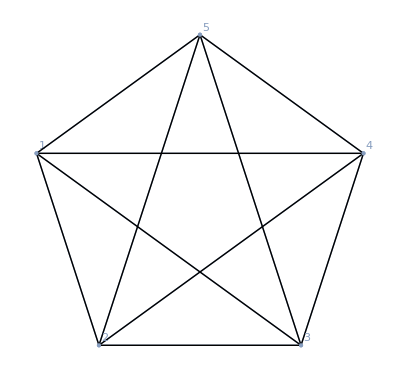

```mathematica
toFramework[CompleteGraph[5],MeshCellLabel->{0->"Index"}]
```

#### polygonLinkage[]

```mathematica
Options[polygonalLinkage]=Options[framework];

polygonalLinkage[ pts_?(MatrixQ[#,NumericQ]&), opt : OptionsPattern[] ]:=
framework[
	pts,
	rigidBar/@Partition[Range[Length[pts]],2,1,1],
	opt
] /; 1 < Last[Dimensions[pts]] ≤ 3

polygonalLinkage::pts="First argument must be a list of vertex locations in 2 or 3 dimensions.";
polygonalLinkage[_, OptionsPattern[]] := "nothing" /; Message[polygonalLinkage::pts];
```

#### KLChainUnitCell[]

```mathematica
Options[KLChainUnitCell]=Join[
	Options[framework],
	{
	"barColor"->Blue,
	"springColor"->Black
	}
];

KLChainUnitCell[xSpacing_,r_,t_,opt:OptionsPattern[]]:=
	framework[
	{
	{0,0},{r Cos[t],r Sin[t]},{xSpacing,0},{xSpacing,0}+{r Cos[t],-r Sin[t]},{2 xSpacing,0},{2 xSpacing,0}+r {Cos[t],Sin[t]}
	},
	{
	joint[1],joint[3],
	Property[rigidBar[{1,2}],MeshCellStyle->OptionValue["barColor"]],
	Property[rigidBar[{3,4}],MeshCellStyle->OptionValue["barColor"]],
	Property[rigidBar[{2,4}],MeshCellStyle->OptionValue["springColor"]],
	Property[rigidBar[{4,6}],MeshCellStyle->OptionValue["springColor"]]
	},
	Evaluate[FilterRules[{opt},Options[framework]]]
	]
```

#### randomCellNetwork[]

```mathematica
(*Build a periodic Voronoi mesh by tiling the vertices and extracting only the cells associated with the original vertices.*)

Options[randomCellNetwork]:=Join[{ "faces"->False, "map"->Identity }, Options[framework] ];

randomCellNetwork[numPoints_Integer?( #>0 & ), opt : OptionsPattern[]]:=Module[{i,j,selectedPrimitives, positions, mappedPositions},
With[{randomPoints=RandomReal[{-1/2,1/2},{numPoints,2}]},

	With[{expandedMesh=MeshPrimitives[VoronoiMesh[Flatten[Table[randomPoints+ConstantArray[{i,j},numPoints],{i,-1,1},{j,-1,1}],2]],2]},

		selectedPrimitives = Select[expandedMesh,Or@@RegionMember[#, randomPoints]&];
		positions = DeleteDuplicates[Flatten[selectedPrimitives[[All,1]],1]];
		mappedPositions = OptionValue["map"] /@ positions;

		With[{mesh = MeshRegion[positions, Polygon /@ Flatten /@ ( selectedPrimitives[[All,1]] /. PositionIndex[positions] )]},	

			If[ BooleanQ[OptionValue["faces"]] && OptionValue["faces"] == True,
				framework[ mappedPositions, MeshCells[mesh,2] /. Polygon->face, FilterRules[{opt}, Options[framework] ] ],
				framework[ mappedPositions, MeshCells[mesh,1] /. Line->spring, FilterRules[{opt}, Options[framework] ] ]
			]

		] /; If[ MatrixQ[mappedPositions,NumericQ] && Last[Dimensions[mappedPositions]]==2,
			True,
			Message[randomCellNetwork::map]; False
		]
	]]
]

randomCellNetwork[numPoints_, opt : OptionsPattern[]]:="nothing" /; Message[randomCellNetwork::num]

randomCellNetwork::map="Option \"map\" is not a function taking a point in 2D to a point in 2D.";
randomCellNetwork::num="Number of points should be a positive integer.";
```

#### randomTriangulatedNetwork[]

```mathematica
(*Build a periodic Voronoi mesh by tiling the vertices and extracting only the cells associated with the original vertices.*)

Options[randomTriangulatedNetwork]:=Join[{ "faces"->False, "map"->Identity }, Options[framework] ];

randomTriangulatedNetwork[numPoints_Integer?( #>0 & ), opt : OptionsPattern[]]:=Module[{i,j,selectedPrimitives, positions, mappedPositions},
With[{randomPoints=RandomReal[{-1/2,1/2},{numPoints,2}]},

	With[{expandedMesh=MeshPrimitives[DelaunayMesh[Flatten[Table[randomPoints+ConstantArray[{i,j},numPoints],{i,-1,1},{j,-1,1}],2]],2]},

		selectedPrimitives = Select[expandedMesh,Or@@RegionMember[#, randomPoints]&];
		positions = DeleteDuplicates[Flatten[selectedPrimitives[[All,1]],1]];
		mappedPositions = OptionValue["map"] /@ positions;

		With[{mesh = MeshRegion[positions, Polygon /@ Flatten /@ ( selectedPrimitives[[All,1]] /. PositionIndex[positions] )]},	

			If[ BooleanQ[OptionValue["faces"]] && OptionValue["faces"] == True,
				framework[ mappedPositions, MeshCells[mesh,2] /. Polygon->face, FilterRules[{opt}, Options[framework] ] ],
				framework[ mappedPositions, MeshCells[mesh,1] /. Line->spring, FilterRules[{opt}, Options[framework] ] ]
			]

		] /; If[ MatrixQ[mappedPositions,NumericQ] && Last[Dimensions[mappedPositions]]==2,
			True,
			Message[randomCellNetwork::map]; False
		]
	]]
]

randomTriangulatedNetwork[numPoints_, opt : OptionsPattern[]]:="nothing" /; Message[randomTriangulatedNetwork::num]

randomTriangulatedNetwork::map="Option \"map\" is not a function taking a point in 2D to a point in 2D.";
randomTriangulatedNetwork::num="Number of points should be a positive integer.";
```

### Constraints and rigidity

#### constraintVector[], reduceConstraintToOrder[]

```mathematica
(*get a set of user-specified constraints into the form of a vector equal to zero when constraints are satisfied*)
constraintVector[positions_,None]:={}
constraintVector[positions_,constraints_]:=With[
{
equations=Flatten[{equationToExpression[constraints]}],
dimensions=Dimensions[positions]
},
	equations /. Dispatch[displacementRules[ vertexPosition[ Range[dimensions[[1]]],All[dimensions[[2]]] ] - positions]]
]

equationToExpression[Equal[a_,b_]]:=a-b
equationToExpression[Equal[a_,b__]]:=ConstantArray[a,Length[{b}]]-{b}
equationToExpression[a:Except[_Equal]]:=a
SetAttributes[equationToExpression,Listable];
```

```mathematica
(*express the constraints to be valid at a certain order*)
reduceConstraintToOrder[positions_,constraintVector_,order_Integer?(#>=0&)]:=Module[
{
dimensions=Dimensions[positions],
expandedExpression,x
},
	expandedExpression = constraintVector /. Dispatch[ positionRules[ positions + x vertexDisplacement[Range[dimensions[[1]]], All[dimensions[[2]]]]]];
	Total[ D[expandedExpression,{x,#}]/Factorial[#]& /@ Range[0,order] /. x->0]
]
reduceConstraintToOrder[positions_,constraintVector_,_]:=constraintVector
```

#### solveLinearConstraints[], dynamicVariables[], processConstraintEquations[], nonlinearConstraintVector[]

```mathematica
(*Fastest way to pull out equations that are definitely linear and can be solved explicitly*)
linearEquationQ[eq_,var_]:=VectorQ[D[eq,{var}],NumericQ]

(*given a set constraints, select out the linear ones and solve them.*)
solveLinearEquations[constraintVec_, var_] := Module[ {soln},
	Quiet[ soln = Solve[ Select[ constraintVec, linearEquationQ[#, var]& ] == 0, var ] ];
	If[ Head[soln] =!= Solve, soln[[1]], {} ]
]
```

```mathematica
(*
	processConstraintEquations[ initial positions, constraint equations ]
*)
processConstraintEquations[positions_, constraintEq_] := 
Module[
{
	constraints = constraintVector[ positions, constraintEq ],
	vars = Flatten @ Array[ vertexPosition, Dimensions[positions] ],
	linearEquationSelector,
	solvedLinearConstraints,
	constrainedPositions
},
	linearEquationSelector = linearEquationQ[#, vars]& /@ constraints;
	solvedLinearConstraints = Quiet[ Solve[ Pick[ constraints, linearEquationSelector ] == 0, vars ] ];

	If[Head[solvedLinearConstraints] === Solve,
		Association[
			"linear solutions"->{}, 
			"constrained positions" -> Array[vertexPosition, Dimensions[positions] ],
			"nonlinear constraints" -> constraints
		],
	
		Association[
		(*rules that solve the linear constraints*)
		"linear solutions" -> First[solvedLinearConstraints],

		(*positions with linear solutions applied*)
		"constrained positions" -> ( constrainedPositions = Array[vertexPosition, Dimensions[positions]] /. Dispatch[First[solvedLinearConstraints]] ),

		(*remaining nonlinear constraints*)
		"nonlinear constraints" -> Pick[ constraints, linearEquationSelector, False ]
		]
	]
]

nonlinearConstraintVector[positions_, constraintEq_] := 
With[{ constraints = constraintVector[ positions, constraintEq ], vars = Flatten[ Array[vertexPosition, Dimensions[positions]] ] },
	Select[ constraints, linearEquationQ[#,vars]& /@ constraintEq]
]
```

```mathematica
(*this is an old version of the function that will be removed eventually*)
dynamicVariables[m_, pinnedVertices_,initialPositions_]:=
	DeleteDuplicatesBy[Cases[
		Transpose[{Flatten @ vertexPosition[m],Flatten @ initialPositions}] /. pinnedVertices,
		{_vertexPosition,_}
	], First ]

dynamicVariables[ positions_, processedConstraints_Association ] := dynamicVariables[ positions, processedConstraints["constrained positions"] ]
dynamicVariables[ positions_, constrainedPositions_ ] := 
	DeleteDuplicatesBy[ Cases[
		Transpose[ { Flatten @ constrainedPositions, Flatten @ positions } ],
		{_vertexPosition, _}
	], First ]
```

#### constraintEquations[]

```mathematica
Options[constraintEquations]:={"output"->vertexDisplacement, "constraints"->None, "pattern"->_}

constraintEquations[m_?mechanismQ, positions: _?vertexCoordinatesQ|Automatic : Automatic, order_ , OptionsPattern[] ]:=
With[
{
	actualPositions = If[ positions === Automatic, m["positions"], positions ],
	output = OptionValue["output"]
},
	constraintEquationsInternal[m, actualPositions, order, OptionValue["pattern"], OptionValue["constraints"], output ] /; Which[
		Not @ vertexCoordinatesQ[ m, positions ], Message[constraintEquations::pos]; False,
		Not @ Or[ IntegerQ[order] && order > 0, order === Infinity ], Message[constraintEquations::order]; False,
		Not @ MatchQ[output, vertexDisplacement|vertexPosition], Message[constraintEquations::output]; False,
		True, True
	]
]

constraintEquations::pos="Positions do not correspond to mechanism vertices.";
constraintEquations::output="Option \"output\" must be either vertexDisplacement or vertexPosition.";
constraintEquations::order="Order of expansion must be a positive integer or Infinity.";
```

```mathematica
constraintEquationsInternal[ m_, positions_, order_, pattern_, constraints_, output : vertexDisplacement | vertexPosition ] :=
With[{
userConstraints = constraintVector[positions, constraints],
variables = If[ output === vertexDisplacement, positions + vertexDisplacement[m], vertexPosition[m] ]
},
	Join[
		(*the internal constraints*)
		Flatten[ componentToConstraints[m, positions, variables, #, order ]& /@ mechanismComponents["constraints", m, pattern ] ],

		(*it is fairly straightforward to pull out just the constraint we wouldn't be able to solve explicitly, but present them at the right order*)	
		reduceConstraintToOrder[ positions, userConstraints , order ]
	]
]
```

```mathematica
componentToConstraints[m_, positions_, arbitraryPositions_, rigidBar[ indices_, data_Association ], 1 ]:=
	2 MapThread[#1 . #2&, 
		{
		mechanisms`Private`displacementVectorInternal[positions,indices],
		mechanisms`Private`displacementVectorInternal[arbitraryPositions-positions,indices]
		}
	]
componentToConstraints[m_, positions_, arbitraryPositions_, rigidBar[ indices_, data_Association ], _?(IntegerQ[#] && #>0 &)|Infinity ]:=
	mechanisms`Private`displacementLengthSquaredInternal[ arbitraryPositions, indices ] - data["length"]^2
```

```mathematica
componentToConstraints[m_, positions_, arbitraryPositions_, spring[ indices_, data_Association ], order_?(IntegerQ[#] && #>0&) ]:=
Module[{eps, displacements = Dispatch[displacementRules[arbitraryPositions - positions]] },With[
{
lengths=mechanisms`Private`displacementLengthInternal[ positions + infinitesimal[eps, order] vertexDisplacement[m], indices ]
},
	mechanisms`Private`expandExpression[ MapThread[#1[ #2, #3 ]&, {data["strain"], lengths, data["length"] }  ] ] /. infinitesimal[eps,order]->1 /. displacements
]]

componentToConstraints[m_, positions_, arbitraryPositions_, spring[ indices_, data_Association ], Infinity ]:=
With[ {lengths=mechanisms`Private`displacementLengthInternal[ arbitraryPositions, indices ]},
	MapThread[#1[ #2, #3 ]&, {data["strain"], lengths, data["length"] }  ]
]
```

```mathematica
componentToConstraints[m_, positions_, arbitraryPositions_, fold[ indices_, data_Association ], order_?(IntegerQ[#] && #>0 &) ]:=
Module[{eps, displacements = Dispatch[displacementRules[arbitraryPositions - positions]]},
	mechanisms`Private`foldAngleInternal[m, positions + infinitesimal[eps, order] vertexDisplacement[m], indices ] - data["angle"] /. infinitesimal[eps,order]->1 /. displacements
]
componentToConstraints[m_, positions_,arbitraryPositions_, fold[ indices_, data_Association ], Infinity ]:=
	mechanisms`Private`foldAngleInternal[m, arbitraryPositions, indices ] - data["angle"]
```

```mathematica
componentToConstraints[m_, positions_, arbitraryPositions_, joint[ indices_, data_Association ], order : _?(IntegerQ[#] && #>0 &)|Infinity ]:=
With[ {stiffness = Flatten[ data["stiffness"] ]},
	Pick[ Flatten[ arbitraryPositions[[ indices ]] - data["position"] ], stiffness, Infinity ]
]
```

```mathematica
componentToConstraints[m_, positions_, arbitraryPositions_, angleJoint[ indices_, data_Association ], order_?(IntegerQ[#] && #>0 &) ]:=
Module[{eps, displacementRules = Dispatch[displacementRules[arbitraryPositions - positions]]},
	mechanisms`Private`turningAngleInternal[ positions + infinitesimal[eps, order], indices ] - data["angle"] /. infinitesimal[eps,order]->1 /. displacementRules
]
componentToConstraints[m_, positions_, arbitraryPositions_, angleJoint[ indices_, data_Association ], Infinity ]:=
	mechanisms`Private`turningAngleInternal[ arbitraryPositions, indices ] - data["angle"]
```

```mathematica
componentToConstraints[m_, positions_, arbitraryPositions_, _, _]:={}
```

#### constraintMatrix[]

```mathematica
Options[constraintMatrix]={"constraints"->None, "pattern"->_, "rules"->{}};

constraintMatrix[m_?mechanismQ, positions : _?vertexCoordinatesQ|Automatic : Automatic, OptionsPattern[] ]:=
With[
{
actualPositions=If[positions===Automatic, m["positions"], positions]
},
	constraintMatrixInternal[ m, actualPositions, OptionValue["pattern"], OptionValue["constraints"], OptionValue["rules"] ] /; Which[
		Not @ vertexCoordinatesQ[m, actualPositions], Message[constraintMatrix::vcoord]; False,
		Not @ MatchQ[OptionValue["rules"], { Rule[vertexDisplacement[_,_], _]...}], Message[constraintMatrix::rules]; False,
		True, True
	]
]
```

```mathematica
reduceVariables[vars_,{}]:=vars
reduceVariables[vars_,rules_] := Cases[Variables[vars //. rules],_vertexDisplacement]

constraintMatrixInternal[m_, positions_, pattern_, constraints_, {} ]:=
With[
{constraintMatrices=CoefficientArrays[
	constraintEquationsInternal[m, positions, 1, pattern, constraints, vertexDisplacement],
	Flatten[vertexDisplacement[m]]
	]
},
	If[constraintMatrices=={{}},
		{ConstantArray[0,MeshCellCount[m,0] embeddingDimension[m]]},

		If[MatrixQ[positions, MachineRealQ],
			If[Chop[ constraintMatrices[[1]] . constraintMatrices[[1]] ] == 0,
				constraintMatrices[[2]],
				Message[constraintMatrix::stressed, N[constraintMatrices[[1]] . constraintMatrices[[1]]] ];
				constraintMatrices[[2]]
			],

			constraintMatrices[[2]]
		]
	]
]

(*
	It isn't efficient to make two functions like this but I am afraid of breaking the other version of this function.
*)
constraintMatrixInternal[m_, positions_, pattern_, constraints_,  rules_ ]:=
Module[{vars = reduceVariables[ Flatten[vertexDisplacement[m]], rules ]},
With[
{constraintMatrices=CoefficientArrays[
	constraintEquationsInternal[m, positions, 1, pattern, constraints, vertexDisplacement] //. rules,
	vars
	]
},
	If[constraintMatrices=={{}},
		{ConstantArray[0, Length[vars] ]},

		If[MatrixQ[positions, MachineRealQ],
			If[Chop[ constraintMatrices[[1]] . constraintMatrices[[1]] ] == 0,
				constraintMatrices[[2]],
				Message[constraintMatrix::stressed, N[constraintMatrices[[1]] . constraintMatrices[[1]]] ];
				constraintMatrices[[2]]
			],

			constraintMatrices[[2]]
		]
	]
]]

constraintMatrix::vcoord="Vertex positions do not match mechanism.";
constraintMatrix::stressed="Warning: Mechanism is stressed (residual is `1`). Constraint matrix may not be useful.";
constraintMatrix::rules="Replacement rules are not of the form { vertexDisplacement[v1, c1] -> .., .. }.";
```

#### compatibilityMatrix[]

```mathematica
compatibilityMatrix[m_?mechanismQ, positions : _?vertexCoordinatesQ|Automatic : Automatic]:=
With[{
actualPositions=If[positions===Automatic,m["positions"],positions],
indices=Cases[m["components"],_rigidBar][[1,1]]
},
	compatibilityMatrixInternal[m,actualPositions, indices] /; vertexCoordinatesQ[m,actualPositions]
]

compatibilityMatrix::nop="Specified positions do not match mechanism.";
compatibilityMatrix[m_?mechanismQ, _]:="nothing"/;Message[compatibilityMatrix::nop]
```

```mathematica
blowupEdge[2,positionDifference_][edgeIndex_,{c1_,c2_}]:=
With[{pos=2 positionDifference[[edgeIndex]]},
{
	{edgeIndex, 1+2 (c1-1)}->pos[[1]],
	{edgeIndex, 1+2 (c2-1)}->-pos[[1]],
	{edgeIndex, 2+2 (c1-1)}->pos[[2]],
	{edgeIndex, 2+2 (c2-1)}->-pos[[2]]
}]

blowupEdge[3,positionDifference_][edgeIndex_,{c1_,c2_}]:=
With[{pos=2 positionDifference[[edgeIndex]]},
{
	{edgeIndex, 1+3 (c1-1)}->pos[[1]],
	{edgeIndex, 1+3 (c2-1)}->-pos[[1]],
	{edgeIndex, 2+3 (c1-1)}->pos[[2]],
	{edgeIndex, 2+3 (c2-1)}->-pos[[2]],
	{edgeIndex, 3+3 (c1-1)}->pos[[3]],
	{edgeIndex, 3+3 (c2-1)}->-pos[[3]]
}]

compatibilityMatrixInternal[m_, positions_, indices_]:=
With[{
	edgeIndices = Range[Length[indices]], 
	d = embeddingDimension[m], 
	positionDifference = (#[[1]]-#[[2]]&) @ ((positions[[#]]&) /@ Transpose[indices])},
	SparseArray[ Flatten[ MapThread[ blowupEdge[d, positionDifference], {edgeIndices, indices}], 1 ] ]
]
```

#### zeroModes[], selfStresses[]

```mathematica
Options[zeroModes] = Join[ Options[constraintMatrix], Options[Eigensystem] , {Tolerance->10^(-10)}];

zeroModes::num="The constraint matrix is not numerical.";

zeroModes[m_?mechanismQ, opt : OptionsPattern[]]:=
Module[{
	mat=constraintMatrix[m, FilterRules[ {opt}, Options[constraintMatrix] ]],
	dim=embeddingDimension[m],
	evalues
},(
	evalues = Chop[Eigensystem[ Transpose[mat] . mat, FilterRules[ {opt}, Options[Eigenvalues] ]], OptionValue[Tolerance]];
	Partition[#, dim]& /@ Take[evalues[[2]], -Count[evalues[[1]],0]]
	) /; If[Not @ MatrixQ[mat, NumericQ],Message[zeroModes::num]; False, True]
]
```

```mathematica
Options[selfStresses] = Join[ Options[constraintMatrix], Options[Eigensystem] , {Tolerance->10^(-10)} ];

selfStresses[m_?mechanismQ, opt : OptionsPattern[]]:=
Module[{
	mat=constraintMatrix[m, FilterRules[ {opt}, Options[constraintMatrix] ]],
	evalues
},(
	evalues = Chop[Eigensystem[ mat . Transpose[mat] , FilterRules[ {opt}, Options[Eigenvalues] ]], OptionValue[Tolerance]];
	Take[evalues[[2]], -Count[evalues[[1]],0]]
	) /; If[Not @ MatrixQ[mat, NumericQ],Message[selfStresses::num]; False, True]
]
```

#### infinitesimalMotions[]

```mathematica
Options[infinitesimalMotions]=Join[{"constraints"->None, "variables"->Automatic}, Options[NullSpace] ];
```

```mathematica
infinitesimalMotions[m_?mechanismQ, positions: Except[_Rule] : Automatic, opt:OptionsPattern[]]:=
With[{
	actualPositions=If[positions===Automatic,m["positions"],positions]
},
	Module[
		{res=infinitesimalMotionsInternal[m,actualPositions,OptionValue["constraints"],OptionValue["variables"], FilterRules[{opt},Options[NullSpace]]]},
		res /; res=!=$Failed
	 ] /; vertexCoordinatesQ[m,actualPositions]
]

infinitesimalMotions::failed="Failed to find an appropriate solution. Check the constraints.";
infinitesimalMotions::pos="Positions do not match those of mechanism.";
infinitesimalMotions[m_?mechanismQ, positions : Except[Automatic|_Rule], OptionsPattern[]]:="nothing"/;
	Which[
		Not[vertexCoordinatesQ[m,positions]],
			Message[infinitesimalMotions::pos]; False,
		True, False
	]
```

```mathematica
infinitesimalMotions::var="Variables listed are not of the form vertexDisplacement[n,c].";
infinitesimalMotions::sing="Jacobian matrix is singular. Recovering using generic variables.";
infinitesimalMotions::jac="Jacobian matrix may not be invertible. Choosing different displacements may give better results.";
infinitesimalMotions::lin="Found `1` linear motions so `1` displacements are needed.";
```

```mathematica
infinitesimalMotionsInternal[m_,positions_,inputConstraints_,v_,nullspaceOptions_]:=
Module[{matrix,dependencies,solution},
With[{
variables=Flatten[vertexDisplacement[m]],

(*collect all the constraints valid to 2nd order in the displacements *)
equations=constraintEquationsInternal[m, positions, 2, _, inputConstraints, vertexDisplacement]
},
	(*linearize the equations*)
	matrix=CoefficientArrays[equations,variables, "Symmetric"->True];

	(*
	Find dependencies among the linear equations.

	When the constraints arise only from edge stretching, these dependences are the self-stresses.
	*)
	dependencies=Orthogonalize[NullSpace[Transpose[matrix[[2]]],nullspaceOptions]];

	(*the linear displacements that are allowed*)
	solution=linearMotionsToDisplacementRules[m,linearMotions[m,matrix[[2]],nullspaceOptions],v];

	Which[
		solution===$Failed, $Failed,

		Length[solution]>0,
			Expand[(*analytical processing that I prefer, but should not take a long time to perform*)
				{
				vertexDisplacement[m],
				If[Length[dependencies]>0,dependencies . equations,{}]
				}/.Dispatch[solution]
			],
		
		(*no solution but no errors either*)
		True,
			Message[infinitesimalMotions::failed];
			{{},{}}
	]
]]
```

```mathematica
linearMotionsToDisplacementRules[m_,linearMotions_,inputDisplacements_]:={} /; Length[linearMotions]==0

linearMotionsToDisplacementRules[m_,linearMotions_,inputDisplacements_List]:=
With[
(*preprocess arguments*)
{displacements=Flatten[{inputDisplacements}]},
Module[
{x,y,c,rules,jacobianMatrix,inverseJacobian,displacementIndices},
	displacementIndices=displacements/.vertexDisplacement[x_,y_]->{x,y}/.{"x"->1,"y"->2,"z"->3};
	jacobianMatrix=linearMotions[[All,Sequence@@#]]&/@displacementIndices;
	
	(*if inverting the jacobian fails entirely, we'll need to deal with that.*)
	inverseJacobian=Check[Inverse[jacobianMatrix],
		Message[infinitesimalMotions::sing];
		Return[linearMotionsToDisplacementRules[m,linearMotions,Automatic]],
		Inverse::sing
	];
	(*warn that the jacobian matrix is almost singular*)
	If[Abs[Det[jacobianMatrix]]<10^(-16),Message[infinitesimalMotions::jac]];

	rules=Thread[Array[c,Length[jacobianMatrix]]->inverseJacobian . Flatten[{displacements}]];
	Thread[Flatten[vertexDisplacement[m]]->Flatten[Array[c,Length[jacobianMatrix]] . linearMotions/.rules]]

]/; Length[linearMotions]==Length[displacements]&&MatchQ[displacements,{__vertexDisplacement}] ]

linearMotionsToDisplacementRules[m_,linearMotions_,Automatic]:=Module[{v=Unique[]},
	Thread[Flatten[vertexDisplacement[m]]->Flatten[Array[v,Length[linearMotions]] . linearMotions]]
]/;Length[linearMotions]>0

linearMotionsToDisplacementRules[m_,linearMotions_,c_Symbol]:=
	Thread[Flatten[vertexDisplacement[m]]->Flatten[Array[c,Length[linearMotions]] . linearMotions]]/;Length[linearMotions]>0
```

```mathematica
linearMotionsToDisplacementRules[m_,linearMotions_,displacements_]:=Which[
	Not[MatchQ[Flatten[{displacements}],{__vertexDisplacement}]],
		Message[infinitesimalMotions::var];
		$Failed,
	Length[linearMotions]≠Length[Flatten[{displacements}]],
		Message[infinitesimalMotions::lin,Length[linearMotions]];
		$Failed,
	True,
		$Failed
]
```

### Energy minimization

#### mechanismEnergy[]

```mathematica
$defaultStiffness["Methods"]:={rigidBar, spring, fold, joint, angleJoint, "constraints"}
$defaultStiffness[rigidBar]=1;
$defaultStiffness[spring]=1;
$defaultStiffness[fold]=10^(-4);
$defaultStiffness[joint]=10^(-4);
$defaultStiffness[angleJoint]=10^(-4);
$defaultStiffness["constraints"]=10^(-1);

$defaultStiffness::err="`1` does not have a default stiffness.";
$defaultStiffness[s_]:="nothing"/; Message[$defaultStiffness::err,s]
```

```mathematica
Options[mechanismEnergy]={"constraints"->None, "pattern" -> _};

mechanismEnergy[ m_?mechanismQ, positions_ : Automatic, opt : OptionsPattern[] ] :=
With[{actualPositions = If[ positions === Automatic, m["positions"], positions] },
	mechanismEnergyInternal[m, actualPositions, OptionValue["constraints"], OptionValue["pattern"] ] /; vertexCoordinatesQ[m, actualPositions]
]

mechanismEnergy::pos="Positions do not correspond to mechanism.";
mechanismEnergy[m_?mechanismQ, _, OptionsPattern[] ] := "nothing" /; Message[mechanismEnergy::pos]
```

```mathematica
mechanismEnergyInternal[ m_, positions_, constraints_, pattern_ ] := 
With[
{
	components = mechanismComponents[m, positions, pattern],
	nonlinearConstraints = nonlinearConstraintVector[positions, constraints],
	arbitraryPositions = vertexPosition[m]
},
	Total @ Flatten[{
	componentEnergy[m, arbitraryPositions, #]& /@ components,
	$defaultStiffness["constraints"] nonlinearConstraints . nonlinearConstraints/2
	}]
]

componentEnergy[m_, arbitraryPositions_, rigidBar[ indices_, data_Association ] ]:=With[
{
	stiffness = data["stiffness"] /. Infinity -> $defaultStiffness[rigidBar],
	length = data["length"]
},
	(* this form has the property that the elastic energy to apply a fixed strain to N beams in series is the same. *)
	stiffness ( displacementLengthSquared[arbitraryPositions, indices]/length^2 - 1 )^2/8
]

componentEnergy[m_, arbitraryPositions_, spring[ indices_, data_Association ] ]:=With[
{
	stiffness = data["stiffness"] /. Infinity -> $defaultStiffness[spring],
	length = data["length"], force = data["strain"]
},
	stiffness MapThread[#1[#2,#3]^2/2&, {force, displacementLength[arbitraryPositions, indices], length } ]
]

componentEnergy[m_, arbitraryPositions_, fold[ indices_, data_Association ] ]:=With[
{
	angle = data["angle"], stiffness = data["torsionalStiffness"] /. Infinity -> $defaultStiffness[fold]
},
	stiffness (foldAngle[m,arbitraryPositions, indices] - angle)^2/2
]

componentEnergy[m_, arbitraryPositions_, angleJoint[ indices_, data_Association ] ]:=With[
{
	angle = data["angle"], stiffness = data["angularStiffness"] /. Infinity -> $defaultStiffness[angleJoint]
},
	stiffness (turningAngle[arbitraryPositions,indices]-angle)^2/2
]

componentEnergy[m_, arbitaryPositions_, joint[ indices_, data_Association ] ]:=Module[
{
	stiffness = data["stiffness"] /. Infinity -> 0, positions = data["position"]
},
	MapThread[ #2 . DiagonalMatrix[#1] . #2/2 & , { stiffness, arbitaryPositions[[ indices ]] - positions } ]
]
```

#### compiledMechanismEnergy[] data structure

```mathematica
compiledMechanismEnergy[variables_List,energy_CompiledFunction,gradient_CompiledFunction]["variables"]:=variables

Format[compiledMechanismEnergy[variables_List,energy_CompiledFunction,gradient_CompiledFunction]]:=
StringJoin[
	"compiledMechanismEnergy[",
	If[Length[variables]<10,
		ToString[variables],
		"{"<>ToString[First[variables]<>"..."<>Last[variables]<>"}"]
	],
	"]"
]
```

```mathematica
compiledMechanismEnergy[variables_?VectorQ,energy_CompiledFunction,gradient_CompiledFunction]["data"]:=variables

compiledMechanismEnergy[variables_List,energy_CompiledFunction,gradient_CompiledFunction]["energy"][pos_?(VectorQ[#,NumericQ]&),data_] := energy[pos,data]
compiledMechanismEnergy[variables_List,energy_CompiledFunction,gradient_CompiledFunction]["gradient"][pos_?(VectorQ[#,NumericQ]&),data_] := gradient[pos,data]

compiledMechanismEnergy[variables_List,energy_CompiledFunction,gradient_CompiledFunction][v_?(VectorQ[#,NumericQ]&)] := compiledMechanismEnergy[v,energy,gradient]
```

#### compiledMechanismEnergyQ[], compiledNumericalMechanismEnergyQ[]

```mathematica
compiledMechanismEnergyQ[compiledMechanismEnergy[variables_,energy_CompiledFunction,gradient_CompiledFunction]]:=VectorQ[variables]
compiledMechanismEnergyQ[_]:=False

compiledNumericalMechanismEnergyQ[compiledMechanismEnergy[variables_,energy_CompiledFunction,gradient_CompiledFunction]]:=VectorQ[variables,NumericQ]
compiledNumericalMechanismEnergyQ[_]:=False
```

#### compiledMechanismEnergy[]

```mathematica
Options[compiledMechanismEnergy]:={"constraints"->None, "additional"->0};
```

```mathematica
compiledMechanismEnergy[m_?mechanismQ, pos : Except[_Rule] : Automatic,opt:OptionsPattern[]]:=
With[{actualPositions=If[pos===Automatic,m["positions"],pos]},
Module[
{res=compiledMechanismEnergyInternal[m,actualPositions,OptionValue["constraints"],OptionValue["additional"]]},
	res/;res=!=$Failed
]/;vertexCoordinatesQ[m,actualPositions]
]

compiledMechanismEnergy::pos="Provided positions do not correspond to mechanism.";
compiledMechanismEnergy[m_?mechanismQ, pos : Except[_Rule|Automatic],opt:OptionsPattern[]]:="nothing"/;Message[compiledMechanismEnergy::pos]
```

```mathematica
compiledMechanismEnergyInternal[m_,positions_,constraints_,additional_]:=
Module[
{
	symbols,energy=mechanismEnergy[m,positions,"constraints"->constraints]+additional
},
	symbols=DeleteDuplicates@Select[Cases[energy,_Symbol,Infinity],Not[NumericQ[#]]&];

	Check[
		compiledMechanismEnergy[
			symbols,
			compileEnergy[m,energy,symbols,$compilationTarget],
			compileGradient[m,energy,symbols,$compilationTarget]
		],
		$Failed
	]
]
```

```mathematica
compileEnergy[m_,energy_,symbols_,compiler_]:=Module[
{
body,
variables=Flatten[vertexPosition[m]],
injector,c,
dataInjector,data
},
	injector=Dispatch@Thread[variables->(Hold[c[[#]]]&/@Range[Length@variables])];
	dataInjector=Dispatch@Thread[symbols->(Hold[data[[#]]]&/@Range[Length@symbols])];
	body=energy/.injector/.dataInjector;
	ReleaseHold[Hold[Compile][
		{{c,_Real,1},{data,_Real,1}},
		body,
		RuntimeOptions->{"EvaluateSymbolically"->False},
		CompilationTarget->compiler
	]]
]
```

```mathematica
compileGradient[m_,energy_,symbols_,compiler_]:=Module[
{
body,
variables=Flatten[vertexPosition[m]],
injector,c,
dataInjector,data
},
	injector=Dispatch@Thread[variables->(Hold[c[[#]]]&/@Range[Length@variables])];
	dataInjector=Dispatch@Thread[symbols->(Hold[data[[#]]]&/@Range[Length@symbols])];
	body=D[energy,{variables}]/.injector/.dataInjector;
	ReleaseHold[Hold[Compile][
		{{c,_Real,1},{data,_Real,1}},
		body,
		RuntimeOptions->{"EvaluateSymbolically"->False},
		CompilationTarget->compiler
	]]
]
```

#### evaluateEnergy[]

```mathematica
evaluateEnergy[m_?mechanismQ, positions_?MatrixQ, energy: Except[_compiledMechanismEnergy]]:=
	energy /. Dispatch[positionRules[positions]]

evaluateEnergy[m_?mechanismQ, positions_?VectorQ, energy: Except[_compiledMechanismEnergy]]:=
	energy /. Dispatch[Thread[Flatten[vertexPosition[m]]->positions]]

evaluateEnergy[m_?mechanismQ, positions_?MatrixQ, energy_?compiledMechanismEnergyQ]:=
	energy[[2]][Flatten[positions],energy["data"]]

evaluateEnergy[m_?mechanismQ, positions_?VectorQ, energy_?compiledMechanismEnergyQ]:=
	energy[[2]][positions,energy["data"]]
```

#### analyticEnergyQ[]

```mathematica
analyticEnergyQ[Automatic,positions_]:=True
analyticEnergyQ[energyExpression_,positions_]:=With[
{number=N[energyExpression /. Dispatch[positionRules[positions]]]},
	Im[Chop[number]]==0&&NumericQ[number]&&Chop[Im[number]]==0
]
```

#### minimizeEnergy[]

```mathematica
Options[minimizeEnergy]=Join[ {"initial"->Automatic}, Options[mechanismEnergy], Options[FindMinimum] ];
SetAttributes[minimizeEnergy,HoldRest];

minimizeEnergy::badinitial="Initial conditions are not well-formed numeric positions matching the mechanism.";
minimizeEnergy::data="Data for compiled function not a vector of numerical values.";
minimizeEnergy::energy="Energy is not numerical at initial condition.";
```

```mathematica
minimizeEnergy[ m_?mechanismQ, energy : Except[_Rule] : Automatic, opt : OptionsPattern[]] :=
Module[{res = minimizeEnergyInternal[ m, energy, OptionValue["initial"], {opt} ] },
	res /; res =!= $Failed
]

minimizeEnergyInternal[ m_, energyExpression_, initial_, opt_ ] := Module[
{
	energy = minimizeEnergyComputeEnergy[m, energyExpression, opt ],
	initialPositions = minimizeEnergyInitialPositions[m, initial ],
	res
},
	If[energy =!= $Failed && initialPositions =!= $Failed,
		res = minimizeEnergyMinimize[ m, energy, initialPositions, opt ];
		If[ Length[ Dimensions[initial] ] == 3, res, First[res] ],
		$Failed
	]
]
```

```mathematica
minimizeEnergyInitialPositions[ m_, Automatic ] := {m["positions"]}
minimizeEnergyInitialPositions[ m_, initialPositions_?MatrixQ ] := {initialPositions} /; numericCoordinatesQ[m, initialPositions]
minimizeEnergyInitialPositions[ m_, initialPositions_?(ArrayQ[#,_,NumericQ]&) ] := initialPositions /; Dimensions[initialPositions][[2;;]] == {MeshCellCount[m,0],embeddingDimension[m]}

minimizeEnergyInitialPositions[ m_, pos_ ] := (Message[minimizeEnergy::badinitial]; $Failed)
```

```mathematica
minimizeEnergyComputeEnergy[ m_, Automatic, options_ ] := mechanismEnergy[m, FilterRules[{options}, Options[mechanismEnergy]] ]
minimizeEnergyComputeEnergy[ m_, energy_?compiledNumericalMechanismEnergyQ, options_ ] := energy
minimizeEnergyComputeEnergy[ m_, analyticEnergy_, options_ ] := analyticEnergy /; analyticEnergyQ[analyticEnergy, m["positions"]]

minimizeEnergyComputeEnergy[ m_, energy_?compiledMechanismEnergyQ, options_ ] := (Message[minimizeEnergy::data]; $Failed)
minimizeEnergyComputeEnergy[ m_, badEnergy_, options_ ] := (Message[minimizeEnergy::energy]; $Failed)
```

```mathematica
minimizeEnergyMinimize[ m_, energy_?compiledNumericalMechanismEnergyQ, initialPositions_, options_ ] :=
Module[
{
	constraintData = processConstraintEquations[ 
		m["positions"],
		constraintEquations[ m, m["positions"], Infinity, Flatten @ {"output" -> vertexPosition, FilterRules[options, Options[constraintEquations] ] } ]
	],
	data = energy["data"], allVariables = Flatten[vertexPosition[m]],
	variables, variableSpecifications, linearConstraints,
	
	minimizationOptions = Sequence @@ FilterRules[options, Options[FindMinimum]],
	minimizationResults
},
	variables = Flatten[constraintData[ "constrained positions" ]];
	variableSpecifications = Transpose[ {allVariables, Flatten @ #} ]& /@ initialPositions;

	(*turn the solved linear constraints into simple linear constraints*)
	linearConstraints = Equal @@@ constraintData[ "linear solutions" ];
	
	minimizationResults = Cases[
		(FindMinimum @@ {
			Flatten[{ energy["energy"][variables, data], linearConstraints }],
			Sequence @@ #,
			Gradient :> energy["gradient"][variables, data],
			minimizationOptions
		}) & /@ variableSpecifications,
		
		{ _?NumericQ, {__Rule}}
	];
	
	{ #[[1]] , constraintData["constrained positions"] /. Dispatch[ #[[2]] ] }& /@ minimizationResults
]

minimizeEnergyMinimize[ m_, energy_, initialPositions_, options_ ] := 
Module[
{
	constraintData = processConstraintEquations[
		m["positions"],
		constraintEquations[ m, m["positions"], Infinity, Flatten @ {"output" -> vertexPosition, FilterRules[options, Options[constraintEquations] ] } ]
	],
	constrainedEnergy, variableSpecifications,
	minimizationOptions = FilterRules[options,Options[FindMinimum]],
	minimizationResults
},
	variableSpecifications = dynamicVariables[ #, constraintData ]& /@ initialPositions;
	constrainedEnergy = energy /. constraintData["linear solutions"];

	minimizationResults = Cases[
		( FindMinimum @@ {constrainedEnergy, #, Sequence @@ minimizationOptions} )& /@ variableSpecifications,
		{ _?NumericQ, {__Rule}}
	];
	
	{ #[[1]] , constraintData["constrained positions"] /. Dispatch[ #[[2]] ] }& /@ minimizationResults
]
```

#### repeatedMinimizeEnergy[]

```mathematica
Options[repeatedMinimizeEnergy]=Join[{"MaxEnergy"->Infinity},Options[randomDisplacements],Options[minimizeEnergy]];
```

```mathematica
repeatedMinimizeEnergyInternal[m_, positions_, energy_, number_Integer?(#>0&), maxEnergy : _?NumericQ|Infinity, options_ ] := 
Module[{
displacementOptions = FilterRules[options, Options[randomDisplacements]],
minimizationOptions = FilterRules[options, Options[minimizeEnergy]],
res
},
	res = minimizeEnergyInternal[ m, energy, randomDisplacements[ positions, number, displacementOptions ], minimizationOptions ];
	Select[res, #[[1]] ≤ maxEnergy & ] /; res =!= minimizeEnergyInternal && res =!= $Failed
] /; numericCoordinatesQ[m, positions]

repeatedMinimizeEnergyInternal[m_, positions_, energy_, number_, maxEnergy_, options_] := "nothing" /; Which[
	Not[numericCoordinatesQ[m, positions]], Message[repeatedMinimizeEnergy::pos]; False,
	Not[ IntegerQ[number] && number > 0 ], Message[repeatedMinimizeEnergy::numneg]; False,
	Not[ NumericQ[maxEnergy] || maxEnergy == Infinity ], Message[repeatedMinimizeEnergy::max]; False,
	True, False
]
```

```mathematica
repeatedMinimizeEnergy[ m_?mechanismQ, energy : Except[_Integer] : Automatic, num_, opt : OptionsPattern[] ] :=
With[{positions = If[OptionValue["initial"]===Automatic, m["positions"], OptionValue["initial"] ] },
Module[{res = repeatedMinimizeEnergyInternal[ m, positions, energy, num, OptionValue["MaxEnergy"], {opt} ]},
	res /; Head[res] =!= repeatedMinimizeEnergyInternal
]]
```

```mathematica
repeatedMinimizeEnergy::numneg="Number of repetitions should be a positive integer.";
repeatedMinimizeEnergy::max="Option \"MaxEnergy\" does not have a valid value.";
repeatedMinimizeEnergy::pos="Initial positions are not numerical and valid.";
```

#### tallyRepeatedMinimizeEnergy[]

```mathematica
Options[tallyRepeatedMinimizeEnergy]=Join[Options[repeatedMinimizeEnergy],{SameTest -> Automatic}];

tallyRepeatedMinimizeEnergy[m_?mechanismQ,num_Integer,tol:_?NumericQ:10^(-6),opt:OptionsPattern[]]:=Module[{
res=repeatedMinimizeEnergy[m,num,opt]},
	tallyRepeatedMinimizeEnergyOutput[res,tol]/;Head[res]=!=repeatedMinimizeEnergy
]

tallyRepeatedMinimizeEnergy[m_?mechanismQ,energy_,num_Integer,tol:_?NumericQ:10^(-6),opt:OptionsPattern[]]:=Module[{
res=repeatedMinimizeEnergy[m,energy,num,opt]},
	tallyRepeatedMinimizeEnergyOutput[res,tol]/;Head[res]=!=repeatedMinimizeEnergy
]

tallyRepeatedMinimizeEnergyOutput[{},_]:={}
tallyRepeatedMinimizeEnergyOutput[res_,tol_]:=With[{output=Transpose[res]},
	{Max[output[[1]]],Tally[output[[2]], Flatten[#1-#2].Flatten[#1-#2]<tol^2& ]}
]
```

### Global rigidity and energetics

#### isometricTrajectory[]

```mathematica
Options[isometricTrajectory]={
"initial"->Automatic,
"constraints"->None,
Method->{}
};

(*options for specific methods*)
Options[isometricTrajectoryExplicitStep]={"stepsize"->0.1, "stepMethod"->"Minimization","stepOptions"->{MaxIterations->10^4}, Tolerance->10^(-8),"compile"->Automatic};
Options[isometricTrajectoryNDSolve]=Options[NDSolve];
```

```mathematica
isometricTrajectory::index="Index specification is not recognized.";

isometricTrajectory[m_?mechanismQ, directionSpecification_, indexing_, OptionsPattern[]]:=
Module[
{
	positions = If[OptionValue["initial"]===Automatic, m["positions"], OptionValue["initial"]],
	methodOptions = Sequence @@ Flatten[{OptionValue[Method]}],
	res
},
	res = If[numericCoordinatesQ[m,positions],
		Switch[indexing,
			{_, _?NumericQ, _?NumericQ}, isometricTrajectoryNDSolve[m, positions, directionSpecification, OptionValue["constraints"], indexing, methodOptions],
			_Integer, isometricTrajectoryExplicitStep[m, positions, directionSpecification, OptionValue["constraints"], indexing, methodOptions],
			_, Message[isometricTrajectory::index]; $Failed
		],
		$Failed
	];
	res /; Head[res] === List
]
```

```mathematica
isometricTrajectory::const="Constraints contain symbolic variables.";
isometricTrajectory::ener="Energy contains symbolic variables.";
isometricTrajectory::dir="Initial direction is not numerical or is not compatible with mechanism.";
isometricTrajectory::pos="Initial positions are not numerical or are not compatible with mechanism.";
isometricTrajectory::steps="Number of steps is not a positive integer.";
isometricTrajectory::stepsize="Option \"stepsize\" should be a positive, real number.";
isometricTrajectory::compile="Option \"compile\" should be a Boolean, Automatic, or a numerical compiledMechanismEnergy[].";
isometricTrajectory::meth="Method function `1` is not valid.";
isometricTrajectory::stfunc="Step function `1` is not valid.";
isometricTrajectory::meth="Method `1` is not recognized.";
```

```mathematica
(*
Explicit step methods.
*)
isometricTrajectoryExplicitStep[m_, positions_, initialDirection_, inputconstraints_, steps_, opt : OptionsPattern[]]:=
With[{constraints=constraintVector[positions,inputconstraints]},
	isometricTrajectoryStepperInternal[
		m,
		{positions,initialDirection},
		{steps,OptionValue["stepsize"]},
		{OptionValue["compile"],constraints},
		{OptionValue["stepMethod"],OptionValue[Tolerance],OptionValue["stepOptions"]}
	] /; Which[ (*argument checking*)
		Not[IntegerQ[steps] && steps>0], Message[isometricTrajectory::steps]; False,
		Not[NumericQ[OptionValue["stepsize"]]&&OptionValue["stepsize"]>0], Message[isometricTrajectory::stepsize]; False,
		Not[numericCoordinatesQ[m,positions+initialDirection]], Message[isometricTrajectory::dir]; False,
		Not[BooleanQ[OptionValue["compile"]]||OptionValue["compile"]===Automatic||compiledNumericalMechanismEnergyQ[OptionValue["compile"]]||analyticEnergyQ[OptionValue["compile"],positions]],
			 Message[isometricTrajectory::compile]; False,
		Not[MatchQ[OptionValue["stepMethod"],"Minimization"|"RandomWalk"|None]],
			Message[isometricTrajectory::meth,OptionValue[Method]]; False,
		True, True
]

] /; Which[Not[numericCoordinatesQ[m,positions]], Message[isometricTrajectory::pos]; False, True,True]
```

```mathematica
isometricTrajectoryStepperInternal[m_, {initialPositions_,initialDirection_},{steps_,stepsize_},{energy_,constraintVec_},{method_,tolerance_,stepOptions_}]:=
Module[{energyTemp,out},With[
{
variables=Flatten[vertexDisplacement[m]],
blankPositions=Flatten[vertexPosition[m]],
positions=Flatten[initialPositions],
initialDirectionNormalized=Normalize[Flatten[initialDirection]],

(*figure out the constraints we want to use at 1st order and at infinite order*)
firstOrderConstraints=Join[
	constraintEquationsInternal[m,vertexPosition[m],1,_,None,vertexDisplacement],
	reduceConstraintToOrder[vertexPosition[m],constraintVec,1]
	],
fullConstraints=Join[
	constraintEquationsInternal[m,initialPositions,Infinity,_,None,vertexPosition],
	constraintVec
]},
With[
{
(*this function will find the numerical 1st order constraint matrix*)
constraintMatFunction=(CoefficientArrays[firstOrderConstraints/.Dispatch[Thread[blankPositions->#]],variables][[2]]&),

(*figure out the energy we want to use*)
constraintEnergy=Which[
	energy===Automatic, fullConstraints . fullConstraints,
	energy===False, fullConstraints . fullConstraints,
	energy===True, compiledMechanismEnergy[{},
		compileEnergy[m,fullConstraints . fullConstraints,{},$compilationTarget],
		compileGradient[m,fullConstraints . fullConstraints,{},$compilationTarget]],
	True, energy (*user may be passing an energy*)
	]
},
	ArrayReshape[#,{Length[#],MeshCellCount[m,0],embeddingDimension[m]}]&[ FoldList[
		(*take one step*)
		(
		energyTemp=evaluateEnergy[m, #1[[1]], constraintEnergy];
		isometricTrajectoryStep[
			{method,stepsize,tolerance},
			m,
			#1, (*the latest position and step direction*)
			{constraintMatFunction[#1[[1]]],constraintEnergy}, (* {the matrix of linear constraints, an energy associated with the constraints} *)
			variables,
			stepOptions]
		)&,
		{positions,initialDirectionNormalized},
		Range[steps]
	][[All,1]] ]

]]]
```

```mathematica
isometricTrajectoryStep[{"Minimization",stepsize_,tolerance_},m_,{positions_,lastDirection_},{constraintMat_,constraintEnergy_},var_,stepOptions_]:=
Module[{
	nullspaceBasis=Orthogonalize[NullSpace[constraintMat,FilterRules[stepOptions,Options[NullSpace]]]],
	newDirection,
	trialStep , test
},
	newDirection=If[Length[nullspaceBasis]>0,
		Normalize[Transpose[nullspaceBasis] . nullspaceBasis . lastDirection],

		Message[isometricTrajectory::dirns,positions];
		ConstantArray[0,Length[positions]]
	];
	trialStep=positions+ stepsize newDirection;

	{
	If[ evaluateEnergy[m, trialStep, constraintEnergy] > tolerance,
		Flatten[
			minimizeEnergyInternal[m, constraintEnergy, Partition[positions+stepsize newDirection,embeddingDimension[m]], FilterRules[stepOptions, Options[FindMinimum]]][[2]]
		],
		trialStep
	],
	newDirection
	}
]

isometricTrajectoryStep[{"RandomWalk",stepsize_,tolerance_},m_,{positions_,lastDirection_},{constraintMat_,constraintEnergy_},var_,stepOptions_]:=
Module[{
nullspaceBasis=Orthogonalize[NullSpace[constraintMat,FilterRules[stepOptions,Options[NullSpace]]]],
newDirection,trialStep
},
	newDirection=If[Length[nullspaceBasis]>0,
		Normalize[RandomReal[{-stepsize,stepsize},Length[nullspaceBasis]] . nullspaceBasis],

		Message[isometricTrajectory::dirns,positions];
		ConstantArray[0,Length[positions]]
	];
	trialStep=positions+ stepsize newDirection;
	{
	If[ evaluateEnergy[m, trialStep, constraintEnergy] > tolerance,
		Flatten[minimizeEnergyInternal[m,constraintEnergy, Partition[positions+stepsize newDirection,embeddingDimension[m]], FilterRules[stepOptions,Options[FindMinimum]]][[2]]],
		trialStep
	],
	newDirection
	}
]

isometricTrajectoryStep[{None,stepsize_,tolerance_},m_,{positions_,lastDirection_},{constraintMat_,constraintEnergy_},var_,stepOptions_]:=
Module[{
	nullspaceBasis=Orthogonalize[NullSpace[constraintMat,FilterRules[stepOptions,Options[NullSpace]]]],
	newDirection
},
	newDirection=If[Length[nullspaceBasis]>0,
		Normalize[Transpose[nullspaceBasis] . nullspaceBasis . lastDirection],

		Message[isometricTrajectory::dirns,positions];
		ConstantArray[0,Length[positions]]
	];
	{positions+stepsize newDirection,newDirection}
]
```

```mathematica
(* A method based on NDSolve. I thought this might be faster or more robust than my explicit methods but it appears to be slower to run. *)

isometricTrajectory::oned="Constraints must have a linear 1D solution to use \"NDSolve\" method.";
isometricTrajectory::start="Starting configuration may be too close to a singularity.";

isometricTrajectoryNDSolve[m_, initial_, dir : +1|-1, constraints_, {t_, start_?NumericQ, end_?NumericQ}, opt : OptionsPattern[]]:=
Module[{i,j,
	initialPositions = Flatten[ initial ],
	solveOptions=FilterRules[{opt},Options[NDSolve]],
	v, variableNames,
	constraintMat=constraintMatrix[m, vertexPosition[m], "constraints"->constraints],
	tangentVector, equations, solution
},
	If[ (#[[2]] - #[[1]]&)[Dimensions[constraintMat]] ≠ 1, Message[isometricTrajectory::oned]; Return[$Failed]];

	variableNames = Flatten[vertexPosition[m]] /. vertexPosition[i_,j_]:>v[i,j][t];	
	tangentVector = dir (Cross @@ Normal[constraintMat] /. vertexPosition[i_,j_]:>v[i,j][t]);
	
	If[tangentVector . tangentVector < 10^(-12),Message[isometricTrajectory::start]];

	equations = Thread[
		Flatten[{
			D[variableNames,t] - tangentVector/Sqrt[tangentVector . tangentVector],

			(*initial conditions*)
			(variableNames /. t->start) - initialPositions
		}] == 0
	];

	solution = NDSolve[equations, variableNames, {t,start, end}, solveOptions];
	If[Head[solution] =!= NDSolve,
		(vertexPosition[m] /. vertexPosition[i_,j_]:>v[i,j][t]) /. First @ solution,
		$Failed
	]
]
```

#### findMinimalTrajectory[]

```mathematica
Options[findMinimalTrajectory]={
	"additional"->0,
	"constraints"->None,
	Method->{"ElasticBand", MaxIterations->10^5}
};
```

```mathematica
findMinimalTrajectory["Methods"]={{"ElasticBand", Join[{"stiffness"->10^(-4)},"Options[FindMinimum]"]}};

findMinimalTrajectory[ m_?mechanismQ, start_, end_, steps_, opt : OptionsPattern[] ]:=
Module[{method = Flatten[{OptionValue[Method]}], res},
	res = Switch[First[method],
		"ElasticBand",
			findMinimalTrajectoryElasticBand[m, start, end, steps, mechanismEnergy[m, "constraints"->OptionValue["constraints"]]+OptionValue["additional"], Sequence @@ Rest[method] ],
		_,
			Message[findMinimalTrajectory::meth];
			$Failed
	];
	
	res /; res =!= $Failed
]

findMinimalTrajectory::method="`1` is not a recognized method. Only \"ElasticBand\" is currently recognized.";
```

```mathematica
findMinimalTrajectory::ebstiff="Stiffness in \"ElasticBand\" method must be a positive numerical value.";
findMinimalTrajectory::ebstart="Start positions are not numeric coordinates corresponding to mechanism.";
findMinimalTrajectory::ebend="End positions are not numeric coordinates corresponding to mechanism.";
findMinimalTrajectory::steps="Number of steps should be a positive integer.";

ClearAll[findMinimalTrajectoryElasticBand];
Options[findMinimalTrajectoryElasticBand]=Join[{"stiffness"->10^(-4)},Options[FindMinimum]];

findMinimalTrajectoryElasticBand[m_, startPositions_,endPositions_, steps_, energy_, opt : OptionsPattern[]]:=
Module[{
stiffness = OptionValue["stiffness"],
fixedVertices = solveLinearEquations[constraintEquations[m,startPositions,Infinity,"output"->vertexPosition], Flatten[vertexPosition[m]] ], 
variable, internalVariables, partialEnergy, newVariables, potentialEnergy, initialConditions,
minimizationOptions = FilterRules[{opt},Options[FindMinimum]], solution
},

	Which[
		Not[ NumericQ[stiffness] && stiffness > 0 ],
			Message[findMinimalTrajectory::ebstiff]; Return[$Failed],
		Not @ numericCoordinatesQ[m, startPositions],
			Message[findMinimalTrajectory::ebstart]; Return[$Failed],
		Not @ numericCoordinatesQ[m, endPositions],
			Message[findMinimalTrajectory::ebend]; Return[$Failed],
		Not[ IntegerQ[steps] && steps>0 ],
			Message[findMinimalTrajectory::steps]; Return[$Failed]
	];

	internalVariables= Join[
		{positionRules[startPositions]},
		Flatten[MapThread[ #1 -> #2&, {vertexPosition[m], #}, 2],2]& /@ Array[variable, {steps, MeshCellCount[m,0],embeddingDimension[m]}],
		{positionRules[endPositions]}
	];

	newVariables = Flatten[vertexPosition[m] /. fixedVertices] /. internalVariables;

	partialEnergy = energy /. fixedVertices;

	potentialEnergy = Total @ Flatten @ {
	(*local equations*)
	(partialEnergy /. # &) /@ internalVariables,

	(*elastic band equations*)
	(stiffness (#[[2]]-#[[1]]) . (#[[2]]-#[[1]])&) /@ Partition[newVariables, 2, 1]
	};

	initialConditions = DeleteCases[ 
		Transpose @ {Flatten[ Drop[ Rest @ newVariables, -1] ], Flatten[startPositions + (endPositions - startPositions)/(steps+1) #& /@ Range[steps] ]},
		{_?NumericQ, _}
	];

	solution = FindMinimum @@ {potentialEnergy, initialConditions, minimizationOptions };
	If[Head[solution] =!= FindMinimum, Partition[#,embeddingDimension[m]]& /@ (newVariables /. solution[[2]]), $Failed]
]
```

#### dynamicalSystem[], dynamicalSystemEquations[]

```mathematica
Options[dynamicalSystemEquations]={
	"constraints"->None, (*a list of constraints*)
	"mass"->1,
	"drag"->0,
	"additional"->0 (*additional terms to add to the energy*)
};

Options[dynamicalSystem]=Join[
	Options[dynamicalSystemEquations],
	Options[NDSolve]
];
```

```mathematica
dynamicalSystemEquations::drag="Option \"drag\" cannot be parsed.";
dynamicalSystemEquations::mass="Option \"mass\" cannot be parsed.";
dynamicalSystemEquations::pos="Not a valid set of positions.";
dynamicalSystemEquations::var="Variables should be of the form {variable, time}.";
```

```mathematica
validEquationsParamQ[value_?NumericQ]:=value ≥ 0
validEquationsParamQ[value : Except[_List]]:=Not[NumericQ[value]]
validEquationsParamQ[_]:=False

expandEquationDrags[m_, drags_?validEquationsParamQ]:=ConstantArray[drags, MeshCellCount[m,0] ]
expandEquationDrags[m_, drags : {__?validEquationsParamQ}]:=drags /; Length[drags]==MeshCellCount[m,0]
expandEquationDrags[m_, None]:=ConstantArray[0, MeshCellCount[m,0] ]
expandEquationDrags[m_, _]:=(Message[dynamicalSystemEquations::drag]; $Failed)

expandEquationMasses[m_, masses_?validEquationsParamQ]:=ConstantArray[masses, MeshCellCount[m,0] ]
expandEquationMasses[m_, masses : {__?validEquationsParamQ}]:=masses /; Length[masses]==MeshCellCount[m,0]
expandEquationMasses[m_, None | 0]:=None
expandEquationMasses[m_, _]:=(Message[dynamicalSystemEquations::mass]; $Failed)

evaluateEquationPositions[m_, Automatic]:=m["positions"]
evaluateEquationPositions[m_, positions_]:=positions /; vertexPositionsQ[m,positions]
evaluateEquationPositions[m_, _]:=(Message[dynamicalSystemEquations::pos]; $Failed)
```

```mathematica
dynamicalSystemEquations[m_?mechanismQ, initialPositions_ : Automatic, {variableName_Symbol, timeVariable_Symbol}, opt : OptionsPattern[] ]:=
Module[{
energy = mechanismEnergy[m, "constraints" -> OptionValue["constraints"]] + OptionValue["additional"],
positions = evaluateEquationPositions[m,initialPositions],
drags = expandEquationDrags[m, OptionValue["drag"]],
masses = expandEquationMasses[m, OptionValue["mass"]]
},
	With[{res=dynamicalSystemEquationsInternal[m, positions, variableName, timeVariable, masses, drags, energy ]},
		res /; res =!= $Failed
	] /; drags =!= $Failed && masses =!= $Failed && positions =!= $Failed && variableName =!= timeVariable
]

dynamicalSystemEquations[m : mechanismPattern, initialPositions_ : Automatic, {_,_}, OptionsPattern[]]:="nothing" /; Message[dynamicalSystemEquations::vars]
dynamicalSystemEquations[m : mechanismPattern, initialPositions_ : Automatic, Except[_List] , OptionsPattern[]]:="nothing" /; Message[dynamicalSystemEquations::vars]
```

```mathematica
dynamicalSystem::drag="Option \"drag\" cannot be parsed.";
dynamicalSystem::mass="Option \"mass\" cannot be parsed.";
dynamicalSystem::timespec="The last argument should be of the form {time variable, start time, end time} with start and end times being numerical and the time variable being a Symbol.";
```

```mathematica
validDynamicalParamQ[value_]:=NumericQ[value] && value ≥ 0

expandDynamicalDrags[m_, drags_?validDynamicalParamQ]:=ConstantArray[drags, MeshCellCount[m,0] ]
expandDynamicalDrags[m_, drags : {__?validDynamicalParamQ}]:=drags /; Length[drags]==MeshCellCount[m,0]
expandDynamicalDrags[m_, None]:=ConstantArray[0, MeshCellCount[m,0] ]
expandDynamicalDrags[m_, _]:=(Message[dynamicalSystem::drag]; $Failed)

ClearAll[expandDynamicalMasses];
expandDynamicalMasses[m_, None | 0]:= None
expandDynamicalMasses[m_, masses_?validDynamicalParamQ]:= ConstantArray[masses, MeshCellCount[m,0] ]
expandDynamicalMasses[m_, masses : {__?validDynamicalParamQ}]:= masses /; Length[masses] == MeshCellCount[m,0]
expandDynamicalMasses[m_, _]:=(Message[dynamicalSystem::mass]; $Failed)
```

```mathematica
parseInitialConditions[m_, positions : _?MatrixQ | Automatic]:={parsePositions[m, positions], parseVelocities[m, None]}
parseInitialConditions[m_, {positions : _?MatrixQ | Automatic, velocities_?MatrixQ}]:={parsePositions[m, positions], parseVelocities[m, velocities]}
parseInitialConditions[m_, _]:=$Failed

parsePositions[m_, Automatic]:=m["positions"]
parsePositions[m_, positions_?MatrixQ]:=positions /; numericCoordinatesQ[m,positions]
parsePositions[m_, positions_?MatrixQ]:=$Failed

parseVelocities[m_, velocities_]:= velocities /; numericCoordinatesQ[m, velocities]
parseVelocities[m_, None]:= ConstantArray[0, {MeshCellCount[m,0], embeddingDimension[m]}]
```

```mathematica
dynamicalSystem[m_?mechanismQ, initialConditions_ : Automatic, {time_Symbol, start_?NumericQ, end_?NumericQ}, opt : OptionsPattern[] ]:=
Module[{
energy = mechanismEnergy[m, "constraints" -> OptionValue["constraints"]] + OptionValue["additional"],
parsedInitialConditions = parseInitialConditions[m, initialConditions],
drags = expandDynamicalDrags[m, OptionValue["drag"]],
masses = expandDynamicalMasses[m, OptionValue["mass"]]
},
	With[{res=dynamicalSystemInternal[m, masses, drags, parsedInitialConditions, energy, {time, start, end}, FilterRules[{opt}, Options[NDSolve]] ]},
		res /; res =!= $Failed
	] /; drags =!= $Failed && masses =!= $Failed && parsedInitialConditions =!= $Failed
]

dynamicalSystem[m : mechanismPattern, _ : Automatic, {_,_,_} ]:="nothing" /; Message[dynamicalSystem::timespec]
dynamicalSystem[m : mechanismPattern, _ : Automatic, Except[_List] ]:="nothing" /; Message[dynamicalSystem::timespec]
```

```mathematica
dynamicalSystemEquationsInternal[m_, initialPositions_, v_, timeVariable_, masses_, drags_, energy_]:=
Module[{pinnedVertices = Dispatch[ solveLinearEquations[constraintEquations[m,initialPositions,Infinity,"output"->vertexPosition], Flatten[vertexPosition[m]] ] ], 
variables, gradient, equationSystem, i, j, t},
	variables=vertexPosition[m] /. pinnedVertices /. vertexPosition[i_, j_] :> v[i, j][t];
	gradient=Partition[ D[ energy, { Flatten[ vertexPosition[m] ] }], embeddingDimension[m] ] /. pinnedVertices /. vertexPosition[i_, j_] :> v[i, j][t];
	
	equationSystem = Flatten[
		If[masses === None, ConstantArray[0, Dimensions[initialPositions] ], DiagonalMatrix[ masses ] . D[ variables, {t, 2} ] ] 
			+ DiagonalMatrix[ drags ] . D[ variables, {t, 1} ] + gradient
	] /. t->timeVariable;

	(*we need to explicitly eliminate the equations that are predetermined by the pinned vertices or there will be too many equations*)
	Pick[ equationSystem, Not[ NumericQ[#] ]& /@ Flatten[variables] ]
]
```

```mathematica
dynamicalSystemInternal[m_, masses_, drags_, {initialPositions_, initialVelocities_}, energy_, {timeVariable_, start_, end_}, opt_]:=
Module[{equations, v, variables, processedVariables, solution, i, j, 
pinnedVertices = Dispatch[ solveLinearEquations[constraintEquations[m,initialPositions,Infinity,"output"->vertexPosition], Flatten[vertexPosition[m]] ] ]},
	(*list only the non-pinned variables*)
	variables = Flatten[ vertexPosition[m] /. pinnedVertices /. vertexPosition[i_, j_] :> v[i, j][timeVariable] ];

	equations = Flatten[{
		(*the dynamical system equations*)
		dynamicalSystemEquationsInternal[m, initialPositions, v, timeVariable, masses, drags, energy],

		(*initial positions*)
		Select[ Flatten[ (variables /. timeVariable->0) - Flatten[initialPositions]], Not[ NumericQ[ # ] ]& ],

		(*initial velocities if needed*)
		If[masses === None,
			{},
			Select[ (( D[ variables, timeVariable ] /. timeVariable->0 ) - Flatten[initialVelocities]), Not[ NumericQ[ # ] ]& ]
		]
	}];
	
	solution = NDSolve[ Thread[ equations == 0 ],  Select[ variables, Not[ NumericQ[#] ] & ], {timeVariable, start, end }, opt ];

	(*did NDSolve return a list of rules?*)
	If[MatchQ[solution,{{__Rule}}],
		vertexPosition[m] /. pinnedVertices /. vertexPosition[i_, j_] :> v[i, j][timeVariable] /. solution[[1]],
		$Failed
	]
]
```

## end

```mathematica
End[];

EndPackage[];
```

```mathematica
m=framework[{{0,0},{1,0}},{rigidBar[{1,2}]}];
```

```mathematica
constraintMatrix[m]
```

SparseArray[…]

```mathematica
constraintEquations[m,1]
```

{2 (-vertexDisplacement[1,x]+vertexDisplacement[2,x])}

```mathematica
mechanismEnergy[m]
```

1/2 (-1+(-vertexPosition[1,x]+vertexPosition[2,x])^2+(-vertexPosition[1,y]+vertexPosition[2,y])^2)^2

```mathematica
infinitesimalMotions[m]
```

{{{($11[2])/(√2),$11[3]},{($11[2])/(√2),$11[1]}},{}}

## origami sub-package

```mathematica
BeginPackage["mechanisms`origami`"];
```

## usage

```mathematica
kawasakiQ::usage=
"kawasakiQ[origami] returns True if it can be determined that the origami satisfies Kawasaki's theorem at each vertex.
Use option ZeroTest to modify how the function tests for zero. Use option WorkingPrecision to set a number of digits for the test.";
```

```mathematica
foldMatrix::usage=
"foldMatrix[origami] returns the fold matrix mapping linear vertex displacements to linear fold angle changes.";

angularFoldMatrix::usage=
"angularFoldMatrix[origami, (positions, ) vertex] returns the angular fold matrix of a vertex mapping the angular displacements of the folds from the xy plane to the fold angle changes.";
```

```mathematica
toOrigami::usage=
"toOrigami[ object ] converts an object to an origami mechanism. Effectively this only works for some MeshRegion[] or framework[] objects.";
```

```mathematica
singleVertex::usage=
"singleVertex[ {angle 1, angle 2, ...} ] returns a single vertex origami with angles as sector angles.
singleVertex[ {angle 1, angle 2, ...}, {length 1, ...} ] returns a single vertex origami with angles as sector angles and fold lengths given by the list of lengths.

See options \"angles\" and \"torsional stiffnesses\" to set the equilibrium angles and torsional stiffnesses.";

randomOrigami::usage=
"randomOrigami[ n ] returns random origami with n internal vertices.";

miuraOri::usage=
"miuraOri[ angle ] returns a Miura ori at a particular angle.";
```

```mathematica
flatOrigamiQ::usage=
"flatOrigamiQ[ origami ] returns True if the origami mechanism is flat.
Use option ZeroTest to specify how to test for zero. Use option WorkingPrecision to choose the precision.";
```

```mathematica
yoshimuraOrigami::usage=
"yoshimuraOrigami[{# azimuthal cells, # of rings(, twist)},overall scale, height ratio] creates a Yoshimura fold pattern of a particular radius, height, and integer twist if specified.";
```

```mathematica
MVAssignment::usage = "MVAssignment[ o (, positions), tolerance_ (, assignmentFunction)] returns a list of rules assigning a value to mountain or valley folds up to the value of tolerance.
The function assignmentFunction should take one of the values {-1,0,1} for valley, flat, or mountain folds respectively.";

flattenOrigami::usage = "flattenOrigami[m, tolerance] attempts to flatten an origami structure.";
```

```mathematica
foldCongruentQ::usage="foldCongruentQ[ origami, positions1, positions2, tolerance] returns True if two sets of origami positions have sufficiently close fold angles.
foldCongruentQ[ {origami, folds}, positions1, positions2, tolerance] compares only the folds listed.
foldCongruentQ[ {origami, folds}, tolerance] can be applied to a pair of positions.";
```

```mathematica
butterflyDecompositionQ::usage = "butterflyDecompositionQ[ origami ] returns True if origami can be decomposed into pairs of \"butterfly\" faces.";
butterflyDecomposition::usage = "butterflyDecomposition[ origami ] returns a list of \"butterfly\" face pairs and a non-butterfly-decomposible kernel after removing butterfly faces. You can apply deleteDanglingVertices[] to extract the underlying origami structure.";
```

## body

```mathematica
Begin["`Private`"];

Needs["mechanisms`"];
Needs["mechanisms`rigidity`"];
```

### origami structures

#### toOrigami[]

```mathematica
toOrigami::notsurface="Input does not seem to be origami compatible because it is not a valid surface.";
```

```mathematica
surfaceQ[mr_]:=MeshRegionQ[mr]&&(And@@(Length[#]≤2&/@mechanisms`Private`connectivity[mr,"edges"->"faces"]))
toOrigami[mr_?surfaceQ]:=origami[MeshCoordinates[mr],MeshCells[mr,2]/.Polygon->face]

toOrigami[mr_framework]:=Module[{test},
	Check[
		test=toOrigami[mr["mesh"]];
		test["positions"->mr["positions"]],
		Message[toOrigami::notsurface];
		$Failed
	]
]
```

```mathematica
toOrigami[mr_MeshRegion]:="nothing" /; Message[toOrigami::notsurface]
```

#### singleVertex[]

```mathematica
Options[singleVertex]=Join[
	Options[origami],
	{
	"angles"->None,
	"torsionalStiffnesses"->None
	}
];

vertexOptionQ[None,_]:=True
vertexOptionQ[x_?VectorQ,n_Integer]:=Length[x]==n
vertexOptionQ[_,_]:=False
```

```mathematica
angleData[stiffnesses_List,angles_List]:=MapThread[Property[fold[{1,#1}],{"torsionalStiffness"->#2,"angle"->#3}]&,{Range[2,Length[stiffnesses]+1],stiffnesses,angles}]
angleData[None,angles_List]:=MapThread[Property[fold[{1,#1}],{"torsionalStiffness"->0,"angle"->#2}]&,{Range[2,Length[angles]+1],angles}]
angleData[stiffnesses_List,None]:=MapThread[Property[fold[{1,#1}],{"torsionalStiffness"->#2,"angle"->0}]&,{Range[2,Length[stiffnesses]+1],stiffnesses}]
angleData[None,None]:={}
```

```mathematica
singleVertex[angles:{__?NumericQ}, opt : OptionsPattern[]]:=
	singleVertexCreator[
		angles,ConstantArray[1,Length[angles]],
		angleData[OptionValue["torsionalStiffnesses"],OptionValue["angles"]],
		FilterRules[{opt},Options[MeshRegion]]
	]/; (
		(*check the options to make sure they make sense*)
		Length[angles]>2&&vertexOptionQ[OptionValue["angles"],Length[angles]]&&vertexOptionQ[OptionValue["torsionalStiffnesses"],Length[angles]]
	)
singleVertex[angles : {__?NumericQ}, lengths : {__?NumericQ}, opt : OptionsPattern[]]:=
	singleVertexCreator[
		angles,lengths,
		angleData[OptionValue["torsionalStiffnesses"],OptionValue["angles"]],
		FilterRules[{opt},Options[MeshRegion]]
	]/; (
		(*check the options to make sure they make sense*)
		Length[angles]>2&&Length[angles]==Length[lengths]&&vertexOptionQ[OptionValue["angles"],Length[angles]]&&vertexOptionQ[OptionValue["torsionalStiffnesses"],Length[angles]]
	)

singleVertex::sectorangles="Sector angles are not a vector of numerical values.";
singleVertex::length="Lengths are not a vector of numerical values.";
singleVertex::lengthmatch="Number of sector angles does not agree with number of lengths.";
singleVertex::folds="Number of fold stiffnesses does not match number of sector angles.";
singleVertex::angles="Number of fold angles does not match number of sector angles.";

singleVertex[angles_List,OptionsPattern[]]:="nothing"/;Which[
	Not@VectorQ[angles,NumericQ],Message[singleVertex::sectorangles],
	Not@vertexOptionQ[OptionValue["torsionalStiffnesses"],Length[angles]],Message[singleVertex::folds],
	Not@vertexOptionQ[OptionValue["angles"],Length[angles]],Message[singleVertex::angles]
]
singleVertex[angles_List,lengths_List,OptionsPattern[]]:="nothing"/;Which[
	Not@VectorQ[angles,NumericQ],Message[singleVertex::sectorangles],
	Not@VectorQ[lengths,NumericQ],Message[singleVertex::length],
	Length[angles]!=Length[lengths],Message[singleVertex::lengthmatch],
	Not@vertexOptionQ[OptionValue["torsionalStiffnesses"],Length[angles]],Message[singleVertex::folds],
	Not@vertexOptionQ[OptionValue["angles"],Length[angles]],Message[singleVertex::angles]
]
```

```mathematica
Options[singleVertexCreator]=Options[MeshRegion];

(*for Gaussian curvature zero vertices*)
singleVertexCreator[angles_,lengths_,extraCells_,opt:OptionsPattern[]]:=
Module[{tmp},With[
{
	foldDirections=Accumulate[angles],
	vertices=Range[2,Length[angles]+1]
},
	origami[
		(*construct vertex locations*)
		Join[{{0,0}},MapThread[#2 {Cos[#1],Sin[#1]}&,{foldDirections,lengths}]],
		Join[
			(*should folds be just edges or torsional springs?*)
			extraCells,
			(*there may be some redundancy here with the extra cells*)
			rigidBar[{1,#}]&/@vertices,
			(*rigid bars around boundary *)
			rigidBar/@(tmp=Partition[vertices,2,1,1]),
			(* faces are just polygons *)
			Polygon[Join[{1},#]]&/@tmp
		],
		opt
	]
]]/;PossibleZeroQ[Total[angles]-2 Pi]
```

```mathematica
singleVertex::notflat="Not able to handle non-flat vertices (yet).";
singleVertexCreator[__]:="nothing"/;Message[singleVertex::notflat]
```

#### miuraOri[]

```mathematica
Options[miuraOri]=Join[Options[origami],
{
	"Size"->{1/2,1/2}, (* Unit cell square size *)
	"Triangulated"->False,
	"primitive"->False
}];
```

```mathematica
miuraOriFaces[False,False]:={
		Polygon[{4,5,2,1}],Polygon[{6,4,1,3}],
		Polygon[{9,7,4,6}],Polygon[{7,8,5,4}],
		Polygon[{12,10,7,9}],Polygon[{10,11,8,7}],
		
		Line[{4,5}],Line[{5,2}],Line[{2,1}],Line[{1,4}],
		Line[{6,4}],Line[{1,3}],Line[{3,6}],
		Line[{6,9}],Line[{9,12}],Line[{12,10}],Line[{10,11}],
		Line[{11,8}],Line[{8,5}],
		Line[{7,4}],Line[{7,9}],Line[{7,10}],Line[{7,8}]
}

miuraOriFaces[True,False]:={
		Polygon[{4,5,2}],Polygon[{4,2,1}],Polygon[{6,4,1}],Polygon[{6,1,3}],
		Polygon[{9,7,6}],Polygon[{7,4,6}],Polygon[{7,8,4}],Polygon[{8,5,4}],
		Polygon[{12,10,7}],Polygon[{12,7,9}],Polygon[{10,11,8}],Polygon[{10,8,7}],
		
		Line[{4,5}],Line[{5,2}],Line[{2,1}],Line[{1,4}],
		Line[{6,4}],Line[{1,3}],Line[{3,6}],
		Line[{6,9}],Line[{9,12}],Line[{12,10}],Line[{10,11}],
		Line[{11,8}],Line[{8,5}],
		Line[{7,4}],Line[{7,9}],Line[{7,10}],Line[{7,8}],
		
		Property[Line[{6,1}],{MeshCellStyle->GrayLevel[0.65]}],
		Property[Line[{4,2}],{MeshCellStyle->GrayLevel[0.65]}],
		Property[Line[{4,8}],{MeshCellStyle->GrayLevel[0.65]}],
		Property[Line[{6,7}],{MeshCellStyle->GrayLevel[0.65]}],
		Property[Line[{12,7}],{MeshCellStyle->GrayLevel[0.65]}],
		Property[Line[{10,8}],{MeshCellStyle->GrayLevel[0.65]}]
}

miuraOriFaces[False,True]:={
		Polygon[{4,5,2,1}],Polygon[{6,4,1,3}],
		Polygon[{9,7,4,6}],Polygon[{7,8,5,4}],
		
		Line[{4,5}],Line[{5,2}],Line[{2,1}],Line[{1,4}],
		Line[{6,4}],Line[{1,3}],Line[{3,6}],
		Line[{6,9}],Line[{9,7}],Line[{7,8}],Line[{8,5}],
		Line[{7,4}]
}

miuraOriFaces[True,True]:={
		Polygon[{4,5,2}],Polygon[{4,2,1}],Polygon[{6,4,1}],Polygon[{6,1,3}],
		Polygon[{9,7,6}],Polygon[{7,4,6}],Polygon[{7,8,4}],Polygon[{8,5,4}],
		
		Line[{4,5}],Line[{5,2}],Line[{2,1}],Line[{1,4}],
		Line[{6,4}],Line[{1,3}],Line[{3,6}],
		Line[{6,9}],Line[{9,7}],Line[{7,8}],Line[{8,5}],
		Line[{7,4}],
		
		Property[Line[{6,1}],{MeshCellStyle->GrayLevel[0.65]}],
		Property[Line[{4,2}],{MeshCellStyle->GrayLevel[0.65]}],
		Property[Line[{4,8}],{MeshCellStyle->GrayLevel[0.65]}],
		Property[Line[{6,7}],{MeshCellStyle->GrayLevel[0.65]}]

}
```

```mathematica
miuraOri["Properties"]:={"HorizontalShift","AcuteAngle"}
```

```mathematica
miuraOri["HorizontalShift"[shift_],opt:OptionsPattern[]]:=With[
{
	sizex=OptionValue["Size"][[1]],sizey=OptionValue["Size"][[2]]
},
origami[
	Take[{
		{0,2 sizey},{sizex,2 sizey},{-sizex,2 sizey},
		{shift,sizey},{sizex+shift,sizey},{-sizex+shift,sizey},
		{0,0},{sizex,0},{-sizex,0},
		{shift,-sizey},{shift+sizex,-sizey},{shift-sizex,-sizey}
		},
		If[OptionValue["primitive"],9,12]
	],
	Flatten@{
		Point[#]&/@Range[If[OptionValue["primitive"],9,12]],
		miuraOriFaces[OptionValue["Triangulated"],OptionValue["primitive"]]/.Line->rigidBar
	},
	FilterRules[{opt},Options[origami]]
]]
```

```mathematica
miuraOri["AcuteAngle"[angle_],opt:OptionsPattern[]]:=
	miuraOri["HorizontalShift"[Cot[angle] OptionValue["Size"][[2]]],opt]
```

The default Miura Ori is determined by its acute angle

```mathematica
miuraOri[angle_,opt:OptionsPattern[]]:=miuraOri["AcuteAngle"[angle],opt]
```

#### yoshimura[]

```mathematica
Options[yoshimuraOrigami]=Options[origami];
```

```mathematica
yoshimuraOrigami[{numTriangles_Integer,numHeight_Integer,twist_Integer:0},opt:OptionsPattern[]]:=yoshimuraOrigami[{numTriangles,numHeight,twist},1,1,opt]
yoshimuraOrigami[{numTriangles_Integer,numHeight_Integer,twist_Integer:0},radius_?NumericQ,heightScale_?NumericQ,opt:OptionsPattern[]]:=Module[{i},
With[
{
height=heightScale Sqrt[2 (Cos[Pi/numTriangles]-Cos[2 Pi/numTriangles])]
},
	origami[
		radius Join@@Table[
			{
			Cos[2 Pi #/numTriangles+((-1)^(i-1)) Pi/numTriangles/2],
			Sin[2 Pi #/numTriangles+((-1)^(i-1)) Pi/numTriangles/2],
			(i-1) height
			}&/@Range[numTriangles],
			{i,1,numHeight+1}],
		Table[{
			face[
				{
				#+i numTriangles,
				Mod[#+i numTriangles+1,numTriangles,i numTriangles+1],
				Mod[#+(1+(-1)^i)/2+(i+1) numTriangles+twist,numTriangles,(i+1) numTriangles+1]
				}
			]&/@Range[numTriangles],
			face[
				{
				#+i numTriangles,
				Mod[#+(i+1) numTriangles+(1+(-1)^i)/2+twist,numTriangles,(i+1)numTriangles+1],
				Mod[#+(i+1) numTriangles+(1+(-1)^i)/2-1+twist,numTriangles,(i+1)numTriangles+1]
				}
			]&/@Range[numTriangles]
		},{i,0,numHeight-1}],
		opt
	]
]]/;numTriangles>=2&&numHeight>=1
```

```mathematica
m=yoshimuraOrigami[{8,2,1},MeshCellLabel->{0->"Index"}]
```

-Graphics3D-

#### randomOrigami[]

```mathematica
Options[randomOrigami]=Join[
	Options[origami],
	{
	Precision->MachinePrecision,
	MaxIterations->20,
	"minimumFolds"->4,
	"boundary"->CirclePoints[4]
	}
];
```

```mathematica
randomOrigami[numberOfVertices_Integer,opt:OptionsPattern[]]:=
Module[
{
ctr=1,
meshTry=randomMesh[numberOfVertices,OptionValue[Precision],OptionValue["boundary"]]
},
	While[
		Not[validMeshQ[numberOfVertices,meshTry,OptionValue["minimumFolds"],Length[OptionValue["boundary"]]]]&&
			ctr<=OptionValue[MaxIterations],
		meshTry=randomMesh[numberOfVertices,OptionValue[Precision],OptionValue["boundary"]];
		ctr++
	];
	If[ctr>OptionValue[MaxIterations],Message[randomOrigami::max,ctr-1]];

	origami[
		N[First[meshTry],OptionValue[Precision]],
		MeshCells[meshTry[[2]],2]/.Polygon->face,
		FilterRules[{opt},Options[origami]]
	]

]/;(
	numberOfVertices>0&&
	(IntegerQ[OptionValue["minimumFolds"]]&&OptionValue["minimumFolds"]>0)&&
	(IntegerQ[OptionValue[MaxIterations]]&&OptionValue[MaxIterations]>0)&&
	MatrixQ[OptionValue["boundary"],NumericQ]&&
	(NumericQ[OptionValue[Precision]]&&OptionValue[Precision]>0)
)
```

```mathematica
randomOrigami::max="Maximum number of iterations reached at `1` without finding a suitable random origami.";
randomOrigami::vnum="Number of vertices should be at least 1.";
randomOrigami::mfold="Minimum number of folds must be a position integer.";
randomOrigami::miter="Maximum number of iterations must be a position integer.";
randomOrigami::bound="Boundary points are not valid.";
randomOrigami::prec="Number of digits of precision must be a positive, integer.";

randomOrigami[n_,OptionsPattern[]]:="nothing"/;Which[
	Not[IntegerQ[n]&&n>0],Message[randomOrigami::vnum]; False,
	Not[IntegerQ[OptionValue["minimumFolds"]]&&OptionValue["minimumFolds"]>0],Message[randomOrigami::mfold]; False,
	Not[IntegerQ[OptionValue[MaxIterations]]&&OptionValue[MaxIterations]>0],Message[randomOrigami::mfold]; False,
	Not[MatrixQ[OptionValue["boundary"],NumericQ]], Message[randomOrigami::bound]; False,
	Not[(NumericQ[OptionValue[Precision]]&&OptionValue[Precision]>0)],Message[randomOrigami::prec]; False,
	True,False
]
```

```mathematica
randomMesh[numberOfVertices_,precision_,boundary_]:=Module[{points},
	points=Join[
		boundary,
		Select[
			RandomVariate[
				UniformDistribution[RegionBounds[Polygon[boundary]]],
				numberOfVertices,
				WorkingPrecision->precision
			],
			RegionMember[Polygon[boundary]]
		]
	];
	{points,DelaunayMesh[points]}
]
```

```mathematica
validMeshQ[numberOfVertices_,{points_,mesh_},minimumFolds_,boundarySize_]:=
	AllTrue[
		Length/@Drop[ mechanisms`Private`connectivity[mesh,"vertices"->"edges"],boundarySize],
		#>=minimumFolds&
	]&&Length[points]-boundarySize==numberOfVertices
```

### origami queries

#### flatOrigamiQ[]

```mathematica
Options[flatOrigamiQ]={ZeroTest->Automatic,Precision->Infinity};
```

```mathematica
flatOrigamiQ::precision="Precision is not a positive real number or Infinity.";
flatOrigamiQ::zerotest="ZeroTest function must return True or False.";
```

```mathematica
computePrecision[m_,Infinity]:=Precision[m]
computePrecision[m_,precision_?NumericQ]:=Min[Precision[m],precision]/;precision>0
computePrecision[m_,_]:=$Failed
```

```mathematica
computeZeroTestFunction[Automatic,Infinity]:=PossibleZeroQ
computeZeroTestFunction[Automatic,precision:_?NumericQ|MachinePrecision]:=(Abs[#]<=10^(-precision+1)&)
computeZeroTestFunction[f_,_]:=f
```

```mathematica
flatOrigamiQ[m_origami,OptionsPattern[]]:=Module[{
	actualPrecision=computePrecision[m,OptionValue[Precision]],zerotestFunction,res
},
	zerotestFunction=computeZeroTestFunction[OptionValue[ZeroTest],actualPrecision];

	res=flatOrigamiInternalQ[m,actualPrecision,zerotestFunction];
	res/;Which[
		Head[res]=!=flatOrigamiInternalQ,
			True,
		Not[BooleanQ[zerotestFunction[0]]],
			Message[flatOrigamiQ::zerotest]; False,
		actualPrecision===$Failed,
			Message[flatOrigamiQ::precision]; False,
		True,False
	]
]
```

```mathematica
flatOrigamiInternalQ[m_,precision:_?NumericQ|Infinity,zerotestFunction_?(BooleanQ[#[0]]&)]:=
	AllTrue[gaussianCurvature[N[m,precision],interiorVertices[m]],zerotestFunction]
```

#### kawasakiQ[]

```mathematica
Options[kawasakiQ]={
	ZeroTest->PossibleZeroQ,
	WorkingPrecision->Infinity
};
```

```mathematica
kawasakiQ[m_origami,opt:OptionsPattern[]]:=
With[
{
	v=interiorVertices[m],
	mNum=N[m,OptionValue[WorkingPrecision]]
},
	If[flatOrigamiQ[m,opt],
		And@@(OptionValue[ZeroTest][kawasakiAlternatingSum[mNum,#]]&/@v),
		False
	]
]/;(
	((NumericQ[OptionValue[WorkingPrecision]]&&OptionValue[WorkingPrecision]>0)||
	OptionValue[WorkingPrecision]===Infinity)&&
	BooleanQ[OptionValue[ZeroTest][0]]
)
```

```mathematica
kawasakiAlternatingSum[m_,v_Integer]:=
With[
{
	faces=RotateRight[#,1]&/@listFaces[m,v]
},
	If[OddQ[Length[faces]],
		1,
		Total[DiagonalMatrix[(-1)^# &/@Range[Length[faces]]] . planarAngle[m,faces]]
	]
]
```

```mathematica
kawasakiQ::workingprecision="Working precesion must be a real value larger than 0.";
kawasakiQ::zerotest="Zero test does not return True or False.";

kawasakiQ[m_origami,opt:OptionsPattern[]]:="nothing"/;Which[
	Not[(NumericQ[OptionValue[WorkingPrecision]]&&OptionValue[WorkingPrecision]>0)||OptionValue[WorkingPrecision]===Infinity],
		Message[kawasakiQ::workingprecision];
		False,
	Not[BooleanQ[OptionValue[ZeroTest][0]]],
		Message[kawasakiQ::zerotest];
		False,
	True,False
]
```

### origami data

#### foldMatrix[]

```mathematica
foldMatrix[m_origami]:=foldMatrixInternal[m,m["positions"],interiorEdges[m]]
foldMatrix[m_origami,positions_]:=foldMatrixInternal[m,m["positions"],interiorEdges[m]]/;vertexCoordinatesQ[m,positions]
foldMatrix[m_origami,positions_,indices_?edgeListQ]:=foldMatrixInternal[m,positions,indices]/;vertexCoordinatesQ[m,positions]
```

```mathematica
foldMatrixInternal[m_,positions_,indices_?(MatrixQ[#,IntegerQ]&)]:= With[
{displacements=vertexDisplacement[m]},
	D[foldAngle[m,positions+displacements,indices],{Flatten[displacements]}]/.Dispatch[Thread[Flatten[displacements]->0]]
]
```

```mathematica
foldMatrix::notorig="Mechanism is not origami.";
foldMatrix::pos="Positions do not correspond to the mechanism provided.";
foldMatrix::indices="Indices provided do not correspond to a list of edges.";

foldMatrix[m_]:="nothing"/;Message[foldMatrix::notorig]
foldMatrix[m_,positions_]:="nothing"/;Which[
	Head[m]=!=origami,Message[foldMatrix::notorig],
	Not[vertexCoordinatesQ[m,positions]],Message[foldMatrix::pos],
	True,False
]
foldMatrix[m_,positions_,indices_]:="nothing"/;Which[
	Head[m]=!=origami,Message[foldMatrix::notorig],
	Not[vertexCoordinatesQ[m,positions]],Message[foldMatrix::pos],
	Last[Dimensions[indices]]!=2,Message[foldMatrix::indices],
	True,False
]
```

#### angularFoldMatrix[]

```mathematica
angularFoldMatrix[m_origami,vertex_Integer]:=angularFoldMatrix[m,m["positions"],vertex]
angularFoldMatrix[m_origami,positions_?MatrixQ,vertex_Integer]:=Module[
{vertices=listVertices[m,vertex],foldLengths,angles,heights},
	foldLengths=displacementLength[m["positions"],{#,vertex}&/@vertices];
	heights=Thread[vertexDisplacement[vertices,"z"]->foldLengths Array[angles,Length[vertices]]];
	Last@CoefficientArrays[
		-foldMatrixInternal[m,positions,{#,vertex}&/@vertices] . Flatten[vertexDisplacement[m,All[3]]]/.heights/.vertexDisplacement[_,_]->0,
		Array[angles,Length[vertices]]
	]
]/;MemberQ[interiorVertices[m],vertex]
```

```mathematica
angularFoldMatrix::notintv="Vertex should be an interior vertex.";
angularFoldMatrix::orig="Mechanism is not origami.";
angularFoldMatrix::pos="Positions do not correspond to the mechanism provided.";

angularFoldMatrix[m_origami,_]:="nothing"/;Message[angularFoldMatrix::notintv]
angularFoldMatrix[m_,positions_,v_]:="nothing"/;Which[
	Head[m]=!=origami,Message[angularFoldMatrix::orig],
	Not[vertexCoordinatesQ[m,positions]],Message[angularFoldMatrix::pos],
	Not[IntegerQ[v]]||Not[MemberQ[interiorVertices[m],v]],Message[angularFoldMatrix::notintv],
	True,False
]
```

### graphics and geometry

#### butterflyDecomposition[], butterflyDecomposableQ[]

```mathematica
butterflyDecomposition[ o_origami ] := Module[
{ results = FixedPointList[ butterflyDecompositionStep, {{},o} ], remainingOrigami },
	remainingOrigami = Last[results][[2]];

	{ Drop[ Drop[ results[[All,1]], -1],1], remainingOrigami }
]

butterflyDecompositionStep[ {facepair_, o_origami} ] := Module[
{boundary=Flatten[boundaryVertices[o]], faces, possibleButterflies, butterfly},
	faces = listFaces[o,boundary];
	possibleButterflies = Select[ Transpose[ {boundary, faces} ], Length[Last[#]] == 2 & ];
	If[Length[possibleButterflies]>0,
		butterfly = RandomChoice[possibleButterflies]; 
		{ butterfly[[2]], deleteCells[o, Alternatives@@( Polygon /@ butterfly[[2]] ) ] },

		{facepair, o}
	]
] /; Length[listFaces[o]]≥2
butterflyDecompositionStep[ {facepair_,o_origami} ] := {facepair,o}

(*this version shows little speed improvements over solving everything explicitly*)
butterflyDecompositionQ[ o_origami ] := FixedPoint[ butterflyDecompositionStepQ, o ]

butterflyDecompositionStepQ[ f_?BooleanQ ] := f
butterflyDecompositionStepQ[ o_origami ] := Module[
{boundary=Flatten[boundaryVertices[o]], faces, possibleButterflies, butterfly},
	faces = listFaces[o,boundary];
	possibleButterflies = Select[ Transpose[ {boundary, faces} ], Length[Last[#]] == 2 & ];
	If[Length[possibleButterflies]>0,
		butterfly = RandomChoice[possibleButterflies]; 
		deleteVertices[o, {butterfly[[1]]}],

		False
	]
] /; Length[listFaces[o]]≥2
butterflyDecompositionStepQ[ o_origami ] := True
```

#### foldCongruentQ[]

```mathematica
foldCongruentQ[ mBase_origami, pos1_?numericCoordinatesQ, pos2_?numericCoordinatesQ, tolerance_?(NumericQ[#] && # > 0&) ] := 
With[{folds = interiorEdges[mBase]},
	With[{angleDiff = foldAngle[mBase, pos1, folds]-foldAngle[mBase, pos2, folds]}, angleDiff . angleDiff < tolerance^2 ]
] /; Dimensions[pos1] == Dimensions[pos2] == {MeshCellCount[mBase,0], embeddingDimension[mBase]}
foldCongruentQ[ mBase_origami, _, _, _ ] := False

foldCongruentQ[ { mBase_origami, folds_?(MatrixQ[#,IntegerQ]&) },  pos1_?numericCoordinatesQ, pos2_?numericCoordinatesQ, tolerance_?(NumericQ[#] && # > 0&) ] := 
	With[{angleDiff = foldAngle[mBase, pos1, folds]-foldAngle[mBase, pos2, folds]}, angleDiff . angleDiff < tolerance^2 ] /; Dimensions[pos1] == Dimensions[pos2] == {MeshCellCount[mBase,0], embeddingDimension[mBase]}
foldCongruentQ[ {mBase_origami,_}, _, _, _ ] := False

foldCongruentQ[ {mBase_origami, folds_?(MatrixQ[#,IntegerQ]&)}, tolerance_ ][pos1_, pos2_] := foldCongruentQ[ {mBase, folds}, pos1, pos2, tolerance ]
```

#### flattenOrigami[]

```mathematica
flattenOrigami[ m_origami, pos_ : Automatic, tol_?NumericQ ] := 
Module[{
face = chooseFace[m],
positions = If[pos === Automatic, m["positions"], pos ],
flattenedOrigamiEnergy, flattenedOrigamiPositions
},
	Module[{quality, transform},
		{flattenedOrigamiEnergy, flattenedOrigamiPositions} = unfoldOrigami[m];
		If[flattenedOrigamiEnergy > 10^(-6), Message[flattenedOrigami::notflt] ];

		transform = alignMechanism[ choosePoints[m, flattenedOrigamiPositions, face] , { mechanismPositions[ m -> flattenedOrigamiPositions], face } ];
		If[ Head[transform] =!= alignMechanism, displayDimension[ transform -> 2 ], m ]
	] /; flatOrigamiQ[ m, Precision -> Abs[tol] ] && embeddingDimension[m]==3 && numericCoordinatesQ[m, positions]
]

flattenOrigami::dim="Embedding dimension of origami should be 3.";
flattenOrigami::coord="Provided coordinates are not numeric or do not correspond to mechanism.";
flattenOrigami::tol="Tolerance is not a numeric quantity.";
flattenOrigami::flat="Gaussian curvature of vertices is not flat to desired tolerance `1`.";
flattenOrigami::notflt="Origami flat energy may be too large to get good results.";

flattenOrigami[ m_origami, pos_, tol_ ] := With[
{positions = If[pos === Automatic, m["positions"], pos ]},
	"nothing" /; Which[ 
		Not[embeddingDimension[m]==3],
			Message[flattenOrigami::dim]; False,
		Not[numericCoordinatesQ[m, positions]],
			Message[flattenOrigami::coord]; False,
		Not[NumericQ[tol]],
			Message[flattenOrigami::tol]; False,
		Not[flatOrigamiQ[m, Precision-> Abs[tol]]],
			Message[flattenOrigami::flat, Abs[tol]]; False,
		True, False
	]
]
```

```mathematica
(*choose a face with one edge on the boundary*)
chooseFace[m_]:=listFaces[m, {First@First@boundaryEdges[m]}][[1,1, 1;;3]]

(*choose three points that are oriented the way we want the face to be*)
choosePoints[m_, positions_, face_]:=
Module[{angle, length},
	angle = planarAngle[m,positions,{RotateRight[face]}][[1]];
	length = displacementLength[positions, { face[[ {2,1} ]], face[[ {2,3} ]] } ];
	{ length[[1]] {1,0,0}, {0,0,0}, length[[2]] {Cos[angle],Sin[angle],0}}
]

unfoldOrigami[ m_origami ]:= Module[
{
orig = mechanismComponents[ mechanismComponents[ m, fold[_]-> {"angle"->0}], joint[_] -> {"stiffness"->{0,0,0}}],
missingFolds = Complement[ interiorEdges[m], First @ First @ mechanismComponents[m,fold[_]] ]
},
	minimizeEnergy[ addCells[ orig, fold/@missingFolds ] , MaxIterations->10^6]
]
```

#### MVAssignment[]

```mathematica
MVAssignment[ m_origami, positions_ : Automatic, tol : _?NumericQ, color_ : Automatic ] := 
With[{pos = If[positions === Automatic, m["positions"], positions], colorFunction = If[color === Automatic, MVdefaultColor, color ], edges = interiorEdges[m] },

	With[ { angles = foldAngle[m, pos, edges] },
		MapThread[ (#1 -> colorFunction[ assignMVForFold[ #2, tol ] ] ) & , { edges, angles } ]
	] /; numericCoordinatesQ[m, pos]
]

assignMVForFold[angle_, tol_]:= 1 /; angle > Abs[tol]
assignMVForFold[angle_, tol_]:= -1 /; angle < -Abs[tol]
assignMVForFold[_,_]:=0

MVdefaultColor[1] := Red
MVdefaultColor[-1] := Blue
MVdefaultColor[0] := Black
```

#### SurfaceArea[], RegionMeasure[], RegionMoment[]

```mathematica
SurfaceArea[o_origami, r___] ^:= SurfaceArea[ o["mesh"], r ]
RegionMeasure[o_origami, r___] ^:= RegionMeasure[ o["mesh"], r ]
RegionMoment[o_origami, r___] ^:= RegionMoment[ o["mesh"], r ]
```

## end

```mathematica
End[];

EndPackage[];
```

## Basic Documentation

## clickable list of functions and keywords

These are the main publicly-accessible functions for creating, manipulating, and managing both linkages and origami mechanisms.

```mathematica
?mechanisms`*
```

A sub-package to study linkages and their rigidity.

```mathematica
?mechanisms`rigidity`*
```

A sub-package with additional origami related functions.

```mathematica
?mechanisms`origami`*
```

## creating and modifying mechanisms

### creating structures and specifying properties

To create a framework, use framework[]. To create origami, use origami[]. They treat the way they handle their display and embedding dimensions differently but are otherwise identical.

#### origami[]

```mathematica
?origami
```

FormatType::ftype: Value of option FormatType -> FormatType is not valid.

origami[] takes the same options as MeshRegion as well as one called “overlapPrecision”. “overlapPrecision” is used internally to determine when two vertices are close enough to be considered the same. The default setting agrees with how MeshRegion does it and it is important that it not be set too high right now.

```mathematica
Options[origami]
```

{AlignmentPoint→Center,AnnotationRules→{},AspectRatio→Automatic,AutomaticImageSize→False,Axes→False,AxesEdge→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},Boxed→False,BoxRatios→Automatic,BoxStyle→{},ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FaceGrids→None,FaceGridsStyle→{},Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→None,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,LabelStyle→{},Lighting→Automatic,MeshCellHighlight→{},MeshCellLabel→Automatic,MeshCellMarker→0,MeshCellShapeFunction→Automatic,MeshCellStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotTheme→Automatic,Prolog→{},Properties→{},RotateLabel→True,RotationAction→Fit,SphericalRegion→False,Ticks→Automatic,TicksStyle→{},TouchscreenAutoZoom→Automatic,ViewAngle→Automatic,ViewCenter→Automatic,ViewMatrix→Automatic,ViewPoint→{1.3,-2.4,2.},ViewProjection→Automatic,ViewRange→All,ViewVector→Automatic,ViewVertical→{0,0,1},overlapPrecision→1/1000000000000}

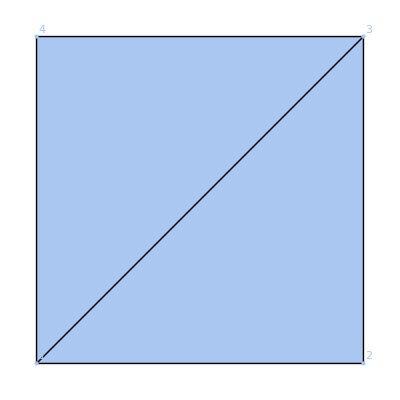

```mathematica
m=origami[{{0,0},{1,0},{1,1},{0,1}},{fold[{1,3}],face[{1,2,3}],face[{3,4,1}]},
 MeshCellLabel->{0->"Index"}
]
```

Origami is naturally embedded in 3D but displayed in 2D if possible.

```mathematica
embeddingDimension[m]
displayDimension[m]
```

3

2

Use display dimension to change the display dimension to 3D.

```mathematica
displayDimension[m->3]
```

-Graphics3D-

Getting a list of the components that make up the mechanical energy returns a list of the form.

```mathematica
mechanismComponents[m]
```

{rigidBar[{{1,3},{1,2},{2,3},{3,4},{4,1}},<|length→{√2,1,1,1,1},stiffness→{∞,∞,∞,∞,∞}|>],fold[{{1,3}},<|angle→{0},torsionalStiffness→{∞}|>]}

So in the above example, the rigid bar lengths are determined automatically and the bars have infinite stiffness.

To change the data, you can use the same properties.  The properties of a fold are given by

```mathematica
Options[fold]
```

{torsionalStiffness→∞,angle→Automatic}

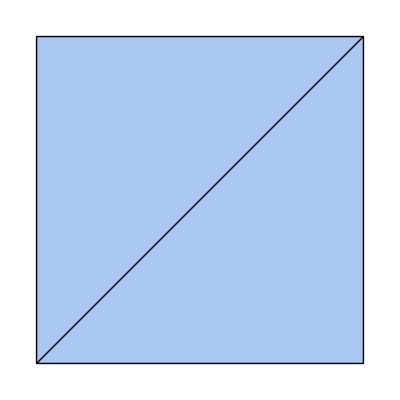

```mathematica
m=origami[{{0,0},{1,0},{1,1},{0,1}},{Property[fold[{1,3}],{"torsionalStiffness"->1}],face[{1,2,3}],face[{3,4,1}]}]
```

```mathematica
mechanismComponents[m]
```

{rigidBar[{{1,3},{1,2},{2,3},{3,4},{4,1}},<|length→{√2,1,1,1,1},stiffness→{∞,∞,∞,∞,∞}|>],fold[{{1,3}},<|angle→{0},torsionalStiffness→{1}|>]}

A fold generates both a fold[] component and a rigidBar[]. We can also manipulate the properties of the rigidBar[] and fold[] independently.

```mathematica
m=origami[{{0,0},{1,0},{1,1},{0,1}},{Property[fold[{1,3}],{"stiffness"->1}],face[{1,2,3}],face[{3,4,1}]}]
```

-Graphics-

```mathematica
mechanismComponents[m]
```

{rigidBar[{{1,3},{1,2},{2,3},{3,4},{4,1}},<|length→{√2,1,1,1,1},stiffness→{1,∞,∞,∞,∞}|>],fold[{{1,3}},<|angle→{0},torsionalStiffness→{∞}|>]}

In a future version, I may rename the component fold[] to torsionalSpring[].

#### framework[]

A four-bar linkage  with two fixed vertices at the ends.

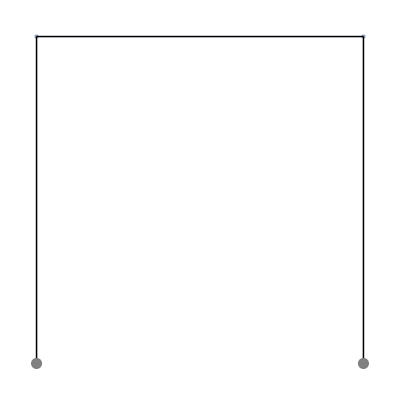

```mathematica
m = framework[{ {0,0},{0,1},{1,1},{1,0}}, { joint[1], joint[4],rigidBar[{1,2}], rigidBar[{2,3}],rigidBar[{3,4}] } ]
```

### basics of components

Mechanisms are built out of both display elements Point, Line, and Polygon, as well as the following components

```mathematica
$mechanismComponents
```

{rigidBar,spring,joint,fold,angleJoint}

In addition, you can use the following composite components that expand to combinations of other mechanism components.

```mathematica
$mechanismCompositeComponents
```

{block,flexibleBar,triangulatedFace,modEuclidean}

Each component has a set of Properties that can be set, in addition to a set of MeshRegion properties:

```mathematica
Options[rigidBar]
```

{stiffness→∞,length→Automatic}

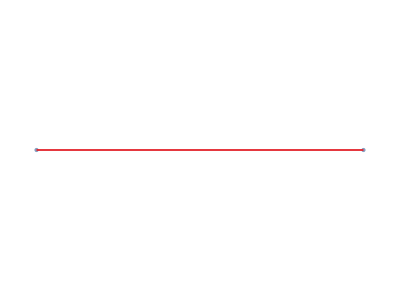

```mathematica
framework[{{0,0},{1,0}},{
Property[ rigidBar[{1,2}], {"stiffness" -> 1, MeshCellStyle -> Red} ]
}]
```

Properties can be assigned to groups of components and components can be specified as in nested lists anyway you want.

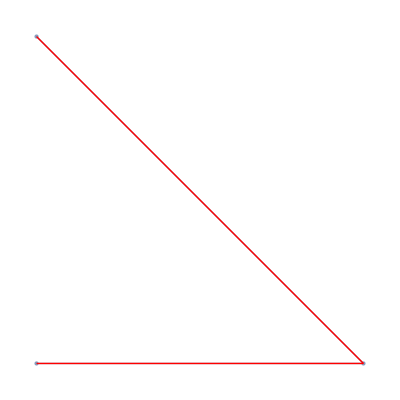

```mathematica
framework[{ {0,0},{1,0},{0,1} },{
Property[ {
rigidBar[{1,2}],
rigidBar[{2,3}]
}, {MeshCellStyle -> Red} ]
}]
```

### mechanismPositions[] and related functions for specifying vertex positions

```mathematica
m=origami[{{0,0},{1,0},{1,1},{0,1}},{fold[{1,3}],face[{1,2,3}],face[{3,4,1}]}];
```

Use mechanismPositions[] to get the coordinates.

```mathematica
mechanismPositions[m]
```

{{0,0,0},{1,0,0},{1,1,0},{0,1,0}}

The same function allows you to change the mechanism positions.

```mathematica
?randomDisplacements
```

```mathematica
mechanismPositions[m->(m["positions"]+randomDisplacements[m])]
```

-Graphics3D-

The function displaceVertices[] returns new positions with one or more vertices displaced.

```mathematica
?displaceVertices
```

```mathematica
displaceVertices[m,{2->{0,0,1/2},1->{1/2,0,0}}]
```

{{1/2,0,0},{1,0,1/2},{1,1,0},{0,1,0}}

```mathematica
mechanismPositions[m->displaceVertices[m,{2->{0,0,1/2}}]]
```

-Graphics3D-

There is another way to move a vertex in a mechanism. There is a color-coding bug in the syntax checker here but this will move a single vertex. Notice that we have to first set the display dimension to 3 if we use this method.

```mathematica
placeVertex[ displayDimension[m->3], 2->Offset[{0,0,1/2}]]
```

-Graphics3D-

To place the vertex at a specified position, remove Offset.

```mathematica
placeVertex[ displayDimension[m->3], 2->{0,0,1/2}]
```

-Graphics3D-

### mechanismComponents[] and how to change their properties

```mathematica
m=origami[{{0,0},{1,0},{1,1},{0,1}},{Property[fold[{1,3}],{"stiffness"->1}],face[{1,2,3}],face[{3,4,1}]}]
```

-Graphics-

```mathematica
mechanismComponents[m]
```

{rigidBar[{{1,3},{1,2},{2,3},{3,4},{4,1}},<|length→{√2,1,1,1,1},stiffness→{1,∞,∞,∞,∞}|>],fold[{{1,3}},<|angle→{0},torsionalStiffness→{∞}|>]}

To list only the rigidBar[] we use

```mathematica
mechanismComponents[m,rigidBar[_]]
```

{rigidBar[{{1,3},{1,2},{2,3},{3,4},{4,1}},<|length→{√2,1,1,1,1},stiffness→{1,∞,∞,∞,∞}|>]}

To list all rigidBars meeting vertex 3,

```mathematica
mechanismComponents[m,rigidBar[{3,_}]]
```

{rigidBar[{{1,3},{2,3},{3,4}},<|length→{√2,1,1},stiffness→{1,∞,∞}|>]}

Notice how the order does not matter. To list all components meeting vertex 3,

```mathematica
mechanismComponents[m,_[{3,_}]]
```

{rigidBar[{{1,3},{2,3},{3,4}},<|length→{√2,1,1},stiffness→{1,∞,∞}|>],fold[{{1,3}},<|angle→{0},torsionalStiffness→{∞}|>]}

If we want the torsional stiffness of the fold to become 1 again, we can use this idiom:

```mathematica
mechanismComponents[ mechanismComponents[m,fold[_]->{"torsionalStiffness"->1}] ]
```

{rigidBar[{{1,3},{1,2},{2,3},{3,4},{4,1}},<|length→{√2,1,1,1,1},stiffness→{1,∞,∞,∞,∞}|>],fold[{{1,3}},<|angle→{0},torsionalStiffness→{1}|>]}

The new property will be changed on every component matching the pattern for which it is valid. We can also use multiple patterns:

```mathematica
mechanismComponents[
mechanismComponents[m,rigidBar[{1,3}]|rigidBar[{2,3}] -> {"length"->Infinity}]
]
```

{rigidBar[{{1,3},{1,2},{2,3},{3,4},{4,1}},<|length→{∞,1,∞,1,1},stiffness→{1,∞,∞,∞,∞}|>],fold[{{1,3}},<|angle→{0},torsionalStiffness→{∞}|>]}

We can also use mechanismComponents to change details of display cells.

```mathematica
mechanismComponents[ m , Point[_]->{MeshCellLabel -> "Index"} ]
```

-Graphics-

### addCells[], deleteCells[], deleteVertices[]

#### addCells[]

addCells[] can be used to add or modify cells of a mechanism. First, we create a mechanism with two vertices.

```mathematica
m=framework[{{0,0},{1,0}},{}];
```

Next we add an additional vertex and two rigid bars spanning them.

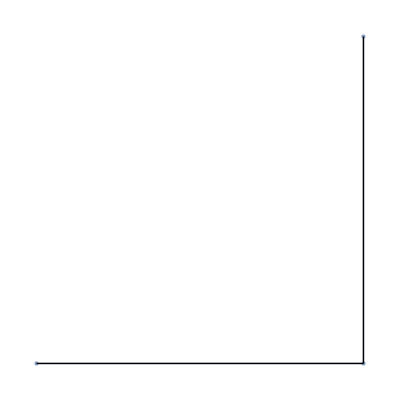

```mathematica
m2=addCells[ m, {rigidBar[{1,2}],rigidBar[{"a",2}], Point["a"->{1,1}]}]
```

We can also use addCells[] to replace cells with cells having different properties than originally.

```mathematica
mechanismComponents @ addCells[m2, {Property[ rigidBar[{1,2}], {"stiffness" -> 1}]}]
```

{rigidBar[{{1,2},{3,2}},<|length→{1,1},stiffness→{1,∞}|>]}

#### deleteCells[], deleteVertices[]

deleteCells[] deletes existing cells.

```mathematica
mechanismComponents[m2]
```

{rigidBar[{{1,2},{3,2}},<|length→{1,1},stiffness→{∞,∞}|>]}

```mathematica
mechanismComponents @ deleteCells[m2, rigidBar[{1,2}]]
```

{rigidBar[{{3,2}},<|length→{1},stiffness→{∞}|>]}

But notice that the display element is still present, even though it will not contribute to the energy.

```mathematica
deleteCells[m2, rigidBar[{1,2}]]
```

-Graphics-

We have to make sure to delete all of the components associated with vertices 1 and 2. Notice that vertex 1 is still there.

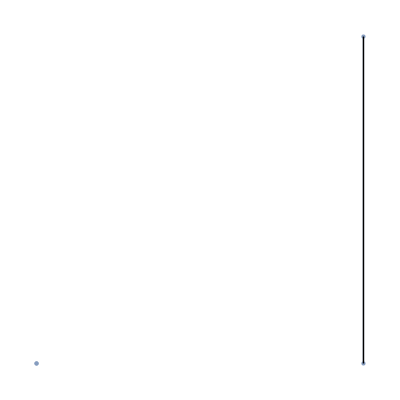

```mathematica
deleteCells[m2, _[{1,2}]]
```

To delete vertex 1 and everything connected to it, we can use deleteVertices[] instead.

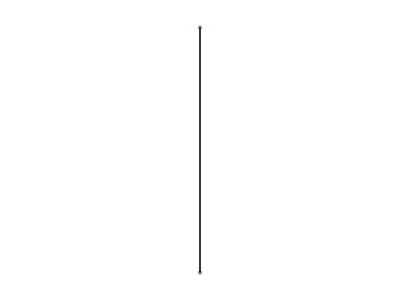

```mathematica
deleteVertices[m2,{1}]
```

#### applyMechanism[], subdivideEdge[]

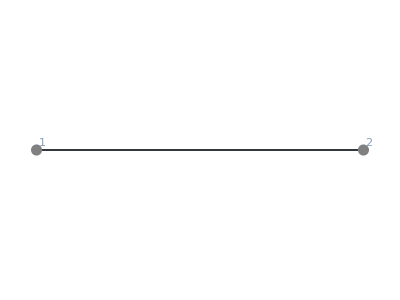

```mathematica
m=framework[{{0,0},{1,0}},{rigidBar[{1,2}],joint[1],joint[2]},MeshCellLabel->{0->"Index"}]
```

applyMechanism[] allows you to apply many alterations to a mechanism.

```mathematica
?applyMechanism
```

Subdivide an edge at the half-way point and call the new vertex “a”

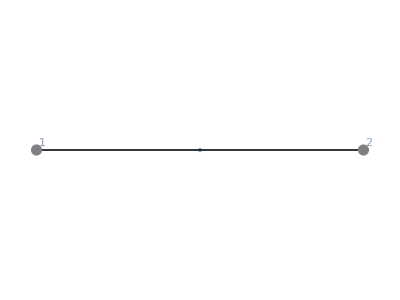

```mathematica
applyMechanism[ m, subdivideEdge[ "a"->{1,2}] ]
```

Apply multiple subdivisions.

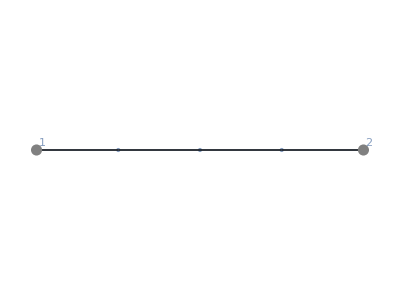

```mathematica
applyMechanism[ m, subdivideEdge[ "a"->{1,2}], subdivideEdge["b"->{"a",2}],subdivideEdge["c"->{1,"a"}] ]
```

Subdivide an edge into 3 pieces and add torsional springs.

```mathematica
m2=applyMechanism[ m, subdivideEdge[ "a"->{1,2}], subdivideEdge["b"->{"a",2}],subdivideEdge["c"->{1,"a"}], addCells[{ angleJoint[{1,"c","a"}], angleJoint[{"c","a","b"}],angleJoint[{"a","b",2}]  }]  ]
```

-Graphics-

```mathematica
mechanismComponents[m2]
```

{angleJoint[{{1,5,3},{5,3,4},{3,4,2}},<|angle→{0,0,0},angularStiffness→{∞,∞,∞}|>],rigidBar[{{1,5},{5,3},{3,4},{4,2}},<|length→{1/4,1/4,1/4,1/4},stiffness→{∞,∞,∞,∞}|>],joint[{1,2},<|position→{{0,0},{1,0}},stiffness→{{∞,∞},{∞,∞}}|>]}

### special examples

#### randomOrigami[]

```mathematica
?randomOrigami
```

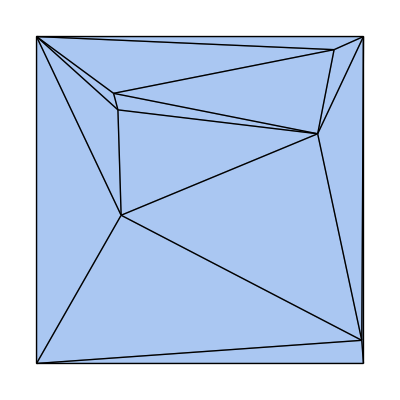

```mathematica
m=randomOrigami[6]
```

```mathematica
MeshCellCount[m,0]-4
```

6

“boundary”

You can specify the location of the points on the boundary.

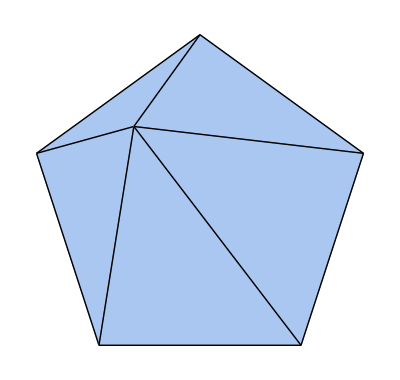

```mathematica
randomOrigami[1,"boundary"->CirclePoints[5]]
```

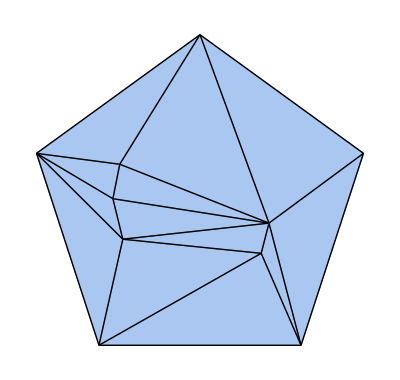

```mathematica
m=randomOrigami[5,"boundary"->CirclePoints[5]]
```

```mathematica
MeshCellCount[m,0]-5
```

5

#### singleVertex[]

```mathematica
?singleVertex
```

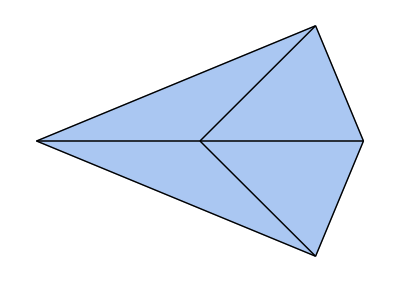

```mathematica
singleVertex[{Pi/4,3Pi/4,3Pi/4,Pi/4}]
```

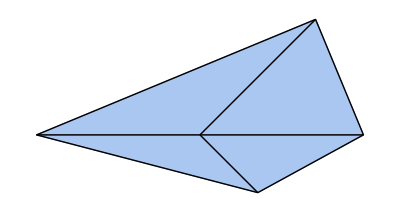

```mathematica
singleVertex[{Pi/4,3Pi/4,3Pi/4,Pi/4},{1,1,1/2,1}]
```

#### randomCellNetwork[]

```mathematica
?randomCellNetwork
```

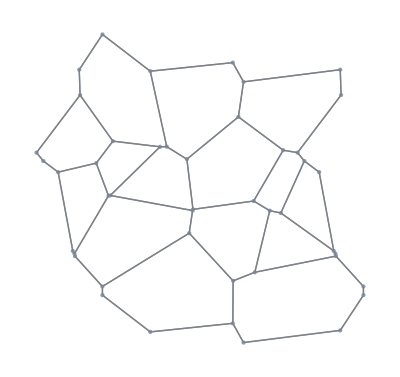

```mathematica
unitCell=randomCellNetwork[15]
```

```mathematica
?tesselateMechanism
```

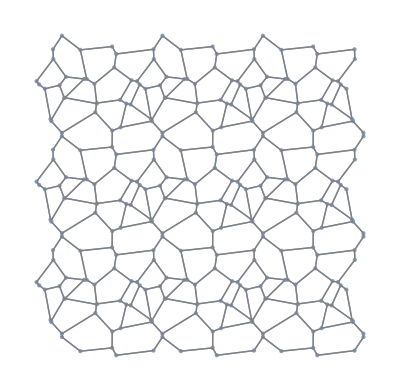

```mathematica
tesselateMechanism[unitCell, {{1,0},{0,1}},{3,3}]
```

The edges of this structure are actually springs of unit stiffness.

```mathematica
mechanismComponents[unitCell]
```

{spring[{{1,2},{2,3},{3,4},{4,1},{5,6},{6,7},{7,8},{8,9},{9,5},{10,11},{11,12},{12,13},{13,14},{14,10},{15,16},{16,11},{10,17},{17,15},{16,18},{18,19},{19,20},{20,12},{7,21},{21,15},{17,22},{22,8},{23,24},{24,25},{25,26},{26,27},{27,28},{28,23},{29,1},{4,30},{30,31},{31,32},{32,29},{3,33},{33,5},{9,30},{34,35},{35,36},{36,21},{6,34},{37,38},{38,34},{33,37},{14,39},{39,26},{25,22},{24,31},{40,41},{41,18},{36,40},{42,43},{43,32},{23,44},{44,45},{45,42}},<|length→{0.307373,0.0710278,0.218826,0.24969,0.213981,0.255526,0.193742,0.234563,0.22548,0.133524,0.149968,0.307373,0.0123534,0.257875,0.181868,0.105784,0.00683374,0.266792,0.217056,0.276729,0.0414173,0.0710278,0.0910206,0.0256804,0.320655,0.0048221,0.16287,0.248543,0.390448,0.0332306,0.231184,0.318004,0.0123534,0.0434628,0.24307,0.316911,0.00937844,0.0414173,0.0557731,0.0719171,0.0843943,0.318004,0.296206,0.135794,0.0973001,0.373538,0.276729,0.00937844,0.15703,0.0877124,0.0894323,0.161833,0.0973001,0.231184,0.0332306,0.15703,0.0843943,0.373538,0.161833},stiffness→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},strain→{#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&,#1-#2&}|>]}

## Geometry and periodic mechanisms

### displacementLength[]

```mathematica
?displacementLength
```

### randomDisplacements[]

```mathematica
?randomDisplacements
```

```mathematica
m=randomOrigami[1];
```

Apply random displacements

```mathematica
mechanismPositions[m -> randomDisplacements[m] ]
```

-Graphics3D-

Apply random displacements satisfying a list of rules.

```mathematica
randomDisplacements[m,"rules"->Thread[vertexDisplacement[1,All[3]]->vertexDisplacement[2,All[3]]]]
```

{{0.0187829,1.0696},{-2.98122,0.0696031},{3.24408,0.0864341},{-1.93075,-0.0254475},{-1.04031,0.858774},{-1.96823,1.05437},{-1.50778,0.318148},{2.07948,-0.0115164},{1.03425,0.82031},{1.93437,1.04875},{1.49389,0.593428}}

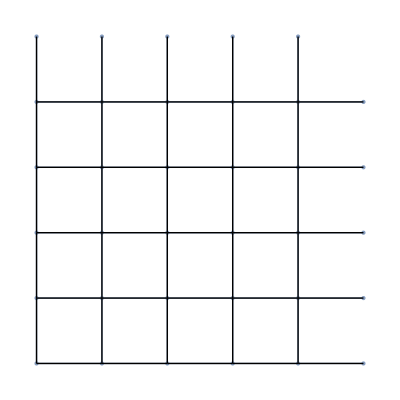

```mathematica
m=tesselateMechanism[ framework[{{0,0},{1,0},{0,1}},{rigidBar[{1,2}],rigidBar[{1,3}]}], {{1,0},{0,1}}, {5,5}]
```

This option can use the output of periodicIdentification[] to make periodic random displacements.

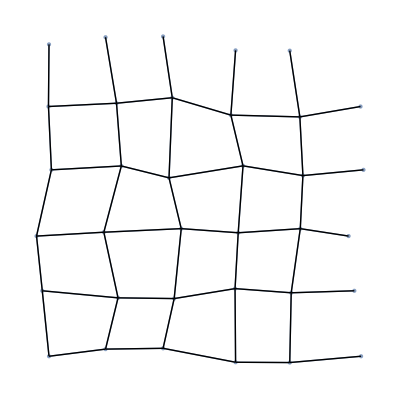

```mathematica
m2=mechanismPositions[m -> randomDisplacements[m,"rules"->periodicIdentification[m, {1,1},{{5,0},{0,5}}]]]
```

These random displacements can be tesselated.

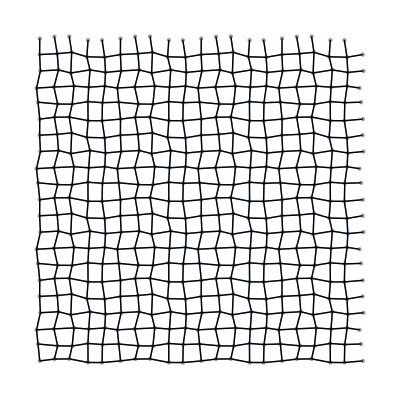

```mathematica
tesselateMechanism[m2, {{5,0},{0,5}},{4,4}]
```

### periodicIdentification[], minimalMechanism[]

```mathematica
?periodicIdentification
```

```mathematica
m=randomCellNetwork[10];
```

We can use periodicIdentification[] to return a set of rules showing us how the vertices of a periodic cell should be identified.

```mathematica
periodicIdentification[m, {1,1},{{1,0},{0,1}}]
```

{vertexDisplacement[7,x]→vertexDisplacement[26,x],vertexDisplacement[7,y]→vertexDisplacement[26,y],vertexDisplacement[8,x]→vertexDisplacement[25,x],vertexDisplacement[8,y]→vertexDisplacement[25,y],vertexDisplacement[9,x]→vertexDisplacement[30,x],vertexDisplacement[9,y]→vertexDisplacement[30,y],vertexDisplacement[11,x]→vertexDisplacement[17,x],vertexDisplacement[11,y]→vertexDisplacement[17,y],vertexDisplacement[12,x]→vertexDisplacement[18,x],vertexDisplacement[12,y]→vertexDisplacement[18,y],vertexDisplacement[14,x]→vertexDisplacement[31,x],vertexDisplacement[14,y]→vertexDisplacement[31,y],vertexDisplacement[15,x]→vertexDisplacement[27,x],vertexDisplacement[15,y]→vertexDisplacement[27,y],vertexDisplacement[16,x]→vertexDisplacement[26,x],vertexDisplacement[16,y]→vertexDisplacement[26,y],vertexDisplacement[21,x]→vertexDisplacement[23,x],vertexDisplacement[21,y]→vertexDisplacement[23,y],vertexDisplacement[22,x]→vertexDisplacement[32,x],vertexDisplacement[22,y]→vertexDisplacement[32,y],vertexDisplacement[28,x]→vertexDisplacement[25,x],vertexDisplacement[28,y]→vertexDisplacement[25,y],vertexDisplacement[29,x]→vertexDisplacement[24,x],vertexDisplacement[29,y]→vertexDisplacement[24,y]}

```mathematica
?minimalMechanism
```

The smallest version of the periodic network can be found using minimalMechanism[].

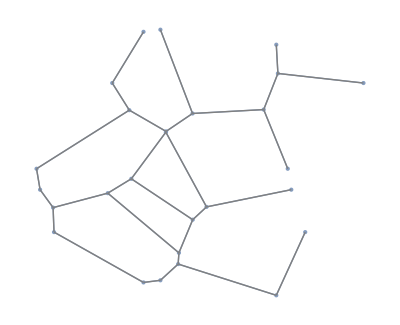

```mathematica
mSmallest = minimalMechanism[m,{{1,0},{0,1}}]
```

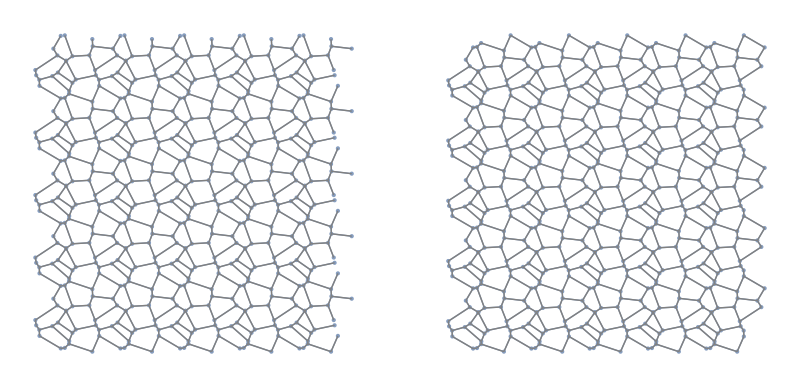

```mathematica
GraphicsRow[
{
tesselateMechanism[ mSmallest, {{1,0},{0,1}},{5,5}],
tesselateMechanism[ m, {{1,0},{0,1}},{5,5}]
}
]
```

```mathematica
pi=periodicIdentification[mSmallest,{1,1},{{1,0},{0,1}}]
```

{vertexDisplacement[7,x]→vertexDisplacement[25,x],vertexDisplacement[7,y]→vertexDisplacement[25,y],vertexDisplacement[9,x]→vertexDisplacement[14,x],vertexDisplacement[9,y]→vertexDisplacement[14,y],vertexDisplacement[11,x]→vertexDisplacement[26,x],vertexDisplacement[11,y]→vertexDisplacement[26,y],vertexDisplacement[12,x]→vertexDisplacement[23,x],vertexDisplacement[12,y]→vertexDisplacement[23,y],vertexDisplacement[13,x]→vertexDisplacement[22,x],vertexDisplacement[13,y]→vertexDisplacement[22,y],vertexDisplacement[18,x]→vertexDisplacement[27,x],vertexDisplacement[18,y]→vertexDisplacement[27,y],vertexDisplacement[24,x]→vertexDisplacement[21,x],vertexDisplacement[24,y]→vertexDisplacement[21,y]}

## Rigidity of mechanisms

These are the main functions for analyzing the rigidity of mechanisms.

### constraintEquations[], constraintMatrix[], compatibilityMatrix[]

These functions are used to read off the constraints associated with a mechanism. Constraints have infinite stiffness.

#### constraintEquations[]

```mathematica
?constraintEquations
```

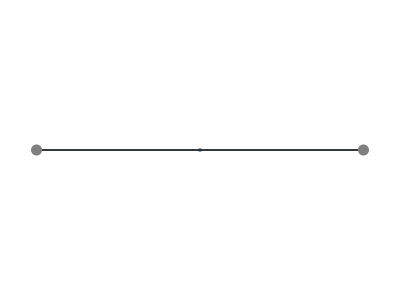

```mathematica
m=framework[
{{0,0},{1,0},{2,0}},
{rigidBar[{1,2}],rigidBar[{2,3}], joint[1], Property[joint[3],"stiffness"->{0,Infinity}]}
]
```

Return the constraints to first order, second order, and infinite order.

```mathematica
constraintEquations[m,1]
```

{2 (-vertexDisplacement[1,x]+vertexDisplacement[2,x]),2 (-vertexDisplacement[2,x]+vertexDisplacement[3,x]),vertexDisplacement[1,x],vertexDisplacement[1,y],vertexDisplacement[3,y]}

```mathematica
constraintEquations[m,2]
```

{-1+(1-vertexDisplacement[1,x]+vertexDisplacement[2,x])^2+(-vertexDisplacement[1,y]+vertexDisplacement[2,y])^2,-1+(1-vertexDisplacement[2,x]+vertexDisplacement[3,x])^2+(-vertexDisplacement[2,y]+vertexDisplacement[3,y])^2,vertexDisplacement[1,x],vertexDisplacement[1,y],vertexDisplacement[3,y]}

```mathematica
constraintEquations[m,Infinity]
```

{-1+(1-vertexDisplacement[1,x]+vertexDisplacement[2,x])^2+(-vertexDisplacement[1,y]+vertexDisplacement[2,y])^2,-1+(1-vertexDisplacement[2,x]+vertexDisplacement[3,x])^2+(-vertexDisplacement[2,y]+vertexDisplacement[3,y])^2,vertexDisplacement[1,x],vertexDisplacement[1,y],vertexDisplacement[3,y]}

Options

Option “output” can be used to specify if the output should be in terms of vertexPosition or vertexDisplacement.

```mathematica
constraintEquations[m,Infinity,"output"->vertexPosition]
```

{-1+(1-vertexDisplacement[1,x]+vertexDisplacement[2,x])^2+(-vertexDisplacement[1,y]+vertexDisplacement[2,y])^2,-1+(1-vertexDisplacement[2,x]+vertexDisplacement[3,x])^2+(-vertexDisplacement[2,y]+vertexDisplacement[3,y])^2,vertexDisplacement[1,x],vertexDisplacement[1,y],vertexDisplacement[3,y]}

```mathematica
constraintEquations[m,1,"output"->vertexPosition]
```

{2 (-vertexDisplacement[1,x]+vertexDisplacement[2,x]),2 (-vertexDisplacement[2,x]+vertexDisplacement[3,x]),vertexDisplacement[1,x],vertexDisplacement[1,y],vertexDisplacement[3,y]}

#### constraintMatrix[]

```mathematica
?constraintMatrix
```

```mathematica
m=framework[
{{0,0},{1,0},{2,0}},
{rigidBar[{1,2}],rigidBar[{2,3}], joint[1], Property[joint[3],"stiffness"->{0,Infinity}]}
]
```

-Graphics-

Returns the matrix specifying the first-order constraints as a SparseArray.

```mathematica
constraintMatrix[m]//MatrixForm
```

(-2 | 0 | 2 | 0 | 0 | 0
0 | 0 | -2 | 0 | 2 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Simplify[
constraintMatrix[m] . Flatten[vertexDisplacement[m]] - constraintEquations[m,1]
]
```

{0,0,0,0,0}

Additional constraints can be specified using “constraints” option. We can fix the displacement of the second constraint, for example, as follows.

```mathematica
constraintMatrix[m,"constraints"->(vertexDisplacement[2,"y"]==0)]//MatrixForm
```

(-2 | 0 | 2 | 0 | 0 | 0
0 | 0 | -2 | 0 | 2 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0)

For periodic mechanisms, we have

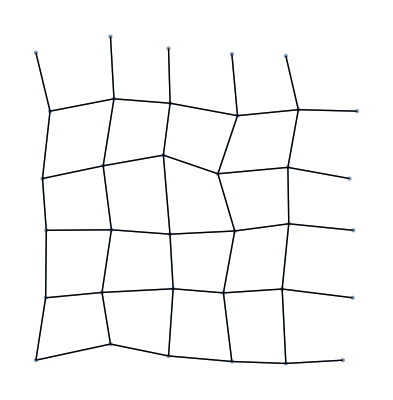

```mathematica
rules=periodicIdentification[ m=randomSquareLattice[{1,1},{5,5}], {1,1},{{5,0},{0,5}}];
m
```

```mathematica
NullSpace[constraintMatrix[m,"rules"->rules]]
```

{{-0.147525,0.135043,-0.147525,0.135043,-0.147525,0.135043,-0.147525,0.135043,-0.147525,0.135043,-0.147525,0.135043,-0.147525,0.135043,-0.147525,0.135043,-0.147525,0.135043,-0.147525,0.135043,-0.147525,0.135043,-0.147525,0.135043,-0.147525,0.135043,-0.147525,0.135043,-0.147525,0.135043,-0.147525,0.135043,-0.147525,0.135043,-0.147525,0.135043,-0.147525,0.135043,-0.147525,0.135043,-0.147525,0.135043,-0.147525,0.135043,-0.147525,0.135043,-0.147525,0.135043,-0.147525,0.135043},{-0.135043,-0.147525,-0.135043,-0.147525,-0.135043,-0.147525,-0.135043,-0.147525,-0.135043,-0.147525,-0.135043,-0.147525,-0.135043,-0.147525,-0.135043,-0.147525,-0.135043,-0.147525,-0.135043,-0.147525,-0.135043,-0.147525,-0.135043,-0.147525,-0.135043,-0.147525,-0.135043,-0.147525,-0.135043,-0.147525,-0.135043,-0.147525,-0.135043,-0.147525,-0.135043,-0.147525,-0.135043,-0.147525,-0.135043,-0.147525,-0.135043,-0.147525,-0.135043,-0.147525,-0.135043,-0.147525,-0.135043,-0.147525,-0.135043,-0.147525}}

```mathematica
NullSpace[Transpose @ constraintMatrix[m,"rules"->rules]]
```

{{0.0370206,-0.0276345,0.245139,-0.0708632,0.0046069,-0.0937771,-0.163443,-0.0132201,0.0251987,-0.021416,0.0210686,-0.283765,0.258106,-0.228071,-0.0633122,-0.227485,-0.0919086,-0.233953,-0.0316865,-0.248857,0.0324351,-0.127802,0.346412,-0.113753,-0.0590939,-0.0726804,-0.0733456,-0.155804,-0.0455319,-0.155444,0.0442701,0.16251,0.245819,0.141578,0.0053887,0.149226,-0.145324,0.186458,0.0265998,0.182174,0.0383417,0.0112159,0.19906,0.0542049,0.0109129,0.0646353,-0.168371,0.0145131,0.0342776,0.0194909},{0.122149,-0.0874336,-0.22839,-0.0405462,0.185183,-0.0788623,0.108108,-0.0959615,-0.185775,-0.0667579,0.141909,-0.192616,-0.135558,-0.170284,0.156862,-0.154418,0.157388,-0.15201,-0.254359,-0.218405,0.128945,0.00775149,-0.192059,-0.0140975,0.1401,-0.0240817,0.16962,0.0564825,-0.205534,0.0272897,0.153548,0.0796531,-0.197622,0.113459,0.223743,0.102421,0.0974612,0.0357309,-0.207313,0.0952334,0.128115,0.0596166,-0.170811,0.0333083,0.191682,0.0892702,0.0897916,0.115447,-0.173746,0.0959957}}

#### compatiblityMatrix[]

```mathematica
?compatibilityMatrix
```

```mathematica
m=framework[
{{0,0},{1,0},{2,0}},
{rigidBar[{1,2}],rigidBar[{2,3}], joint[1], Property[joint[3],"stiffness"->{0,Infinity}]}
]
```

-Graphics-

```mathematica
compatibilityMatrix[m]//MatrixForm
```

(-2 | 0 | 2 | 0 | 0 | 0
0 | 0 | -2 | 0 | 2 | 0)

### infinitesimalMotions[]

```mathematica
?infinitesimalMotions
```

```mathematica
m=framework[
{{0,0},{1,0},{2,0}},
{rigidBar[{1,2}],rigidBar[{2,3}], joint[1], Property[joint[3],"component"->"y"]}
]
```

-Graphics-

The linear motions are listed in the first element and any additional quadratic constraints are specified in the second argument.

```mathematica
{linearMotions, quadraticConstraints}=infinitesimalMotions[m, "variables"->v]
```

{{{0,0},{0,v[1]},{0,0}},{-√(2/5) v[1]^2}}

Since the only solution in which the quadratic constraints vanish is 0, the system is actually rigid.

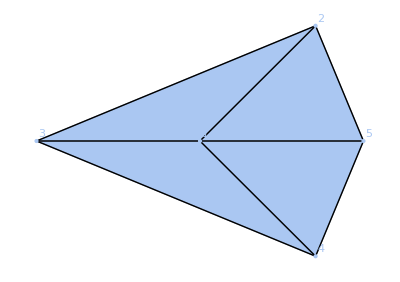

```mathematica
m=addCells[
singleVertex[{Pi/4,3Pi/4,3Pi/4,Pi/4},MeshCellLabel->{0->"Index"}],
{
(*eliminate Euclidean motions by pinning certain joints*)
joint[1],
Property[joint[3],{"stiffness"->{0,Infinity,Infinity}}],
Property[joint[4],{"stiffness"->{0,0,Infinity}}]
}
]
```

The origami structure has a branch point at the flat state characterized by two branches of configurations as found by solving the quadratic constraints.

```mathematica
Simplify@infinitesimalMotions[m, "variables"->v]
```

{{{0,0,0},{0,0,v[2]},{0,0,0},{0,0,0},{0,0,v[1]}},{(v[1] (v[1]-√2 v[2]))/(2 √3)}}

If we add a rigid fold as well, the system becomes rigid again.

```mathematica
Simplify@infinitesimalMotions[ addCells[m,fold[{1,5}]], "variables"->v]
```

{{{0,0,0},{0,0,√(2/3) v[1]},{0,0,0},{0,0,0},{0,0,v[1]/(√3)}},{-v[1]^2/(6 √3)}}

### isometricTrajectory[]

```mathematica
?isometricTrajectory
```

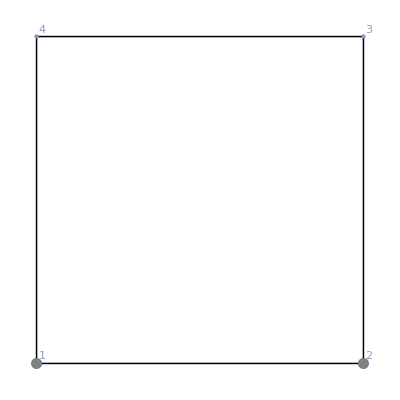

```mathematica
fourBarLinkage=framework[{{0,0},{1,0},{1,1},{0,1}},
{
rigidBar/@Partition[{1,2,3,4},2,1,1],
joint[1],Property[joint[2],"stiffness"->{0,Infinity}]
},
MeshCellLabel->{0->"Index"}
]
```

```mathematica
{linear, quadratic}=infinitesimalMotions[fourBarLinkage,"variables"->v]
```

{{{0,0},{0,0},{v[1]/(√2),0},{v[1]/(√2),0}},{}}

```mathematica
trajectory=isometricTrajectory[fourBarLinkage, D[linear,v[1]], 100];
```

```mathematica
ListAnimate[plotMechanism[fourBarLinkage,trajectory]]
```

#### “initial”

Use option “initial” to change the initial configuration.

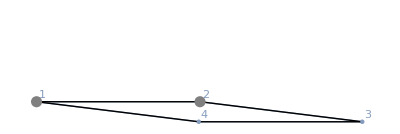
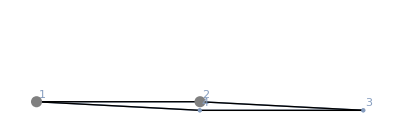
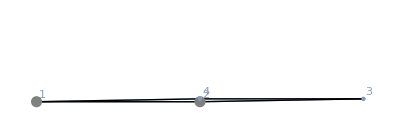
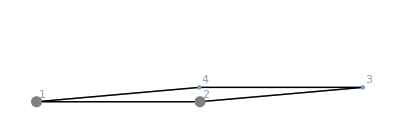
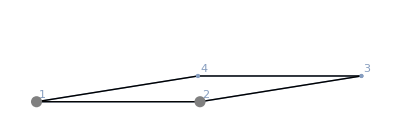
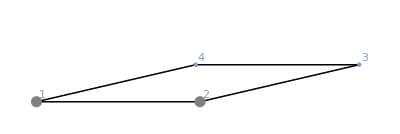
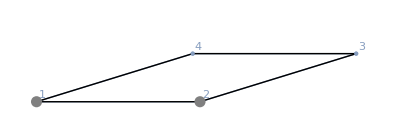
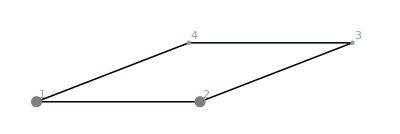

```mathematica
plotMechanism[fourBarLinkage,isometricTrajectory[fourBarLinkage, D[linear,v[1]], 10, "initial"->trajectory[[25]]]]
```

#### “constraints”

Use option “constraints” to set additional constraints.

#### Method

Use option Method to pass additional options to the solvers.

“stepsize”

Changes the stepsize of the solver. The default “stepsize”->0.1

“stepMethod”

Use this option to change the method used to choose the next step. The default, “Minimization”, takes a step as close to the previous one as possible, then performs an energy minimization to correct any errors. None takes a step but does not minimize energy. “RandomWalk” takes a step in a random direction.

```mathematica
ListAnimate[plotMechanism[fourBarLinkage,isometricTrajectory[fourBarLinkage, D[linear,v[1]], 100, Method->{"stepMethod"->"RandomWalk"}]]]
```

### mechanismEnergy[]

```mathematica
?mechanismEnergy
```

Returns an energy functional for a mechanism. Pinned vertices are not fixed in the energy typically but other constraints are typically treated with quadratic functions of various stiffnesses.

```mathematica
mechanismEnergy[singleVertex[{Pi/2, Pi/2, Pi/2, Pi/2}]]
```

1/8 (-1+(-vertexPosition[1,x]+vertexPosition[2,x])^2+(-vertexPosition[1,y]+vertexPosition[2,y])^2+(-vertexPosition[1,z]+vertexPosition[2,z])^2)^2+1/8 (-1+(-vertexPosition[1,x]+vertexPosition[3,x])^2+(-vertexPosition[1,y]+vertexPosition[3,y])^2+(-vertexPosition[1,z]+vertexPosition[3,z])^2)^2+1/8 (-1+1/2 ((-vertexPosition[2,x]+vertexPosition[3,x])^2+(-vertexPosition[2,y]+vertexPosition[3,y])^2+(-vertexPosition[2,z]+vertexPosition[3,z])^2))^2+1/8 (-1+(-vertexPosition[1,x]+vertexPosition[4,x])^2+(-vertexPosition[1,y]+vertexPosition[4,y])^2+(-vertexPosition[1,z]+vertexPosition[4,z])^2)^2+1/8 (-1+1/2 ((-vertexPosition[3,x]+vertexPosition[4,x])^2+(-vertexPosition[3,y]+vertexPosition[4,y])^2+(-vertexPosition[3,z]+vertexPosition[4,z])^2))^2+1/8 (-1+1/2 ((vertexPosition[2,x]-vertexPosition[5,x])^2+(vertexPosition[2,y]-vertexPosition[5,y])^2+(vertexPosition[2,z]-vertexPosition[5,z])^2))^2+1/8 (-1+(-vertexPosition[1,x]+vertexPosition[5,x])^2+(-vertexPosition[1,y]+vertexPosition[5,y])^2+(-vertexPosition[1,z]+vertexPosition[5,z])^2)^2+1/8 (-1+1/2 ((-vertexPosition[4,x]+vertexPosition[5,x])^2+(-vertexPosition[4,y]+vertexPosition[5,y])^2+(-vertexPosition[4,z]+vertexPosition[5,z])^2))^2

Default stiffnesses can be extracted and reset using $defaultStiffness[]

```mathematica
$defaultStiffness[rigidBar]
```

1

```mathematica
$defaultStiffness[fold]
```

1/10000

The option “constraints” can be used to specify additional constraints with their own default stiffness.

```mathematica
$defaultStiffness["constraints"]
```

1/10

### minimizeEnergy[]

```mathematica
?minimizeEnergy
```

```mathematica
m=addCells[
singleVertex[{Pi/4,3Pi/4,3Pi/4,Pi/4},MeshCellLabel->{0->"Index"}],

{
Property[fold[{1,5}],"angle"->Pi/2],

(*eliminate Euclidean motions by pinning certain joints*)
joint[1],
Property[joint[3],"stiffness"->{0,Infinity,Infinity}],
Property[joint[4],"stiffness"->{0,0,Infinity}]
}
]
```

-Graphics-

```mathematica
minimizeEnergy[m]
```

{1.82999×10^-21,{{0,0,0},{0.707107,2.127×10^-12,0.707107},{-1.,0,0},{0.707107,-0.707107,0},{1.,-1.59549×10^-16,1.10129×10^-13}}}

minimizeEnergy[] takes the same options as FindMinimum, as well as “initial” for setting the initial configuration, and “constraints” to add additional constraints to the mechanism.

```mathematica
Options[minimizeEnergy]
```

{initial→Automatic,constraints→None,AccuracyGoal→Automatic,Compiled→Automatic,EvaluationMonitor→None,Gradient→Automatic,MaxIterations→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PrecisionGoal→Automatic,StepMonitor→None,WorkingPrecision→MachinePrecision}

### findMinimalTrajectory[]

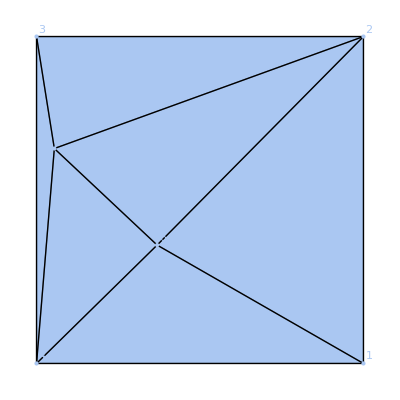

```mathematica
m=randomOrigami[2,MeshCellLabel->{0->"Index"}]
```

```mathematica
m2=addCells[m,{Property[fold[{5,6}],"angle"->Pi/2]}]
```

-Graphics-

```mathematica
end=minimizeEnergy[m2,MaxIterations->1000][[2]]
```

{{0.735746,-0.562944,-0.305516},{0.547955,0.594546,0.485023},{-0.663709,0.648544,-0.24234},{-0.53491,-0.646881,0.309616},{-0.68833,0.184258,-0.0858466},{-0.212293,-0.189825,-0.160937}}

```mathematica
ListAnimate[plotMechanism[m2, findMinimalTrajectory[m2, m2["positions"], end, 10]]]
```

## dynamical systems

```mathematica
?dynamicalSystem
```

```mathematica
?dynamicalSystemEquations
```

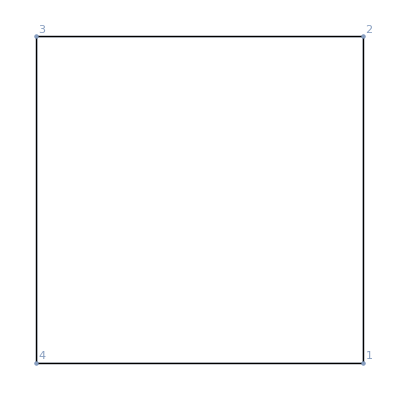

```mathematica
m=polygonalLinkage[CirclePoints[4],MeshCellLabel->{0->"Index"}]
```

```mathematica
eq=dynamicalSystem[m,{m["positions"],{{0,0},{1,0},{0,0},{-1,0}}},{t,0,1},"drag"->0.1]
```

{{InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{InterpolatingFunction[…][t],InterpolatingFunction[…][t]},{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}}

```mathematica
eq/.t->0.4
```

{{0.70086,-0.706744},{1.09284,0.706744},{-0.70086,0.706744},{-1.09284,-0.706744}}

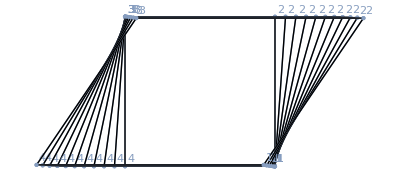

```mathematica
Show[plotMechanism[m,eq/.t->#&/@Range[0,1,0.1]]]
```

```mathematica
dynamicalSystemEquations[m,{v,t},"drag"->0.1]
```

{0.+√2 (v[1,x][t]-v[2,x][t]) (-1+1/2 ((-v[1,x][t]+v[2,x][t])^2+(-v[1,y][t]+v[2,y][t])^2))+√2 (v[1,x][t]-v[4,x][t]) (-1+1/2 ((v[1,x][t]-v[4,x][t])^2+(v[1,y][t]-v[4,y][t])^2))+0.1 v[1,x]'[t]+v[1,x]''[t],0.+√2 (v[1,y][t]-v[2,y][t]) (-1+1/2 ((-v[1,x][t]+v[2,x][t])^2+(-v[1,y][t]+v[2,y][t])^2))+√2 (-1+1/2 ((v[1,x][t]-v[4,x][t])^2+(v[1,y][t]-v[4,y][t])^2)) (v[1,y][t]-v[4,y][t])+0.1 v[1,y]'[t]+v[1,y]''[t],0.+√2 (-v[1,x][t]+v[2,x][t]) (-1+1/2 ((-v[1,x][t]+v[2,x][t])^2+(-v[1,y][t]+v[2,y][t])^2))+√2 (v[2,x][t]-v[3,x][t]) (-1+1/2 ((-v[2,x][t]+v[3,x][t])^2+(-v[2,y][t]+v[3,y][t])^2))+0.1 v[2,x]'[t]+v[2,x]''[t],0.+√2 (-v[1,y][t]+v[2,y][t]) (-1+1/2 ((-v[1,x][t]+v[2,x][t])^2+(-v[1,y][t]+v[2,y][t])^2))+√2 (v[2,y][t]-v[3,y][t]) (-1+1/2 ((-v[2,x][t]+v[3,x][t])^2+(-v[2,y][t]+v[3,y][t])^2))+0.1 v[2,y]'[t]+v[2,y]''[t],0.+√2 (-v[2,x][t]+v[3,x][t]) (-1+1/2 ((-v[2,x][t]+v[3,x][t])^2+(-v[2,y][t]+v[3,y][t])^2))+√2 (v[3,x][t]-v[4,x][t]) (-1+1/2 ((-v[3,x][t]+v[4,x][t])^2+(-v[3,y][t]+v[4,y][t])^2))+0.1 v[3,x]'[t]+v[3,x]''[t],0.+√2 (-v[2,y][t]+v[3,y][t]) (-1+1/2 ((-v[2,x][t]+v[3,x][t])^2+(-v[2,y][t]+v[3,y][t])^2))+√2 (v[3,y][t]-v[4,y][t]) (-1+1/2 ((-v[3,x][t]+v[4,x][t])^2+(-v[3,y][t]+v[4,y][t])^2))+0.1 v[3,y]'[t]+v[3,y]''[t],0.+√2 (-v[1,x][t]+v[4,x][t]) (-1+1/2 ((v[1,x][t]-v[4,x][t])^2+(v[1,y][t]-v[4,y][t])^2))+√2 (-v[3,x][t]+v[4,x][t]) (-1+1/2 ((-v[3,x][t]+v[4,x][t])^2+(-v[3,y][t]+v[4,y][t])^2))+0.1 v[4,x]'[t]+v[4,x]''[t],0.+√2 (-1+1/2 ((v[1,x][t]-v[4,x][t])^2+(v[1,y][t]-v[4,y][t])^2)) (-v[1,y][t]+v[4,y][t])+√2 (-v[3,y][t]+v[4,y][t]) (-1+1/2 ((-v[3,x][t]+v[4,x][t])^2+(-v[3,y][t]+v[4,y][t])^2))+0.1 v[4,y]'[t]+v[4,y]''[t]}

A pendulum

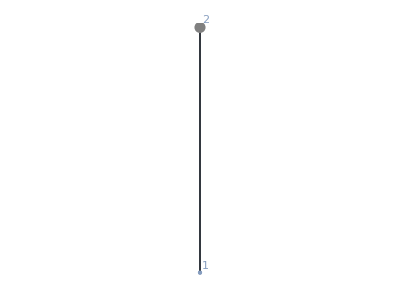

```mathematica
m=framework[{{0,0},{0,1}},{joint[2],rigidBar[{1,2}]}];
modifyMechanism[m,MeshCellLabel->{0->"Index"}]
```

```mathematica
dynamicalSystemEquations[m, {v,t},"drag"->1,"mass"->0]
```

{2 v[1,x][t] (-1+(v[1,x][t])^2+(1-v[1,y][t])^2)+v[1,x]'[t],-2 (-1+(v[1,x][t])^2+(1-v[1,y][t])^2) (1-v[1,y][t])+v[1,y]'[t]}

Even though vertex 2 is pinned, we still have to provide initial conditions for it. These are ignored by the code.

```mathematica
out=dynamicalSystem[m,{m["positions"],{{10^(-3),0},{0,0}}},{t,0,10^4}]
```

{{InterpolatingFunction[{{0., 10000.}}, <>][t],InterpolatingFunction[{{0., 10000.}}, <>][t]},{0,1}}

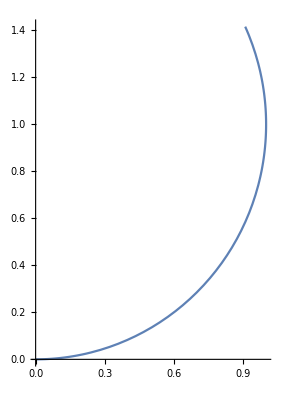

```mathematica
Show[
ParametricPlot[out[[1]]/.t->tt,{tt,0,2 10^3}],
ParametricPlot[out[[2]]/.t->tt,{tt,0,2 10^3}]
]
```

A pendulum with a small amount of gravity

```mathematica
out=dynamicalSystem[m,{m["positions"],{{10^(-2),0},{0,0}}},{t,0,10^4},"additional"->10^(-4)vertexPosition[1,"y"]]
```

{{InterpolatingFunction[{{0., 10000.}}, <>][t],InterpolatingFunction[{{0., 10000.}}, <>][t]},{0,1}}

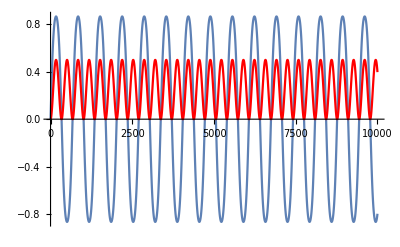

```mathematica
Show[
Plot[out[[1,1]]/.t->tt,{tt,0,10^4}],
Plot[out[[1,2]]/.t->tt,{tt,0,10^4},PlotStyle->Red]
]
```

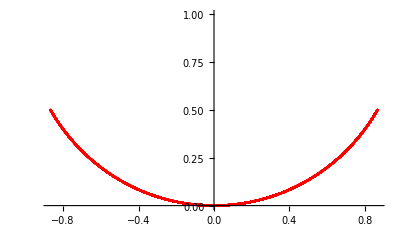

```mathematica
Show[
ParametricPlot[out[[1]]/.t->tt,{tt,0,10^4},PlotStyle->Red],
ParametricPlot[out[[2]]/.t->tt,{tt,0,10^4}],

PlotRange->All
]
```

If we give the joint an actual stiffness then we get something slightly different.

```mathematica
m=framework[{{0,0},{0,1}},{Property[joint[2],"stiffness"->{10,10}],rigidBar[{1,2}]}];
modifyMechanism[m,MeshCellLabel->{0->"Index"}]
```

-Graphics-

Though the solution is essentially the same, vertex 2  is treated as being pinned by a spring and we now get a numerical solution to the position of vertex 2.

```mathematica
out=dynamicalSystem[m,{m["positions"],{{10^(-3),0},{0,0}}},{t,0,10^4}]
```

{{InterpolatingFunction[{{0., 10000.}}, <>][t],InterpolatingFunction[{{0., 10000.}}, <>][t]},{InterpolatingFunction[{{0., 10000.}}, <>][t],InterpolatingFunction[{{0., 10000.}}, <>][t]}}

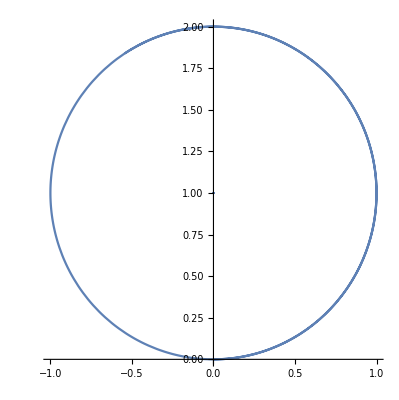

```mathematica
Show[
ParametricPlot[out[[1]]/.t->tt,{tt,0,10^4}],
ParametricPlot[out[[2]]/.t->tt,{tt,0,10^4}]
]
```

A pendulum with a small amount of gravity

```mathematica
out=dynamicalSystem[m,{m["positions"],{{10^(-2),0},{0,0}}},{t,0,10^4},"additional"->10^(-4)vertexPosition[1,"y"]]
```

{{InterpolatingFunction[{{0., 10000.}}, <>][t],InterpolatingFunction[{{0., 10000.}}, <>][t]},{InterpolatingFunction[{{0., 10000.}}, <>][t],InterpolatingFunction[{{0., 10000.}}, <>][t]}}

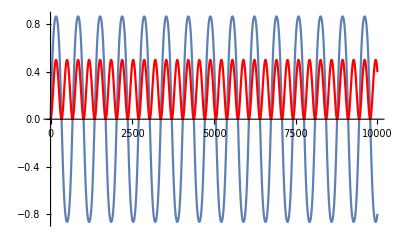

```mathematica
Show[
Plot[out[[1,1]]/.t->tt,{tt,0,10^4}],
Plot[out[[1,2]]/.t->tt,{tt,0,10^4},PlotStyle->Red]
]
```

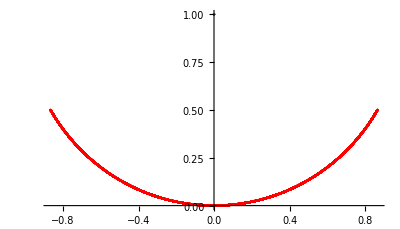

```mathematica
Show[
ParametricPlot[out[[1]]/.t->tt,{tt,0,10^4},PlotStyle->Red],
ParametricPlot[out[[2]]/.t->tt,{tt,0,10^4}],

PlotRange->All
]
```

## Examples

### Watt mechanism

The Watt mechanism is one in which a center point moves almost vertically.

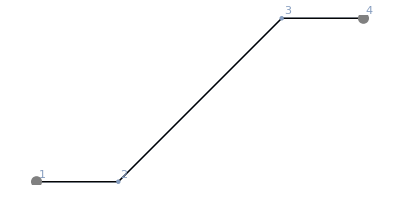

```mathematica
m=framework[{
 {-1,0},{-1/2,0},{1/2,1},{1,1}
},
{
joint[1],
joint[4],
rigidBar[{1,2}],rigidBar[{2,3}],rigidBar[{3,4}]
},
MeshCellLabel->{0->"Index"}
]
```

```mathematica
infinitesimalMotions[m,"variables"->v]
```

{{{0,0},{0,v[1]/(√2)},{0,v[1]/(√2)},{0,0}},{}}

```mathematica
?isometricTrajectory
```

```mathematica
listEdges[m,{1}]
```

{{{1,2}}}

```mathematica
compatibilityMatrix[m]//MatrixForm
```

(-1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | -2 | -2 | 2 | 2 | 0 | 0
0 | 0 | 0 | 0 | -1 | 0 | 1 | 0)

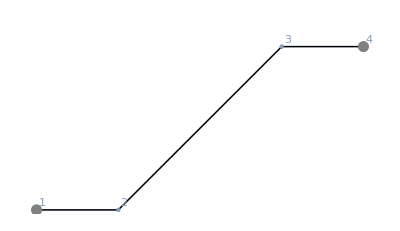
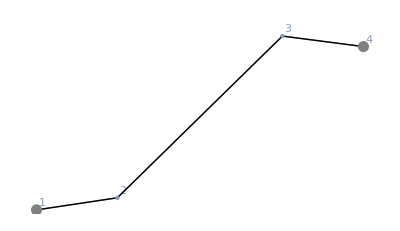
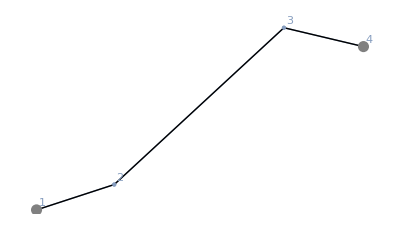
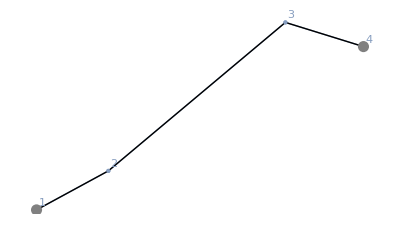
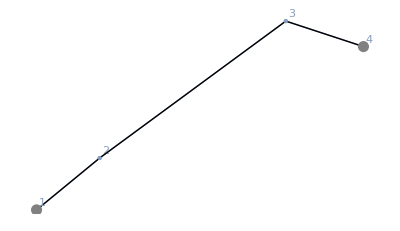
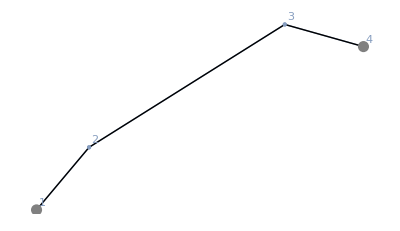
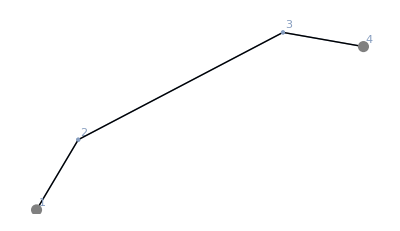
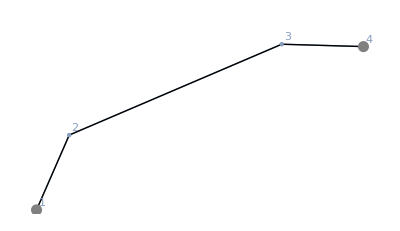

```mathematica
plotMechanism[m,isometricTrajectory[m, {{0,0},{0,1},{0,0},{0,0}}, 10]]
```

```mathematica
Dimensions[isometricTrajectory[m,
D[infinitesimalMotions[m,"variables"->v][[1]],v[1]],
50
]]
```

{51,4,2}

```mathematica
ListAnimate[plotMechanism[m,
isometricTrajectory[m,
D[infinitesimalMotions[m,"variables"->v][[1]],v[1]],
50
]
]]
```

### 3rd order rigid framework that is nevertheless a mechanism

This example comes from Connelly, R. and Servatius, H., 1994. Higher-order rigidity—What is the proper definition?. Discrete & Computational Geometry, 11(2), pp.193-200.

It is an example of a 3rd order rigid structure that is, nevertheless, not rigid.

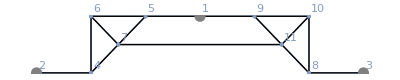

```mathematica
m=framework[{
{0,1},{-3,0},{3,0},
{-2,0},{-1,1},{-2,1},{-3/2,1/2},
{2,0},{1,1},{2,1},{3/2,1/2}
},{
joint[1],
joint[2],
joint[3],

(*left mechanism*)
rigidBar[{2,4}],rigidBar[{4,6}],rigidBar[{6,5}],rigidBar[{4,7}],rigidBar[{7,5}],rigidBar[{6,7}],rigidBar[{5,1}],

(*right mechanism*)
rigidBar[{1,9}],rigidBar[{9,10}],rigidBar[{10,8}],rigidBar[{8,11}],rigidBar[{9,11}],rigidBar[{11,10}],rigidBar[{8,3}],

rigidBar[{7,11}]
},
MeshCellLabel->{0->"Index"}
]
```

The analysis of 2nd order elasticity shows that there is a solution. This system collapses to a single degree of freedom when you account for the quadratic constraint.

```mathematica
{linear,quadratic}=Simplify[infinitesimalMotions[m,"variables"->v]]
```

{{{0,0},{0,0},{0,0},{0,v[2]/2},{0,v[2]/2},{0,v[2]/2},{0,v[2]/2},{0,v[1]/2},{0,v[1]/2},{0,v[1]/2},{0,v[1]/2}},{(v[1]-v[2])^2/(4 √73)}}

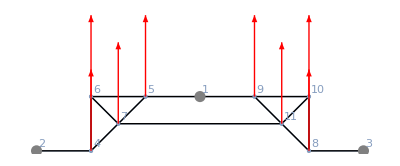

```mathematica
plotDisplacement[m, D[linear/.v[2]->v[1],v[1]]]
```

Even though the analysis correctly predicts a non-rigid structure, when we try to compute a trajectory, we find that only one side at a time can actually move. In fact, the starting point is some kind of singular, cusp that makes an infinitesimal analysis difficult. We can see this by ignoring the quadratic constraint.

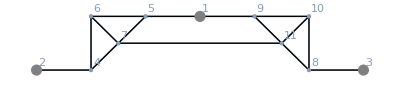
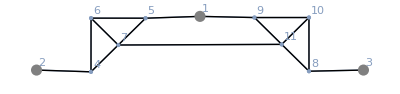
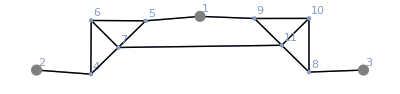
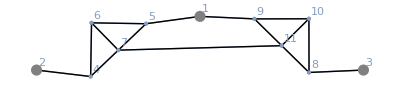
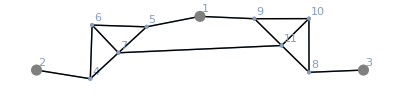
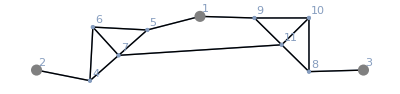
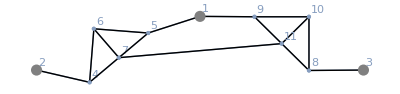
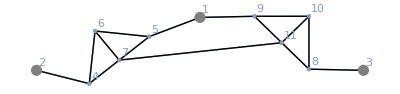

```mathematica
plotMechanism[m, isometricTrajectory[m,linear /. {v[1]->0,v[2]->-1},10]]
```

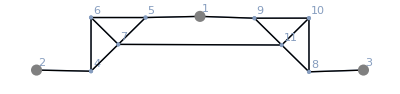
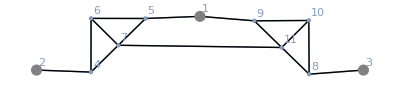
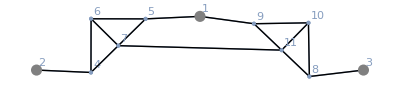
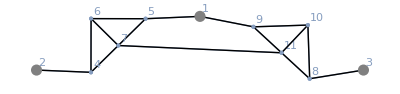
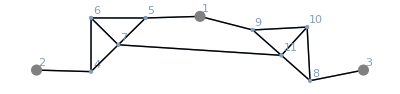
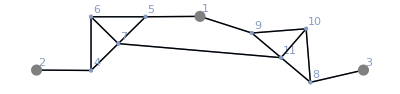
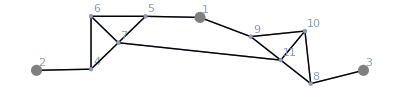
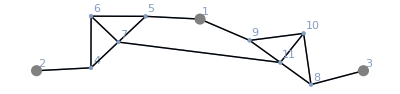
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plotMechanism[m, isometricTrajectory[m,linear /. {v[1]->-1,v[2]->0},10]]
```